#### Data

```mathematica
SeedRandom[1234];
SetDirectory[NotebookDirectory[]];
quoraquestions=SemanticImport["train.csv"];
quora=RandomSample[Join[quoraquestions[[All,5]],quoraquestions[[All,4]]],26654];
movie=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
lines=StringReplace[Partition[movie,5][[All,-1]],{"\""->""}];
linesJoined=StringJoin[Riffle[lines," "]];
sentences=TextCases[linesJoined,"Sentence"];
validChars = {"\t", "\n", " ", "!", "\"", "#", "$", "%", "&", "'", "(", ")", "*", "+", ",", "-", ".", "/", "0", "1", "2", "3", "4", "5", "6", 
    "7", "8", "9", ":", ";", "<", "=", ">", "?", "@", "A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", 
    "S", "T", "U", "V", "W", "X", "Y", "Z", "[", "\\", "]", "^", "_", "`", "a", "b", "c", "d", "e", "f", "g", "h", "i", "j", "k", "l", "m", 
    "n", "o", "p", "q", "r", "s", "t", "u", "v", "w", "x", "y", "z", "{", "|", "}", "~"}; 
wikiSimport=Import["wikisentences1.mx"];
wikiS = StringDelete[wikiSimport, Except[validChars]];
questions=Join[Normal[quora],Select[sentences,StringContainsQ[#,"?"]&]];
questionsWithoutQuestions = StringReplace[questions,{"?"->"."}];
normalLines=Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]];
```

```mathematica
classesqs=Thread[#->"Question"]&/@questionsWithoutQuestions;
classesnotqs=Thread[#->"Not a Question"]&/@normalLines;
(*classesJoined=Join[classesqs,classesnotqs];
training=RandomSample[classesJoined,20000];
validationset=RandomSample[Complement[classesJoined,training],2000];
testset=RandomSample[Complement[classesJoined,validationset,training],2000];*)
```

The data is loaded and divided into classes of questions and not questions!

```mathematica
classesnotqs//Length
```

46307

```mathematica
questions//Length
```

46307

```mathematica
normalLines//Length
```

46307

#### Changing parts of speech to numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
whQuestions = {"which"," what", "whose" , "who", "whom", "whose", "what", "which", "where","whither" ,"whence","when","how" ,"why" ,"whether","whatsoever"};
```

#### Changing parts of speech to numbers

```mathematica
vectorNumbers [ line_ ] := 
 (( TextStructure[line, "PartsOfSpeech"][[1,1,1,All,2,1]] ) 
     /. Missing[] -> {"","Missing"})[[All,2]] 

positionWh [line_ ] := StringContainsQ[ StringSplit[line] , whQuestions, IgnoreCase -> True]

numberPositionWh [ line_ ] := With[ {whPosition =Position[positionWh[ line ],True]} ,
                                If[ Length[whPosition] >0 , whPosition[[1,1]],0]
                           ] 

whQuestionsChecker [ lines_ ] := StringContainsQ[ lines , whQuestions, IgnoreCase -> True]
```

```mathematica
createClasses3D[ keyValuelines_List ] := Map[ { Keys[#],

                                        vectorNumbers[Keys[#]]/. rules,

                                    numberPositionWh [ Keys[#] ]/.{True->1,False ->0}} ->Values[#]&,
                                    keyValuelines]
```

```mathematica
SeedRandom[234];
classesqs2400=RandomSample[classesqs,2400]
classesnotqs2400=RandomSample[classesnotqs,2400]
```

{How come The Simpsons predicted things correctly (see the image).→Question,What'd the girl say.→Question,You know what we do to welchers Cluett don't you.→Question,What causes the energy losses in a centrifugal pump.→Question,How much did he give you how much did he keep for himself.→Question,How can I remove my satellite dish.→Question,What is it like to date someone who lives in Germany while you live in California.→Question,You didn't want to farm.→Question,What are some real life examples of “Karma"".→Question,Are they the ways of Huron men who hunt & work the land.→Question,How can I maintain my long distance relationship to the best of my ability.→Question,Do other lawyers at the firm keep pictures of their spouses or fiances on their desks.→Question,What are the best answers ""Why you want to do job"".→Question,What are some of the top paying career options after doing a B.Tech in mechanical engineering.→Question,Books.→Question,Gunther.→Question,You work at Borders right.→Question,Where is God.→Question,How can the volume of an isosceles trapezoid be calculated.→Question,What kind of goddamn monster are you.→Question,What does it feel like studying dentistry at AIIMS.→Question,You what.→Question,How big does a vagina get.→Question,What are the most difficult video games you've played.→Question,How should one deal with depression.→Question,My pen drive doesnot show up on my Mac. Is it corrupt. How can I solve this and get my data back.→Question,What's a cool gift for a guy who's the groom in a gay wedding.→Question,Now - where were we.→Question,OK before I loan you this I expect if you lose of course my money back within a week Crystal.→Question,What happens to a London bus driver if a ticket inspector finds a passenger with no oyster card.→Question,Is he your entertainment for tonight.→Question,My parents are from Kolkata and I was born and brought up in Delhi. Am I considered to be from Delhi or Kolkata.→Question,Is there any proof that there is no god.→Question,How can I eat food.→Question,Meaning.→Question,Do you have any coke.→Question,Is she always like this.→Question,How is MTNL for 6 months training purpose.→Question,What time did this thing happen.→Question,What should I do to go abroad for my higher studies.→Question,-- hang on -- -- yeah -- one guy -- I don't think he was ready -- -- it's just him.→Question,Herr Mozart what brings you here.→Question,What is the most cheapest option to buy Lexus Cars from Europe and export.→Question,When are English-speakers going to start empathising with their children and foreigners and reform their messed up spelling system.→Question,What are some good techniques for controlling your anger.→Question,Remove one element from vector c++.→Question,What are the expected consequences of Declaring 500 and 1000 rupee notes as illegal.→Question,What do you think of the President of the Philippines.→Question,How good is TIME's CAT percentile predictor.→Question,What!.→Question,How would one become an ambassador.→Question,Who were the victims.→Question,Boy Rimgale's as slow as a snail isn't he.→Question,Would America's healing from the Civil War been aided by trying and executing the Confederate leadership for treason.→Question,Why do people in relationships cheat.→Question,How does a microwave oven work.→Question,Did you tell him.→Question,What are the scopes of B.F.Sc.→Question,Does know.→Question,So why did you come to my casino.→Question,Why do girls like bad boys.→Question,Do you learn Cucumber and RSpec at General Assembly's WDI program.→Question,What's goin' on in here Lad.→Question,Who was the first U.S. President.→Question,Who really has all the power and directs the critical decisions of Thailand.→Question,What are the best new business idea in india with less investment.→Question,Why would a woman get angry and jealous of you talking to other girls if she didn't like you or at least have some sort of feelings for you.→Question,Is a data visualization itself data.→Question,How does the network send internet to a SIM card.→Question,Why do I love to people-watch.→Question,What are the home remedies for getting rid from back pain.→Question,How many veterans never use the GI Bill.→Question,You think I fit here where they just about chew your food for you.→Question,What.→Question,What are the basics of Digital Marketing.→Question,Now my flower do you understand.→Question,Does anyone find it odd/curious that women use makeup so regularly as a rule, whilst men do not.→Question,No chance of you lifting this sunbed up is there.→Question,Hey you couldn't help me with an incredibly important decision could you.→Question,When did surrealism start.→Question,Is Japan still relevant.→Question,Are you trying to read my palm.→Question,Captain Oveur.→Question,Ain't gonna be moved.→Question,What is Donald Trump really like in person.→Question,Blame the nigger then huh.→Question,WHAT'S YOUR NAME. Yeah.→Question,How do dogs and cats get along.→Question,Same thing isn't it.→Question,Hello.→Question,How do I boost stamina in order to not pass out during Muay Thai training.→Question,How often should I change the tires of my skateboard.→Question,Is the course locked in.→Question,How can can I delete my yahoo email account.→Question,Starting to recognize a pattern.→Question,Who cares.→Question,Will you let me look.→Question,What can I do to increase my concentration in studies.→Question,What should I do to improve my English .→Question,You saying its like part DeJesus part Sixpack part Bowman.! ..→Question,Can psychopaths and sociopaths fall in love.→Question,And.→Question,What's the difference between IMAX and 4K digital movie theatres.→Question,I am going to be majoring in social work soon. I want to work with LGBT youth. Do you have advice on how to do that.→Question,Yeah.→Question,Non loquis Latinum.→Question,What are the tips and hacks for getting the classes that you want as a freshman at CMU.→Question,Square (company): What happens at a TownSquare.→Question,Excuse me.97 Got a handkerchief.→Question,Did Valentin.→Question,What's April 16th.→Question,What do you mean.→Question,What is Russia's nearest equivalent to the Grand Canyon.→Question,What kind of God is He to will this.→Question,Some good places in los angeles.→Question,Your mother was blind.→Question,Which are the best places to learn Spanish abroad.→Question,What are some good books for XAT preparation.→Question,Which is the best laptop under 85k.→Question,Sent it where.→Question,Listen to her.→Question,What is the most interesting app or program on mobile phone or computer.→Question,Westworld: If only 1st generation hosts can navigate the maze, what do you predict will happen with the more recently built hosts in episodes to come.→Question,Are you a giraffe.→Question,Who knows what bigger cosmic reason might exist.→Question,What should India do to increase its per capita income.→Question,Knew what.→Question,A MiG.→Question,Did I give you a job this mornin.→Question,What is the best digital marketing course available online and offline in India and Why.→Question,How can I learn programming from scratch.→Question,Where are you . . . . Please leave your message at the beep.→Question,Why didn't you go to college.→Question,Why does one feel the need to put a label on their significant other when having an argument.→Question,How do I sign out of Apple Music.→Question,Does MSE not work as a metric for recommendation systems based on implicit feedback.→Question,Why does Britain prefer tea to coffee.→Question,How do I get over with depression or anxiety.→Question,What is the best sport bike.→Question,Are royalty fees paid to individual deductible as expenses on a LCC.→Question,How do telecoms trace my location.→Question,How do you treat gunshot wounds.→Question,Do you read me bomb.→Question,What workout attire would guys wear in the summer like it's the year 1990.→Question,Do Facebook friend suggestions show up on both people.→Question,Louis whatever gave you the impression that I might be interested in helping Laszlo escape.→Question,The executioner of the king's nephew my husband's own cousin.→Question,How does magnesium oxide reacts in water.→Question,Should I learn programming and Vim at the same time so I can get used to code on Vim.→Question,What should I do if I love a girl and she apparently doesn't love me.→Question,Why do Muslims believes that it is okay to beat their wife.→Question,And what are you like.→Question,Is wbJEE board release marks officially in the wbJEE examination.→Question,Are you sure you have to go.→Question,What are some reasons your throat hurts when swallowing.→Question,Why doesn't Quora allow the use of emoticons.→Question,Which are the manga related episodes in 'Naruto Shippuden' anime.→Question,Why is Kenya considered a Third World country.→Question,I just realized this is for television, isn't it.→Question,Cannon or Gatling.→Question,No did you use a condom.→Question,Yeah Would you hold this for me.→Question,As a language student, what would be your favourite way of maintaining materials & assignments.→Question,How should you land in water if jumping from a tall height (e.g.: a cliff).→Question,How long until it blows.→Question,What kind of businessman are you.→Question,How do Quora and Google earn money.→Question,Did Joe Rogan go to college.→Question,Which is the best earphone under 1000rs.→Question,You're not into kinky shit are you Angelo.→Question,So I'll get a fair trial in front of a jury bought off by Thaddeus Rains.→Question,Why do certain people stay at the top in likes in Instagram.→Question,Why did not Rupee get strong against the Dollar even we have demonetisation.→Question,What are the lyrics to the German happy birthday song.→Question,Why is salt water taffy candy imported in France.→Question,How do someone live to be happy in 20s.→Question,Back in the Czech Republic.→Question,What is the chemical composition of space.→Question,How many guys they have on you.→Question,Apart from describing people, can ""affable"" be used to describe things, like ""affable time"".→Question,And what's that mean.→Question,What exactly is this place.→Question,What are similar sites like Quora.→Question,What does Balaji Vishwanathan think about the ban of ₹500 and ₹1000 currency notes in India.→Question,What are some of the best gadgets of 2016.→Question,What the fuck you talkin' about mischief.→Question,Your bookie.→Question,You could have infected him isn't that right.→Question,How are we doing.→Question,You okay.→Question,By burning down their homes.→Question,Where are we.→Question,Is the Emperor angry with me.→Question,What prevented Mr. Acme from putting the will back in the safe before they killed him.→Question,How can one solve z^3=-1.→Question,How about taking to Uncle Larry into the old firm.→Question,Your base isn't secure.→Question,Where do bench presses work.→Question,Where can I find some of the best SEO services in India.→Question,What's going on.→Question,What are the procedures to get CDC in India.→Question,I have taken a job in IBM tech support. Will this job experience count when I apply for a job after an MIS degree in US.→Question,How can I remove dark circles under eye.→Question,Why did they stop making the new Mauka Mauka ad.→Question,Frank.→Question,You made him up didn't you.→Question,How can I increase my interest in programming.→Question,Does a dead skunk still spray.→Question,How do organisms evolve different numbers of chromosomes.→Question,You sure you killed them.→Question,Why is Jake Williams popular on Quora.→Question,Is it better for your neck / spine to sleep with or without a pillow if you sleep on your back.→Question,What are some of the coolest looking passports from around the world.→Question,What's this about money.→Question,Are southern US religious and political values incompatible with the rest of the United States.→Question,What would be the sample size for the assessment of knowledge, attitude and practice of mother's regarding breastfeeding in a government hospital..→Question,Alive.→Question,They either say 'Kill the nigger' or 'Hope you die Honky.' -- What ya got in the bag.→Question,And who would you think of for such a task.→Question,Why is nobody allowed to make fun of Robin Quivers when everybody else on the Stern show is insulted constantly.→Question,Hello.→Question,How do I post a question in Quora.→Question,Is there a reason as to why in a deck of cards the queen of all four suits faces the front view, one king faces the side view and two jacks face the side view.→Question,Who did this.→Question,Where'd you get this.→Question,How shall I get rid of hair fall.→Question,Well are ye satisfied Mr. Mitchell.→Question,Like Francais Black Robes do.→Question,Is there a Google search operator for partial word search.→Question,You want a tip.→Question,What should I do to prevent myself from commiting suicide.→Question,What does he say.→Question,What'd Owens mean.→Question,Which is the best way to earn money without working hard give examples.→Question,All right.→Question,What is voltage drop.→Question,What's the farthest star we can see with the naked eye.→Question,What've you got there.→Question,Did you dream....→Question,Can I get pregnant a week after my cycle.→Question,I was hilarious once wasn't I.→Question,How are my friends earning millions from home just by using Uber app.→Question,More tea.→Question,How do you go up and talk to a girl you like.→Question,What is another word for showing.→Question,Have you considered going into therapy yourself.→Question,How do I can whole tomatoes.→Question,How can someone lose weight quickly.→Question,How reliable are property management service providers like renteazy or realtykart in Bangalore.→Question,Does drinking green tea for weight loss really help. Does it have any adverse effects on your skin.→Question,What could it mean to you as an employee of a startup if it gets acquired.→Question,Where did YOU come from.→Question,Are there any CEO's of holding companies that serve as CEO's of subsidiaries.→Question,How does an oscillator work.→Question,If an object at the equator travels at 1040mph with earth's rotation, why does it not appear to move and stand still.→Question,What is wrong with the American education system.→Question,You ever been in a hurricane Mueller.→Question,If you were stranded on a Island which celebrity would you take with you.→Question,Why the beach.→Question,What is Advanced Mathematics.→Question,How long does it take to design a simple 2D game character.→Question,How can I kill the QUIRA Dipstick's that keeps waking me up at 3am.→Question,How can I work in Silicon Valley.→Question,Does the EM Drive work.→Question,How do I find all of my Gmail accounts.→Question,Well we pay for the [.].→Question,How do I convert CGPS marks in to Percentage.→Question,What is the best way to spread a Twitter hashtag.→Question,May I help you sir.→Question,What is zombo.com.→Question,What is suspension rail.→Question,Should we learn C.→Question,You mean you don't want the usual day and a half to think it over.→Question,But I'd like to take a crack at that stiff- necked horse dollar.[6] Say Matt you haven't done anything about what you saw today have you.→Question,Where are we going.→Question,What is the difference between hobtop and gas stoves.→Question,How would you compare the United States' euthanasia laws to Canadas.→Question,What is the best revenge after being rejected by someone.→Question,What universities does Square 1 Financial recruit new grads from. What majors are they looking for.→Question,What are some best American TV shows.→Question,An' now you're worried about a repeat of history.→Question,What are the top MBA schools in Australia.→Question,Can stimulants increase Intracranial pressure.→Question,I asked my mom to wear makeup and she said no angry. How do I convince her to let me wear makeup now.→Question,What existed in the space before Big Bang.→Question,Which is a suitable solar panel installation provider near Kingsburg, California CA.→Question,Estoy perdido--[Where are you.→Question,Which books should I prepare to crack IIT JAM in Biological Sciences.→Question,What's the secret of happiness.→Question,Is there any site for online sweatshirt shopping in India.→Question,Do you need a ride.→Question,Nah why should you.→Question,How did The Boss get greenlit. What's the backstory of how the movie got made.→Question,If the latest version of PHP is now object-oriented, does it have class like Java or .NET. Is it more like JS.→Question,Where can I find subtitles for Tamil movies.→Question,What is your biggest accomplishment in life.→Question,At what age do you think of a person as being ""old"".→Question,You think you'll have time for the water heater this weekend.→Question,What's it like to live in the Five Towns of New York.→Question,But now that I am here will you speak with a woman.→Question,You're sorry.→Question,Is Latin America considered to be part of the Western World.→Question,Why is Kim Jong-un considered to be funny.→Question,What do you mean.→Question,How could there have been witnesses.→Question,Oh yeah....→Question,Is steel a pure substance.→Question,Do you like my body.→Question,Remember the guy who cheated at the table.→Question,Anything harder.→Question,And you don't know how they open is that what you are saying.→Question,Do you remember what she said.→Question,What.→Question,How different is film editing compared to digital strategy.→Question,So the guy asks him where he's got all this money all of a sudden right.→Question,What is the difference between an adiabatic and isothermal process.→Question,Smith where the hell have you been.!→Question,I was dreaming again.→Question,Yes Prince Mishkin what can we do for you.→Question,Remember our first date here....→Question,How you doing Bob.→Question,Jameson.→Question,How do you think consumers have changed as a result of 9/11.→Question,Any luck.→Question,How are they treating you.→Question,What do I mean to you.→Question,What is that.→Question,Should I take a Software Engineering job at Uber or Indeed.→Question,I want to know reviews about point group ""Barcelona"" internship.→Question,How do I get incoming and outgoing call details of a particular prepaid number here in India.→Question,Why don't you answer your phone.→Question,Ludwig.→Question,How do I read a balance sheet.→Question,Will Trump's win affect the matriculation of students who wish to be graduate from USA.→Question,But what if he dies on the way back.→Question,What happens to all the queued posts, when a very active WhatsApp user logs in after a year. Will the mobile hang for an hour or so.→Question,Evolution (process): From which animal have monkeys evolved.→Question,How can I get money.→Question,Which is best Laptop to buy in around 60000 Rupees, with best configuration.→Question,Who said anything about slicing you up.→Question,Is it legal to carry bhang on a domestic flight in India.→Question,How do I mentally handle the fact that many guys pursue my girlfriend.→Question,Where you going.→Question,Have you.→Question,Could anti-matter be used as a futuristic and efficient form of energy storage.→Question,Is Dr yeshi dhomdhon medicine effective in curing fourth stage of cancer.→Question,What is the difference between PaaS and API.→Question,I don't think Miggs could manage again so soon even if he is crazy - do you.→Question,What is it like to be in the Bohemian Grove.→Question,What is critical thinking.→Question,From what.→Question,Why.→Question,How much does it cost to make a 2000 rupees note to Indian government.→Question,Will you marry me.→Question,What weighs more, all of Earth's air, or all of Earth's water.→Question,If x+2<0 then |x+2| is equal to.→Question,What are the best books for entrepreneurs to read.→Question,How do you send a text message to a blocked number.→Question,How good is DTU.→Question,But where are you planning to stay in New York.→Question,Who do you think would win the election, Trump or Clinton.→Question,Which mobile has best camera.→Question,How can I make TOR faster.→Question,Why not.→Question,How can I become a white hat SEO.→Question,A logic teacher said You don't have a brother and he likes cheese.how is this rational.→Question,What did you want with me.→Question,Why are all the Hindu Gods born in India and not in any other country.→Question,How does one kill a man.→Question,Found somethin' worse than me huh.→Question,Questions.→Question,Miller.→Question,what... .!→Question,I made her feel guilty this morning --  Brother what are you doing up.→Question,How do I multiply and divide fractions or decimals or a decimal and fraction together.→Question,Which one has higher a compression ratio, SI or CI engine.→Question,Who was Lord of Storm's End after Renly's death.→Question,What is it like to live in Yakutsk Russia. I am fascinated with this place.→Question,I have a 2 wheeler and double car parking below my flat. A guy today moved my 2 wheeler, which was on center stand and locked to the right side of the garage. What should I do.→Question,Shut up -- shut up -- Did you piss your fuckin' pants Stanley.→Question,How could he.→Question,How do one can call Ayurveda scientific when scientific methods are not used in it.→Question,How do you feel.→Question,I have 6 years of experience in vehicle quality in an automotive OEM in India . I want to work abroad. Which countries offer good job opportunities.→Question,How would you switch out isotopes.→Question,Passport police verification status pending, police officer says due to delay of verifying birth certificate, how much time does this usually take.→Question,Sir.→Question,Why do caucasians guys find Filipino ladies attractive.→Question,What.!→Question,What is worse than death.→Question,Why didn’t RBI introduce the plastic currency in India with the new 500 and 2000 notes.→Question,What is a better car, the Mercedes Benz G LA or the Acura RDX.→Question,If you have an 8 oz. Coke bottle and go into a drug store and switch it out with an exactly identical 8 oz Coke bottle would that be considered stealing.→Question,What did you learn too late in your life.→Question,Killaine's wise to what.→Question,In this heart.→Question,How can I travel without money to work voluntarily.→Question,Oh yeah.→Question,How do I reset my password to Gmail without my recovery information.→Question,How do I start blog and earn money from it.→Question,What is it my son.→Question,How many.→Question,What side dishes should be served with Mac and cheese.→Question,What's this.→Question,Blood: What is an immunoglobulin.→Question,Can airplanes and jet fighters fly with no atmosphere.→Question,What proportion of Quora users are atheists.→Question,Why do people believe the earth is flat when clearly earth is round from space.→Question,Do you have any idea what those monks charge for that medieval torture.→Question,How can I set up forwarding on Yahoo Mail.→Question,I beg your pardon, epi-zoo-tics.→Question,What is the most pretentious thing you have ever heard someone say.→Question,Which is the best site for learning python from the scratch.→Question,Is it acceptable to wear black shoes with dark khaki pants.→Question,Is it easy/hard for international students to get a job in Dublin, Ireland.→Question,Who is he going to kill.→Question,Ever even been <u>in</u> one.→Question,How did biological viruses come into being.→Question,Netaji Subhash Chandra Bose alive after 1945.→Question,How do I delete all my posts from Facebook.→Question,Did he tell you how we finally met.→Question,Does he even *want* to come back.→Question,Is college even worth it.→Question,Where're the others.→Question,How do I deploy a Flask website to Google App Engine.→Question,If you could thank one person that you've never met for contributing to your life in some way, through an invention or a quote or a piece of advice to a general audience, etc., who would that person be and why.→Question,Where can I get shopping centre cleaning services in Sydney.→Question,What evidence is there to say that the Christian God is the real one true God.→Question,How do I know if I'm blocked on WhatsApp.→Question,Do you understand.→Question,When did Harp say they'd have the warrant.→Question,KTM Duke 390 or Suzuki Inazuma: which one is better.→Question,How much do fireworks cost.→Question,On news channels like CNN or cable networks like CNBC, Bloomberg, etc., do the guests/experts who are invited to talk or respond to questions get paid. If so, typically how much.→Question,How can I raise my self esteem.→Question,How did our relationship with Stalin during WW II lead to the cold war.→Question,How many days will it take to release the offer letter from Capgemini.→Question,Or Reno.→Question,What do people of Pakistan think about Uri attack.→Question,Which mobile I should buy under 15k.→Question,What are you going to do.→Question,What does it feel like to be high on DMT. What are the consequences.→Question,Why do you not like Hillary Clinton.→Question,Do you think he'll take the job.→Question,What is the best way to enlarge my penis.→Question,What's the difference between death and black metal.→Question,Are GATE lectures by Ravindrababu Ravula worth it.→Question,Who owns the most AMOLED patents as of October 2014.→Question,Art thou not Romeo and a Montague.→Question,What's the problem.→Question,Why do we connect the positive terminal before the negative terminal to ground in a vehicle battery.→Question,What is intelligence to you.→Question,What are you lookin' at.→Question,What does it mean if you blood results indicate high absolute monocytes.→Question,What can I do to gain more attention on Quora.→Question,How Darwin's theory of evolution is right.→Question,How do I gain more weight.→Question,What is professor Thomas Cormen's favorite data-structure.→Question,Why is it important for you to be married.→Question,Absolutely -- Sparrin' with the Champ would be an honor -- y'know what.→Question,Who.→Question,And what's that supposed to mean Seamus Reilly.→Question,Is it interesting to work as a cyber security.→Question,have I broken any laws.→Question,Guess who.→Question,Which is the best digital marketing course.→Question,What is a social justice warrior.→Question,How can I easily pass the C2150-195 exam.→Question,Where is he anyway.→Question,Data Recovery: I've lost all my contacts on my iPhone, however they are all there in iCloud. How can I get them back onto my iPhone.→Question,About clothing.→Question,Which is best smartphone to buy under Rs 15000.→Question,You're so quiet all the time.→Question,Range.→Question,I sent a message through WhatsApp. The recipient was online and I got two check marks. She said that she didn't get the messages till 5 hours after though. Is that possible. What could be the explanation for this.→Question,What is the easiest way to transfer files from a PC to an iPad.→Question,What are some of the main and most important characteristics of the Flamenco dance.→Question,Wanna ask someone please. What is life. And what is the purpose of our life.→Question,How can I improve my english language skills. I am basically from gujarati background.→Question,Are there any institutions that offer ethical hacking as a course.→Question,How corsera certificate and examination works.→Question,If I was taking calls full time would I be living in this kip.→Question,What if mental illnesses didn't exist.→Question,Who.→Question,Really.→Question,What is a good solar panel installation provider near Lemoore, California CA.→Question,I accidentally waived my rights to Jury Duty compensation in the online questionnaire; how do I undo this.→Question,What do people do when they are really bored.→Question,Can you describe to me your life using one word only.→Question,What are the most useful devices or gadgets you own for your smartphone that maybe other people don't know about.→Question,How do I know who I am.→Question,Demonetization may be indirect result of Inviting more FDI into India. Do you agree.→Question,Are you all right.→Question,What.→Question,What does radiant energy turn into. How is it used and what are some examples.→Question,Who.→Question,You didn't tell him did you.→Question,So what.→Question,How does Brexit affect Indian economy.→Question,Why is Foodpanda called panda when its a Germany company founded by a German.→Question,What do you need.→Question,Women: How can a guy tell if you are interested in having him kiss you.→Question,What would you call her.→Question,Is there a place to find Netflix's entire online library.→Question,How do I lose weight and reduce my waist quickly.→Question,How you would create alternative to Shodan.io.→Question,You heard of kickboxing sport of the future.→Question,I have to go I don't have time and I have more drinking to do before I go march -- Did you tell her.→Question,How do you redeem Google Play codes.→Question,How do people with very few views become Top Writers on Quora.→Question,Where am I.→Question,Tell me do you know what the word &quot;propaganda&quot; means.→Question,Do humans really exist or are we just living in a spiritual virtual reality.→Question,Is that your penance.→Question,What do I say to Miss Sweet when I meet her.→Question,Did you do any of that.→Question,Why not.→Question,Which is a suitable inpatient drug and alcohol rehab center near Valley County ID.→Question,Who put you up to this -- the manager.→Question,What was Adolf hitlers childhood like.→Question,Which was the longest active civil war.→Question,What do you get out of it.→Question,Can time travel ever be possible.→Question,What is Quora, and why should I use it.→Question,What.→Question,You don't like me.→Question,How should I prepare SBI-PO exams.What are the Popular websites for preparing for Exams like SBI PO.→Question,Does that check out down there.→Question,What was your mother like.→Question,What are the best peaceful locations in India for holiday.→Question,What are the best places to visit in Kerala. What is the best way of transportation there.→Question,What is the difference between transformant and recombinant.→Question,What is it like to perform in each of the high school track and field events.→Question,My boyfriend (LD) is being forced by his parents to marry a girl of their choice. We tried everything possible to convince them but nothing worked. He says it's better to move on than to hurt his parents. But I don't have guts to see him with someone. He loves me so much, should we sacrifice our love.→Question,What is the purpose of life.→Question,did it look at you Brian.→Question,What is your favorite quote, and why.→Question,Why.→Question,Islam: Why is pork forbidden in Islam.→Question,How would an Indian parent react if they were to learn that their daughter was impregnated by a black guy.→Question,Where's the shell.→Question,What.→Question,You ever see Queen Elizabeth sleep.→Question,What night.→Question,Are women sexually attracted to testicles.→Question,How do you think this makes me look treating her like some tragic victim or something.→Question,What is a good torrent download site.→Question,What's the best way to get started learning about computer security.→Question,That's all you've got to say you've got a bad cold.→Question,What is it like to be a laser hair removal technician.→Question,What are the best love story books.→Question,What do you mean never.→Question,How do I overcome a crush.→Question,This doesn't involve you don't you understand.→Question,You what.→Question,What made you happy today.→Question,What were you gonna do.→Question,Would you like a drink.→Question,Did you have a nice day.→Question,Up get it.→Question,Did you make anything of the tooth.→Question,How much do top management consulting firms charge clients per consultant in 2015.→Question,How will the demonetization of Rs 500/1000 notes finish the black money in the market exactly.→Question,Why.→Question,What do you want.→Question,Why did the Zune hardware fail.→Question,How can I improve my communication skills specially pronunciation skill.→Question,Who.→Question,Which programming language is the best nowadays.→Question,Which are the major highways in California and how are they compared to the major highways in Washington.→Question,What are the strengths and weaknesses of the advising system at Penn State.→Question,Do you think Paul Pogba is overrated.→Question,What are good exercises to get rid of belly fat.→Question,Hi Gale any leads.→Question,Can one get a Canadian work permit and then look for a job.→Question,Gabriela ....→Question,What responses do Christians give when shown controversial verses like Exodus 22:20 or II Kings 2:23-24.→Question,What.!→Question,Sparrin'.→Question,Oh is he.→Question,I am looking for website promotion. How can I find Best SEO company in Delhi for my website promotion.→Question,In a fucking seance.→Question,What was I supposed to do.→Question,Which are the best android development companies for freshers in India.→Question,What is tcs values.→Question,Advantages of unitary government.→Question,HOW MUCH TIME.→Question,What is a ventilation system.→Question,Which motor has high starting torque AC or DC.→Question,How much do Uber drivers make in Austin.→Question,Who was the richest dead person.→Question,How do I unsubscribe and delete my Quora account.→Question,The Partridge Family.→Question,What's wrong with that.→Question,But why.→Question,Do Muslim women like to wear burqas.→Question,What should I do to get cellular companies to install a mobile tower on my plot of land in India.→Question,Is it better for your brain to smoke weed during the day or before sleep.→Question,Is anatomy destiny.→Question,What you gonna give it all up for a maple twist.→Question,There's cars back there right.→Question,How can I find the area of the shaded region.→Question,Maybe I shouldn't have-- Ted will you take it easy.→Question,How do I learn to be a lighter sleeper.→Question,And.→Question,Auto Repair: How much should it cost to rebuild a 2000 Honda Odyssey transmission.→Question,How's Butkus this mornin'.→Question,I want to prepare for civil service exam. Currently working in an MNC. How should I start preparing. I am 27 yrs. is it possible to crack before I hit 30 age limit.→Question,How come you were in my truck.→Question,Phase Transitions: How does water evaporate below its boiling point.→Question,Was Alexander the great really ""great"".→Question,And his other companion.→Question,What is the size of an average woman's vagina in length and girth.→Question,What is online wedding invitation.→Question,Mary still isn't in.→Question,If Arabs are considered white, why are they not recognized or treated as the same as whites.→Question,How many sugars.→Question,Why does urine smell bad.→Question,Hey Sugar you lookin' for a date.→Question,So what do we do.→Question,What is the difference between UTC and GMT.→Question,Did Uber really switch to using Dropbox instead of Box.→Question,May I ask you a question.→Question,What will the filmmakers do with the Leia character in Episode IX, now that Carrie Fisher is dead.→Question,What's to become of us now.→Question,Does he always leave so early.→Question,Will Donald Trump actually make America great again.→Question,Why not.→Question,The amusing house wine....→Question,Which is best gaming laptop under 60000.→Question,Invitations.→Question,slip her one.→Question,How well.→Question,What are the pros and cons of using internet.→Question,What is a good inpatient drug and alcohol rehab center near Union County GA.→Question,Does Bradley Cooper say “pour manger” in this French audio clip at 10:33. Yes or no.→Question,That...→Question,Is a loan-based crowdfunding platform classified as a financial institution.→Question,Is it safe to buy a laptop online.→Question,Wolfi who gave you this.→Question,Did she waltz in or fly on little bat wings.→Question,What are the pros and cons of being a journalist.→Question,Why do Bangladeshis and Sri Lankans look very similar.→Question,You slept too near where you got in.→Question,Which are the best books or learning resources to prepare for the GRE.→Question,Should I join the French Foreign Legion.→Question,What is the basic difference between cv and resume.→Question,What are you saying.→Question,How can I grow my hair thicker.→Question,What was that armed.→Question,Why did the Germans hate the Jews even before Hitler.→Question,Why are you here.→Question,Mumbai University Law School, Fort (Besides high court and a 100 Metres walking distancce from GLC) or Government Law College.Which one do I choose.→Question,May I introduce my father.→Question,Man you really zinged the boss a couple times it was all I could do-- Yeah.→Question,How is whipping cream the same as cream.→Question,Does playing blitz make one a stronger chess player.→Question,I like one of my junior. How can I ask her out.→Question,So how come you could play basketball.→Question,What is the highest frame rate (fps) that can be recognized by human perception.→Question,Then why not give Miss Mayfield the benefit of the doubt.→Question,How could Quora attract initial users.→Question,How should I stop masturbating.→Question,What's the best way to spend $2,000 on SEM for a lead generation campaign for a new investment product.→Question,A Storm Dragon.→Question,Really.→Question,How are reservations helping Indian societies.→Question,How do I post an image in Quora.→Question,So Don Juan you pass out on all your dates.→Question,What is the best book to study for the GRE.→Question,But the wisdom tooth will have to be pulled.→Question,Which are the best mystery novels.→Question,Are we locked up.→Question,Power spells and chants.→Question,What clan in clash of clans is level 10 with no wins.→Question,No.→Question,What are the least useful courses that people typically take for a degree in archaeology.→Question,Which is the best platform to learn online and get knowledge + certification for Digital Marketing or every course in general.→Question,Who do you think about when you masturbate.→Question,So what are you gonna do about it.→Question,Can't you forget for just one night that you're completely wretched.→Question,What are the sales figures of Coca-Cola in India. How much do they sell in India.→Question,How can I write SEO content fast.→Question,What are the best LOTR fan fiction stories.→Question,Anything else you want.→Question,How do I conduct a job interview.→Question,Why does Julian Assange have white hair.→Question,What are the reasons for World War 1.→Question,What is the best way to have beautiful skin.→Question,Surfer grunge hip- hop Euro trash.→Question,I've come to apply for membership in Brolly -- Really -- what happened in 1922.→Question,You remember.→Question,Yes Griff.→Question,What is the best way to express your thoughts.→Question,Where is teach mashal art.→Question,My phone Moto G2 haw can use Jio.→Question,Is Donald Trump an agent for Vladimir Putin.→Question,And why should she.→Question,You talking about the Opera House on the Main.→Question,What is the Sahara, and how do the average temperatures there compare to the ones in the Karakum Desert.→Question,What is the difference between RIP and RIPv2.→Question,The grammar.→Question,How do I find stock prices.→Question,Should I have something for you.→Question,Are there good detective movies or TV series like Sherlock (already watched castle).→Question,Would you mind.→Question,Nobody will ever know what happens here -- I was starting to believe you you know.→Question,FRIENDS vs Big Bang Theory: which one is the best TV series to watch.→Question,A man or a mouse.→Question,Sisters.→Question,How effective is scrapping 500 and 1000 rupee notes. Will it reduce black money.→Question,Where can I get a removals service in Gosford.→Question,How can I fix a broken friendship.→Question,How much.→Question,What do I think.→Question,And what job is that.→Question,How do I keep a relationship when I can't talk to them everyday.→Question,Did you ever think of that.→Question,What is it.→Question,How do I recover deleted photos from a Samsung Galaxy S6/S5/S4/Note.→Question,How did Singapore universities (NTU, NUS) become world-class and climb up the university rankings in a relatively short time.→Question,What is CRR and SLR.→Question,What is the best describe the differences and uses between storage classes in C.→Question,What is your favorite Halloween costume for 2015.→Question,How do I open password protected .txt file.→Question,Who is the best kpop singer.→Question,Okay by you.→Question,Is there any way to travel faster than light.→Question,How do I pass lab drug test with baking soda.→Question,No blood vengeance.→Question,Guaranteed eh.→Question,What are the list of US universities that accept 15 years of education for a MS in computer science.→Question,Is that your idea of a winner.→Question,What is the difference between an APU quad-core A8 and an Intel i3.→Question,What is your greatest regret in life.→Question,Who are some well-known Quora users who have become disillusioned with the platform.→Question,How can I become a good web designer.→Question,Is there any valid research supporting the claim that massage therapy rids the body of ""toxins"".→Question,Do you wish him to be amongst us.→Question,All in yellow.→Question,Your wife.→Question,How strict are hostels.→Question,What do you miss the most from your childhood.→Question,I love to listen to slow/romantic/sad/hip-hop-rock Punjabi songs. What are some suggestions.→Question,What ethical issues do operators of restaurant need to be aware of.→Question,Why not go to the N.C.I.C. or N.C.M.E.C..→Question,You've been here before.→Question,Which are some of the best laptops to buy in India.→Question,Is Quora Spanish for what.→Question,How do I control my emotion and sadness.→Question,What is the best Perl web app framework.→Question,What are best places to visit around delhi.→Question,What type of government does Guatemala have. How does it compare to the one in Japan.→Question,You want my heart.→Question,What are the best programming languages for beginners and why.→Question,What is the best profession for me. I love to travel the world and I am 25 now.→Question,Can you recommend some products you bought that have improved the quality of your life greatly.→Question,What are you talking about.→Question,What.→Question,Will foreign students studying in the USA be unwelcomed after Donald Trump is elected as president.→Question,Has he sent the challenge yet.→Question,Are you a socialist Mr. Penfield.→Question,What toughened you up.→Question,What is the significance of a name.→Question,Reef and I can take the Explorer down clamp it around the eye and --- 'Us.' You've got to let us try Skipper -- Skipper!→Question,What is the easiest way to lose weight faster.→Question,Red Bull Stratos Mission (October 2012): What did Felix Baumgartner say before he jumped off his capsule.→Question,I have a 7KVA generator which I use for multi-purpose. I sometimes run the AC on it and sometimes I don't. Will the generator consume less fuel when I utilize its power generation less.→Question,Were you and my father having an affair.→Question,Trubshaw again.→Question,How do you find motivation to work out.→Question,How painful is it to get a daith piercing.→Question,Hey -- Did these guys teach you to talk dirty.→Question,Is it possible to play the piano without knowing how to read musical notes.→Question,Why do we need a device driver.→Question,This is my first time in MUN. How should I prepare for the committee GA-DISEC.→Question,What.→Question,What's that on your forehead pal.→Question,Yosemite National Park: How was Half Dome formed.→Question,How can covalent bonds be described.→Question,Why are there 24 hours in a day, and how does the lenght of day on Earth compare to the one on Mars.→Question,What would be the best way to control anger.→Question,You expect *her* to be responsible.→Question,What would be impact on India if Donald Trump becomes President.→Question,Where are you from originally. ...just wait..→Question,Then.→Question,Who the fuck was he Rocco.→Question,Will drinking Coke after food help in digestion.→Question,Besides advertisement, how does Facebook earn money.→Question,Was it alright.→Question,Is it true.→Question,Why is Harry Potter rude to Colin Creevey.→Question,How do I make friends with people on Quora.→Question,Which's the best state in India.→Question,And hope to die.→Question,Austin what's your point.→Question,Shall we.→Question,Are we alone in the universe.→Question,Special Relativity: What would stop someone accelerating beyond the speed of light if they had achieved 99.9% of the speed of light.→Question,How can you tell if someone has blocked you on iPhone.→Question,Are you ok.→Question,What could cause them.→Question,What's a good symbol to represent knowledge.→Question,What can I do.→Question,How  many other girls Miss Teschmacher are lucky enough to have a Park Avenue address like this.→Question,Where did you get it.→Question,Hey who cared about me yesterday huh.→Question,Joanna what the hell is-- Ted when we got married it was because I was twenty-seven years old and I thought I should get married and...when I had Billy it was because I thought I should have a baby...and I guess all I did was mess up my life and your life and-- Ted do you love him.→Question,What would be a cool name for a consumer electronics start-up.→Question,Could modern army beat Pokemon army.→Question,How do letters of recommendation work for college admissions.→Question,How many solar panels do I need to charge 4 200ah.→Question,How do I know that she like me.→Question,Dr. Weir.→Question,What are the major development initiatives Modi's government is working on.→Question,Where is the Management Tasks link on my Google groups home page. Am I blind.→Question,Why does McDonald's place playgrounds in their restaurants.→Question,How do I flirt with any girl.→Question,Something wrong with the stairs.→Question,Is that all.→Question,Is that possible to live without money Can you live without money.→Question,Which is the best platform to learn online and get knowledge + certification for Digital Marketing or every course in general.→Question,What.→Question,How can I delete my Quora account in one minute.→Question,Maybe we should bail.→Question,Can somebody help me with the list of best top horror movies of all time.→Question,Why did Quora remove my question.→Question,When.→Question,Why aren't I am getting views even after writing answers.→Question,Approximation inverse matrix.→Question,How can I join the army after finishing college.→Question,How is he.→Question,how much will the whole thing cost.→Question,Why wasn't there an insurgency in Germany after the end of World War II.→Question,How can black money brought out by discontinuing 500 and 1000 notes.→Question,See.→Question,Can anime exist in a parallel universe of some kind.→Question,Why do some people hate Shahrukh Khan so much.→Question,What do you think.→Question,What are the most charming small towns in USA.→Question,Who's Guilder.→Question,How is the service tax for Ola Cabs' rides calculated.→Question,HE IS DEAD and WHO TOLD YOU TO DO THAT.→Question,What where the things that Apple introduced in the September 2016 Apple Event.→Question,Is consolidation and creep same or do they have some difference.→Question,So where is it.→Question,Why do people study mathematical cognition.→Question,Is that better.→Question,How does that feel.→Question,Does he know that.→Question,Is  'Dabiq' magazine an effective recruitment tool for ISIS. If yes, why is it easily available.→Question,Is dinner ready.→Question,That's Sean.→Question,Still bothering you.→Question,No  You think she's a tweaker.→Question,What is the difference between a Bar code and a QR Code.→Question,Does stretching your spine gives you permanent height.→Question,Yeah.→Question,I'm interested in creating my own product for private branding. Can I do this on a shoestring budget.→Question,What are good movies on Netflix.→Question,So where are you from.→Question,What did you find out about your teacher that shocked you.→Question,You know what you look like.→Question,Even though people are educated, and even after they have knowledge of science, why do they still believe in God.→Question,On average, how much does a CEO make per year.→Question,What do you mean.→Question,What does Islam say about homosexuals, their rights, marriage, punishment if any. And what issues do gay Muslims face in their daily lives.→Question,What's a Good Disney movie.→Question,How did you two fuckin' fucks..........→Question,If you only have one day left, what will you do.→Question,Who's they.→Question,What are the best ways to deal with depression.→Question,Why us.→Question,What are your views on demonetization of 500 and 1000 rupee notes by the Modi Government.→Question,What do you say.→Question,Would RFID be the mark of the beast spoken of in the book of Revelation.→Question,How do I find the second largest number in an unsorted array using "" FOR "" loops in turbo c++. Without using arrays.→Question,What's goin' on.→Question,What is the difference between class and structure.→Question,What is the difference between social anxiety disorder and avoidant personality disorder.→Question,What is the best medicine for a cold.→Question,I don't find my husband as attractive, like before. How do I change this.→Question,How to creat a blog on quora.→Question,Rum and coke.→Question,What is acetic acid.→Question,A power drain -- What's happening....→Question,How do I study one day before an exam.→Question,Can I have some chips.→Question,But why would they --.→Question,You know him.→Question,O'Neil.→Question,If God is all powerful can he make a rock so heavy even he cannot lift it.→Question,Mmmnnn....→Question,My computer has got a folder virus. Whenever I connect a USB all files are turning into shortcuts. What should I do.→Question,Can you keep photos in iCloud and delete on iPhone with iOS 10.→Question,Does YouTube get paid when we skip the ad.→Question,Look at her ya can see she ain't feelin' good -- needs a few minutes exercise -- This a con.→Question,How can and how long can I preserve aloe vera gel without a refrigerator.→Question,Can hadoop replace data warehouse.→Question,I'd love to show them to you. ...Hello.→Question,Which is the best book of bridge design.→Question,You know who Muhammad was.→Question,What are the lyrics to the rap song ""Hold Up"".→Question,Is he handsome.→Question,What are some life lessons learned through reading Plato that are useful in other parts of life.→Question,Which is the best unlocked 4G/3G USD Data card to use in India.→Question,What are the main branches of science. How do they compare.→Question,You Killaine.→Question,Is Armenia a European country or an Asian country.→Question,What the hell's wrong with you.→Question,What is a proper Latin translation for ""From here the way leads to the stars"".→Question,What are some things new employees should know going into their first day at Universal.→Question,Are you serious.→Question,We won because Christ...triumphed over Satan.→Question,Is that good or bad.→Question,Do you how do you get meth out of your system.→Question,How do I understand the following sentence.→Question,Who.→Question,How we doing Colonel.→Question,God's permission.→Question,Ratio of Einstein s co efficients.→Question,What do I do to get orders on fiverr.→Question,Did this conversation come before or after we saw the house.→Question,What are the best ways to take care of your health and to stay active all the time.→Question,Which do you prefer to spend time on: Quora or Reddit.→Question,What is RNA polymerase and what is its function.→Question,What is the derivative of [math]xye^{-\frac{1}{2} (x^2+y^2)}[/math].→Question,If there any collage of architecture which give admission only based on NATA score. By not adding the higher secondary mark.→Question,Do you understand what I'm saying.→Question,How do we differentiate between A, B & C grade movies in India.→Question,Tell me this though - has he ever once shown you his appreciation.→Question,Why every one ask the repeated questions on Quora that ""what makes India happy or sad"".→Question,Did you come here with Wally--to *not* watch movies.→Question,What should I know about moving from Pennsylvania to South Carolina.→Question,Who is the target reader of TechCrunch or VentureBeat.→Question,Is the iCloud lock a big issue when using the iPhone.→Question,Like Ralph Lauren.→Question,What are the differences between Android and iOS.→Question,How do i replicate the changes done on one server to other automatically. Suppose i copy the data on server one, then it be copied to another server→Question,the fuck do you know.→Question,can't you just force yourself awake.→Question,What's Earl doing here.→Question,He's not here.→Question,Are you really a virgin.→Question,What are you doing.→Question,What happened.→Question,How so I ask questions on Quora.→Question,What is Instagram's contact number to call.→Question,Why does a DC series motor have fewer windings.→Question,How do I cope with distrust.→Question,How can I fix my Yahoo email account.→Question,What would cause the skin where a tattoo is to break out in white bumps.→Question,Which candidate in the 2016 U.S. presidential election do you support.→Question,Nuclear.→Question,Why do people have really good ideas in the shower.→Question,Could a metallic planet being ripped apart by tidal forces explain what has been happening to “KIC-8462852” in the last hundred years of observation.→Question,What medicine should I take to abort a week pregnancy.→Question,What do you make of the whole China Taiwan trump fiasco.→Question,How can I increase free RAM on my phone.→Question,What minimum marks should I get in NEET 2016 for admission into any private or government medical college.→Question,My boyfriend says he deleted his Facebook Messenger app, but he is still available for video calling. Next to his chat name the mobile icon always says 1 min. What does that mean.→Question,What are some good services for outsourcing web design.→Question,What does it mean when soldiers say 'actual' in a radio conversation.→Question,That much is obvious isn't it.→Question,Oh you got a problem with that.→Question,Well you liked it didn't you.→Question,How long.→Question,Can I get my deposit back for an apartment that I haven't signed the lease.→Question,Has Narendra Modi proved his credibility as the lion PM of India via the surgical strike in POK.→Question,Where is Kamal.→Question,What is the [math]n^{th}[/math] derivative of [math](1+x^n)^n[/math].→Question,Why is the water of seas and oceans salty.→Question,How do 800 people a year die from being tangled in bedsheets.→Question,Application of thermodynamics in telecommunication engineering.→Question,How ya feeling.→Question,Do employees at US Ecology have a good work-life balance. Does this differ across positions and departments.→Question,What is a turbine.→Question,What are some instances that the future was predicted.→Question,you mean got into bed with them.→Question,Do I lose followers if I temporarily disable my Instagram account.→Question,Why is any kind of bond such as a friendship or a relationship so strong that it doesn't allow us to get out of it.→Question,What channels have you subscribed on YouTube. What video do you watch. Favourite youtuber.→Question,Did you try.→Question,Did you ever turn tricks before.→Question,And what about you anything.→Question,How do I get a job as a film and TV critic.→Question,I'm of the opinion that these mutants will eventually kill each other off and then-- For how long.→Question,Let's just kick it here alright.→Question,Do you like England.→Question,Where can I do an online business analyst certification for free.→Question,How come you guys aren't going.→Question,How much time does an average student take to complete CA.→Question,Then how come she never said anything like that to me.→Question,Why are humans bent on killing each other for God.→Question,What is it like to live in Hanover, Germany.→Question,How could I avoid laziness.→Question,What is the best book for gate preparation.→Question,Was that a threat.→Question,Wake up in the dark with the lambs screaming.→Question,Not so very far-- Where were you going when you got in that cab.→Question,What are the benefits of using quora.→Question,Haven't you already done a bit of that.→Question,How are virtual particles formed. Why does it occur in such way.→Question,How do legal disclaimers work on Quora. What is Quora's policy on questions and answers about legal issues and problems.→Question,What is the best book to learn data structures using Java.→Question,You want what.→Question,Do you really think I'm mad.→Question,How is infrastructure management services.→Question,Natalie.→Question,Teacher's Day games.→Question,Phillippe.!→Question,How do I learn statistics and probability for machine learning.→Question,Would the YMCA ever hire a registered dietitian.→Question,Could The President pardon himself if he committed a crime.→Question,Should Real Madrid sign James Rodriguez.→Question,Is diet green tea good for you. If so, why.→Question,Could Bruce Lee actually play table tennis with his nunchucks.→Question,When are the applications for the CDS exams 2015.→Question,After the first date, what are some indicators that the girl doesn't want you to ask her out on a second date.→Question,Yeah.→Question,How long will you set it for this time.→Question,What is the infant mortality rate for Russia.→Question,What is the relation between the physical size of a electrical machine and speed of that machine.→Question,I am 12 and I want to work for Google when I grow up. What programming languages are the best to learn.→Question,I've got a girlfriend remember.→Question,I mean what do they actually have on Future Man.→Question,What is the Lewis structure for BBr3.→Question,Why is giving a watch as a gift, to a girlfriend or anyone else, bad.→Question,What's his name.→Question,How can I become an orchestra composer.→Question,Oh okay can I call.→Question,We've known Debbie what since the eighth grade.→Question,You know what.→Question,What do you have here Billy.→Question,What is your favourite sports team and why.→Question,How should I prepare for GSoc 2017.→Question,What are the most interesting products and innovations that Amazon is coming out with in 2016.→Question,Have you ever faced any paranormal activities in your entire life.→Question,What.!→Question,Really What exactly are you working on.→Question,Is there.→Question,How difficult is it for a Hindu boy to marry a Muslim girl in India. Do I have to convert.→Question,What is the best way to propose to a girl.→Question,How important were the Federalist Papers in convincing American public to support the Constitution.→Question,So you can't tell me anything.→Question,That was the night he disappeared.→Question,It's bad isn't it.→Question,What are some local laws in regards to nudity in Vermont, and how do they differ from nudity laws in Indiana.→Question,Do you think we've got a plan or not.→Question,What is the difference between ""where"" and ""were"" in a sentence.→Question,What products do the Iranian middle classes want from the UK.→Question,Todd.→Question,What are George R. R. Martin's strengths and weaknesses as a writer and a storyteller.→Question,Why are there still some women who are voting for Donald Trump.→Question,Why some people post stupid & dumb question on Quora.→Question,Is Donald Trump secretly working for Hillary by intentionally acting stupid so that people vote for Hillary and if so, why.→Question,What difference does that make.→Question,Do you have any relatives in jail.→Question,being denied those Hungry Hungry Hippos.→Question,What trivia (and/or little-known facts) do you find interesting about Antarctica.→Question,You have any idea who might have put him there.→Question,How can I live for 130 years.→Question,What are some of the best Hindi short films.→Question,Which is the easiest country to give a permanent residency for Indians.→Question,How do I lose weight.→Question,How should I use ""."" In Java.→Question,How can I deal with an irritating friend.→Question,Do special ops forces emerging from underwater have to drain their gun barrels before shooting.→Question,It's blind luck that deep-salvage team caught you when they...are you all right.→Question,What are the easy ways to earn money online.→Question,What was your biggest facepalm moment.→Question,Where'd she get you.→Question,Shit why argue.→Question,That's not a helluva lot is it.→Question,In the Biblical story of Adam and Eve, why did God have Eve eat the apple.→Question,How do I understand quantum mechanics.→Question,Daddy . . . . Didn't we have our little talk about personal involvement with the help.→Question,Is running 10 km on a regular basis a good thing.→Question,Majesty may I ask you to do me the greatest favour.→Question,Could you get me Superman's autograph.→Question,Is it OK if a teacher says, ""I don't know"" to students.→Question,Question is what are you doing here.→Question,When was the last time republicans controlled congress president and supreme court.→Question,In fact it is a little more than a bit of a problem isn't it.→Question,How hard is frc off season.→Question,What is the most paranormal thing that has ever happened to you.→Question,How do I know if this girl likes me.→Question,What was the significance of the battle of Somme, and how did this battle compare and contrast to the Battle of The Yellow Sea.→Question,Had you heard.→Question,With all due respect I told you to abort -- Didn't go as planned.→Question,What are some NGO's in Cyberabad for weekend volunteering.→Question,What are the best new products or gadgets that most people don't know about.→Question,Until then don't sweat it huh.→Question,Aren't you coming.→Question,Not nervous.→Question,Can she I.D. them.→Question,How does supernova form.→Question,It would look bad for the Bureau right.→Question,Which are good Github project where novice programmer can contribute.→Question,What are some examples of information technology.→Question,But you know what.→Question,Is time travel already possible on Earth.→Question,what would you need to get away to start a new business somewhere else.→Question,Anybody call for me.→Question,How will demonetization affect India.→Question,Which is the best laptop under 45k rupees.→Question,Is forex trading profitable.→Question,But chickens.→Question,Is there any way to prove 1 = 0 practically.→Question,So just how big was this fare.→Question,Then when.→Question,What do you think is the most important thing in life.→Question,What's the matter.→Question,Can we change a smart TV's OS.→Question,How much income do I need to show to bring my non-US fiance to the US.→Question,Whose is the car.→Question,You know how that can just bug a guy don't you.→Question,I'd like to know what the hell kind of courage it takes to walk out on your husband and your child.→Question,Hey what are you doing here in the middle of the day.→Question,What will be.→Question,That was a loud one wasn't it.→Question,What can USA learn from the Middle East.→Question,Will we be in this war.→Question,Which is better, CSE in BIT Mesra or ECE in BITS Goa.→Question,Can a girl get pregnant after her last day of periods.→Question,What is your name.→Question,Do you need shoes.→Question,Care for a stroll outside.→Question,What.→Question,How can hemangioma formation of the skin and subcutaneous tissue be treated.→Question,First question Your girlfriend's counting on you Name your girlfriend's character in STAB 2.→Question,How has Quora changed your view/belief about schizophrenia.→Question,So who stands to gain if Jordan flames out in a big way.→Question,What change in focal length of lens when it is dissolve in water.→Question,Business Challenges of Gardening Service provider in Melbourne.→Question,Who is the ""Elon Musk"" of aging.→Question,What universities does Sientra recruit new grads from. What majors are they looking for.→Question,What do you want.→Question,Which is better modern education system or ancient education system.→Question,What are requirement to get a job in ISRO.→Question,What are biophysics PhD programs that many biophysics students apply for.→Question,Look I made it very clear from the start you're a yokel you don't excite me you don't even interest me and so I only have one question which is what the hell are you doing in my bed.→Question,You're really a mixed-up oddball aren't you.→Question,What is project management certification.→Question,Are you stupid or what.→Question,What is the best recipe for buckwheat pancakes.→Question,When can Indian courts take suo motu action.→Question,What's that a gram.→Question,What do you see.→Question,What problems does cloud computing solve.→Question,WHAT.→Question,My 9 y/o homeschooling daughter will study only if we are there with her. Then she will do very well. What can we do.→Question,what is that silk.→Question,What is the best way to improve conversion rates on landing pages.→Question,Is there anyone who has actually earned money using paid surveys in India. If yes, then how.→Question,Anybody in the back room.→Question,My husband and me are not having sex at all. He's not even touched me casually in past 10 months. Is he not attracted to me or is he gay.→Question,What.→Question,Is it worth it to get a degree in accounting.→Question,What.→Question,Under there.→Question,What are the rules and regulations when visiting an inmate at Valdosta prison and how does it compare to prisons in Arkansas.→Question,How accurate is a galvanometer.→Question,What are the prevailing winds called in Canada.→Question,Which are the best video editing softwares.→Question,How do I compare the universal and relativist positions with regard to ethical intercultural interaction.→Question,When will NDTV be off air for one day ban.→Question,What's it all about.→Question,From what.→Question,I'm always anxious thinking I'm not living my life to the fullest y'know.→Question,Would you say you understand Josephine.→Question,How many generals are there in the US army.→Question,Does anybody truly fear a Donald Trump presidency.→Question,How's it look.→Question,I have e-liquid but no e-cigarette how can I use it.→Question,What are the best books for preparation of gate exam(me).→Question,What is the best way to break up a fight between two dogs without hurting them.→Question,Last I remember we were talking economics then this....→Question,What is the easiest way to get a Dribbble invite.→Question,Why is gay marriage acceptable.→Question,What are First World, Second World and Third World countries.→Question,Do you understand this sentence.→Question,Which way is my way.→Question,Did my heart love till now.→Question,You plotted the course of Cyclops.→Question,What is the current salary average for a senior motion editor.→Question,Surprised I agreed to Reed's proposal.→Question,To ski.→Question,Is it fine to Snapchat my ex everyday or do I look desperate and clingy.→Question,Let's see: you got Victor stud of the year more coin than God.→Question,Did Donald Trump give a date as to when he will release his tax returns.→Question,How can I study medicine in UK.→Question,What is the capital of India.→Question,Shut up will you.→Question,Did you know.→Question,Does IAESTE manipal offer technical internships/apprenticeships for Biotechnology Stream.→Question,Any more questions.→Question,Who is the best South Indian actor.→Question,What other measures can be taken to curb pollution in Delhi.→Question,Just that.→Question,Do you personally believe Hillary Clinton has committed voter fraud.→Question,What're some good songs to make a lyric text prank.→Question,What are some ways to solve systems of equations graphically.→Question,Can meditation make me grow taller.→Question,What are 3 good reasons NOT to abandon the pursuit of knowledge for a life of alcohol and women.→Question,Can a person get into an IIT MTech after completing an MSc.→Question,Which is.→Question,Why don't you just kill him.→Question,Yes, dear, what is it.→Question,Where you been.→Question,Was NAFTA (North American Free Trade Agreement) good for the United States.→Question,I'm 13 and according to all research I've done about people my age im supposed to be smart… How am I sure. I can't rely on IQ tests on the internet→Question,Why can't I wash the ashes from my forehead year after year after year.→Question,'Cause I know about getting' them half-centses.→Question,Why don't you ask her about the gun.→Question,How are we going to live Wolfi.→Question,Really.→Question,What's this nothing shit.→Question,What did you do and what did you think.→Question,so why spin your wheels.→Question,Is it okay to be stupid.→Question,Who invented the numbers 0-9.→Question,What's wrong.→Question,Why don't you take off your clothes Mike.→Question,Who the fuck are you.→Question,How do parents react to their kids watching porn.→Question,Psychopaths: do you like having sex.→Question,How do I get the best deal when buying a car.→Question,Are we on Cops.→Question,What universities does Osiris Therapeutics recruit new grads from. What majors are they looking for.→Question,Who is Prometheus in the TV series “Arrow”.→Question,You can't let the ravings of a madman disturb you okay.→Question,How long will you be.→Question,How can you tell if your message has been blocked on an iPhone.→Question,How can I crop a shape in Sketch 3.→Question,How can the Lewis Structure for COF2 be determined.→Question,How does the distance between the two glasses in polarization by reflection affect the polarization.→Question,What would happen if galaxies didn't spiral around.→Question,What's it like to work at Public Services Enterprises for your first job.→Question,What is the best business, with the biggest potential to start right now.→Question,Can you drive this car.→Question,.→Question,How can the drive from Edmonton to Auckland be described, and how do these cities' attractions compare to those in Calgary.→Question,Why do you not have sex.→Question,Show me something.→Question,Which Quora policy Vichitra Zawar violated leading to his account getting banned.→Question,What are the heads.→Question,What is an example of the word inveigh in a sentence.→Question,What are the best ways to preserve very old negatives on glass.→Question,What's the matter.→Question,What is fulfillment by Amazon.→Question,Atheists: What caused you to become atheists.→Question,You'll have more product day after tomorrow right.→Question,Have you tried it with a little cinnamon.→Question,I like this guy who is committed but he is attracted to me and took me on long rides many times but hid this from his gf. Is he not cheating on her.→Question,Permission to leave sir.→Question,Factors involved in artificial intelligence.→Question,Huh.→Question,Who didn't.→Question,Will there ever be another Witcher game.→Question,What is it now.→Question,So. Because..→Question,Who will win the Delhi MCD 2017 elections.→Question,Where can I get wonderful flavors on cupcakes in Gold Coast.→Question,What were the worst two minutes of your life.→Question,What are the best C++ books.→Question,How can you watch this crap.→Question,I'm...that's then what you get. ....are you still walkin' in that car....→Question,Will Hillary Clinton create war.→Question,How do I identify fake and original Adidas.→Question,If we were lucky enough to catch him with his power depleted.... ....in such a way as to prevent his returning to it and as you put it....  ...'recharging his batteries'.→Question,Would an atheist get in trouble for publically acknowledging their atheism in your country.→Question,What is the scope of jobs after Barch. From IIT or nits.→Question,How can you describe a genetic drift.→Question,Well who says life is fair.→Question,Any good songs.→Question,What are the basic knowledge required while starting an indvidual research on computer science, artificial intelligence.→Question,Why does yellow mustard relieve a burn.→Question,Where you going.→Question,Projectile diarrhea.→Question,But hell what's that.→Question,Any sign of the goddess Barrington.→Question,Why doesn't SRK's sister Shehnaz appear in public.→Question,If my ultimate goal is to become a vegan, should I go vegan straight away, or should I try a vegetarian diet first.→Question,Why.→Question,How can I repair corrupt JPEG files. I deleted a folder with many JPEG files. After I restored it, many of the images were corrupt and would not open. Is there any way to recover them.→Question,How do I reduce body fat by working out only 30 minutes daily. After how many months will it start showing some effects.→Question,Did you see what god just did to us.→Question,What is it like to work at Volvo IT Bangalore.→Question,Which is the best QuickBooks error support number.→Question,Which is the best source to learn data structure from scratch.→Question,How do I get a job in San Francisco.→Question,Why do American police always handcuff people they arrest.→Question,How many Twitter users are there in Switzerland.→Question,ah, the skirt is a little tight.→Question,What is the best place to get a loan.→Question,Are you going to ride that wave.→Question,Must have alot goin' on for all that stuff you got back there eh.→Question,well yes of course; it's just we're looking for the Horn Resounding and -- What's the matter don't you WANT to hear our singing.→Question,Do you think they'll go along with us.→Question,He's in here --.→Question,Why do so many people ask questions on Quora.com when they could easily find the answers themselves online.→Question,Having a good time Vivian.→Question,What are you talking about Erik.→Question,Why education is expensive.→Question,So. Let's give him half an hour.→Question,Who is the chief election commissioner of Maharashtra.→Question,How do I participate in a stock buyback offer.→Question,I don't know I think maybe I broke it.→Question,Then he didn't send you.→Question,Why does pop music suck so much.→Question,When did you take your first bribe.→Question,Why the users of Quora are so politically correct.→Question,How do I avoid sleep while studying.→Question,You mean to tell me you coulda taken your hand outta that cuff at any time.→Question,What's your favorite scary movie.→Question,Are you going to put a spell on me.→Question,Don't you sometimes wonder if it's worth all this.→Question,Uh...sure...I...what.→Question,No but my dog he's a got millions of them -- Have you got a license.→Question,Is it true.→Question,What are four examples of pathogens.→Question,When you buy a shoe from an international website like Pro-Direct Soccer what is the customs duty to be paid in India.→Question,Which stream is better when it comes to job opportunity. Big data or Cloud computing.→Question,You mean about the possibility of your becoming a monster in two days or about visits from dead friends.→Question,How do I integrate [math]\dfrac{1+x}{x^2 + 3x + 1} \mathrm{d}x[/math] .→Question,What are some of the things about money, life and relationships that you wish you knew when you were 20.→Question,Who is the greatest villain in television history and why.→Question,How are clean room created.→Question,I have a masters in English from India and I want to become a doctor. Can I apply for the post-bacc pre-med programmes in USA.→Question,For that old possession charge.→Question,What is the necessity of introducing 2000 rupee notes.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Equatorial Guinea for the first time.→Question,As of January 2016, is Obama no longer the President of the United States.→Question,How--how much do you want for the Mickey Mantle rookie season.→Question,How do I prepare for IIM Indore IPM Aptitude Test and Personal Interview.→Question,What is so goddamn valuable in your life that you're worried about losing.→Question,I'm pretty naive.→Question,What do economists think of demonetization of ₹1000 and ₹500 notes. How much help could it be.→Question,What is quora.→Question,All the scumbags in the quiet city of Boston start dropping dead and you think it's unrelated.!→Question,What are the best books for inspiration.→Question,What are the best porn movies you watch.→Question,Do you think that conflict in Syria is a proxy war between US and Russia.→Question,Do Sicilians have Berber or North African ancestry.→Question,Who designed the new Emoji set in Google Hangouts.→Question,How do you prove verbal abuse in a divorce case.→Question,Who is he, his name.→Question,Can castor oil be applied to hair daily.→Question,Which laptop is best under 50K now a days.→Question,What do you think our alternatives are.→Question,I am currently pursuing B.Tech in ECE and have just started with my 2nd year. I wish to start a project in electronics. How can I start it and what is the basic knowledge I would be needing.→Question,How do you unlock an iPad.→Question,Do you.→Question,What makes a great TV show.→Question,You can all see me.→Question,Jean.→Question,What're your taking down.→Question,What was the last hand animated Disney movie.→Question,What are the biggest lies ever told by people and why.→Question,How do you remain positive despite all the negativity around.→Question,Boy you're so perfect you can look down on me.→Question,What are some of the interesting facts about prophet Muhammad.→Question,Why will India attack Pakistan.→Question,What was the first thing you did after you lost your job.→Question,Which CFA institution in better: Shah institution or VD Shah→Question,How can I make the Instagram search bar stop giving me suggestions for what I am typing before I finish typing it.→Question,What's the difference between Linux and Mac OS.→Question,Why did America vote for Donald Trump as President in the 2016 Elections.→Question,Don't we.→Question,Why is physical chemistry important.→Question,What is the academic pressure and workload at UMass like.→Question,Does Dorothy know her husband is dead.→Question,So now they're best friends.→Question,So how many whiskers has the little white kitten got.→Question,How can I become freelance writer.→Question,How much money have you got.→Question,Where do you live.→Question,Won't you join us.→Question,See what.→Question,Is there any evidence that aliens visited our planet.→Question,Me. Am I.→Question,Otis what.→Question,You think I'm a coward don't you.→Question,What is a good inpatient drug and alcohol rehab center in Madison County IA.→Question,What is Dr. Sarvepalli Radhakrishnan's contribution to the Indian teaching community. What exactly is the reason Teachers' Day is celebrated on his birthday only.→Question,The beaches are always being closed because of waste spills right.→Question,You tell Cole Younger where and when to ride.→Question,Ah what'd you say Pinback.→Question,Will the requests module ever replace urllib2 in the Python standard library.→Question,What are oasis.→Question,What is most important thing in life. Is it money or relations or status.→Question,I'm overweight. How can I begin to lose weight.→Question,Assassins falling from the sky now.→Question,When you got bored what did you do.→Question,Why do angels fall according to the Bible.→Question,What are some good movies rated low on IMDb.→Question,Why is my dog licking everything.→Question,What does relieving illness symptoms through drugs have to do with curing disease.→Question,Who the hell came up with them.→Question,What's in Lisbon.→Question,Why would someone fabricate a witness statement.→Question,Where is the well in IIT Madras.→Question,What does one have to check about a secondhand car before buying that car.→Question,What is the correct abbreviation for cell phone on a business card.→Question,-- You thought what.→Question,How should I stop thinking about someone.→Question,Which is the best hindi movie in 2016.→Question,What is the difference between Information technology and Computer Science & Engineering.→Question,And the bodies.→Question,Which is the best mobile below 15000.→Question,What are some revolutionary ideas in making a city ""smart"".→Question,What is mirror.→Question,Which countries offer free university education for international students.→Question,Mrs. Kramer how can you consider yourself a fit mother when you have been a failure at virtually every relationship you have undertaken as an adult.→Question,Now what is up with that.→Question,Excuse me Skipper--- What about time....→Question,Why can't you give me your confidence.→Question,What are some of the most famous European anime series.→Question,Which universities for MS in CS should I apply to.→Question,What is the best book for JEE.→Question,Did you recognize him.→Question,What can I do to stop being irritated so easily.→Question,My articleship completion is in last week of April 2017. If it gets extend, my CA final result will be withheld..→Question,Is Quora addiction unhealthy.→Question,What will be favourable and unfavourable impacts of demonetisation of 500 and 1000 notes on the lives of people.→Question,Who was the last most famous and popular leader of the US legal and registered Communist party.→Question,How the black money be recovered by simultaneously demonetising 500, 1000 notes and introducing 500 , 2000 notes.→Question,So how is she.→Question,What this.→Question,How should I reduce hair fall.→Question,What's that.→Question,Or--since one is a well-known and respected guest--one could go to the desk in the lobby and say Miss Mayfield seems to have lost her room key--have you another.→Question,What are examples of antonyms to use in a sentence.→Question,Why is salsa considered a Mexican dish.→Question,Buffalo Bill....→Question,I don't know you very well you know but I wanted to ask you how did you get Diane Court to go out with you.→Question,Did you see his hair color.→Question,Philosophical.→Question,How does cash back work.→Question,Can a nation become an empire at this modern era.→Question,What are some good website which provide free mock tests for SSC and IBPS.→Question,What is the strategic importance of Yemen.→Question,How do you know if your cell phone is being tapped by police.→Question,What should I do I am in great confusion how to score good marks in CBSE.→Question,For what.→Question,Are you alright.→Question,Tomorrow night.→Question,How do eCommerce portals such as Flipkart, Snapdeal, Homeshop18, etc. perform better at search placement for key keywords than content portals such as Techtree and Tech2.→Question,Why do people ask questions on Quora that are easily answerable via a quick internet search.→Question,Boolean Logic: how can i prove that x AND y = NOT(NOT(x) OR NOT(y)).→Question,What is a list of formula sheets for each subject for the GATE in mechanical to cope with last minute preparation.→Question,Why is an Indian rupee note signed in Hindi as well by the Finance Secretary/RBI governor. Shouldn't the sign in English suffice.→Question,How do I know if period cramps are period cramps.→Question,What is awesomebazar.com.→Question,What is the best gift you can give to yourself on your birthday.→Question,And that's a form of time travel right.→Question,What are revenue streams of Dream11.→Question,Could you please give some weight loss advice for me and my husband.→Question,How do you kill a spider without touching it.→Question,What makes a person a hater.→Question,Do you feel people on Quora get easily offended.→Question,Will you please sit down now.→Question,What are the online resources for learning javascript.→Question,How can I get part-time job in Bangalore.→Question,What is my predicted height.→Question,Excuse me.→Question,Was there ever a Doom II arcade machine.→Question,Where is it.→Question,What happens to employees after a company being acquired.→Question,Are you out of your mind.→Question,How.→Question,What is the best book for self learning German (beginners).→Question,Hey pal do I look like a stenographer.→Question,When black holes form from a star collapsing, why do they become black holes. Won't they have the same amount of mass as the original star, just more dense.→Question,Why would you need me.→Question,What's the matter with you.→Question,How To speak English Fluently .→Question,How much time required to learn c.→Question,Why do I have to submit samples of my work to some stupid committee.→Question,What is the Personal Property Security Act and how is Nova Scotia's different from New Brunswick's.→Question,Do you have the tape.→Question,What is the origin of Snow White.→Question,What are the best reggae songs.→Question,How big is a photon.→Question,What product can help get rid of Mop and Glo.→Question,How do I evaluate the expression 4(3/2) ^-1.→Question,I've got two cousins on the job you think I'd work for him if I didn't believe in it.→Question,And which one of you told me she wouldn't last a week.→Question,Can you get me my freshman yearbook.→Question,I am very much interested in computer science but unfortunately I have taken up commerce, what options do I have after my graduation.→Question,Fifteen minutes ago where were those cards.→Question,Academic and Educational Advice: What are the top one-year master's programs in computer science in the US.→Question,What is the best laptop to buy under 25000INR.→Question,That'll be a test won't it.→Question,What are you doing Ted.→Question,When did the Roman Empire start.→Question,Is Donald Trump on Quora.→Question,What is the wildest thing you have ever done in life.→Question,Will you shut up!.!!→Question,Is Eric just trying to separate Daryl from the group when he proposes a job in Forget (S5E13) of Season 5 of The Walking Dead.→Question,Why do people hide their 'last seen' status on WhatsApp. Does this say anything about their personality.→Question,Is there a way to get a domain for free.→Question,How can I find the IP address of my IP camera.→Question,Why was Jayalalitha buried and not cremated.→Question,Does Naruto become a Chunin.→Question,How do I recover a hacked Instagram.→Question,What about him.→Question,How about you cutie pie.→Question,Why'd you ask for a cop Ray.→Question,What are the ways to gain height.→Question,Can I develop something with Raspberry Pi or Arduino for Android phones and attach it to the phone from the headset jack, like a square card reader or Android breathalyzer. Or should I use another technology to develop the product to be able to use the headset jack.→Question,What's the best way to be calm.→Question,What is the best way to improve my questions on Quora.→Question,How would you explain the concept of current and charge to a child.→Question,Is ff14gilhub.com Legit and Safe.→Question,What'chu sayin'.→Question,Yes Hicks.→Question,Is there a way to remove captions from saved Snapchat pictures.→Question,Why do paramedics cut clothes off of emergency patients.→Question,Where can I get very innovative technology for floor polishing in Rydalmere.→Question,Wrong.→Question,Do you believe in a religion.→Question,How does AppleCare handle cracked screens.→Question,The best fun programming talks→Question,What is the best passive investment strategy.→Question,Who will win the 5th match between India and Australia in the 2016 Kabaddi World Cup.→Question,Shall we unpack it.→Question,What is the difference between a seagull and an albatross.→Question,Can someone translate this picture from Arabic to English.→Question,What does it mean to be one with God.→Question,THE DORM THAT DRIPPED BLOOD.→Question,Where's your husband.→Question,What is the best technique for SEO.→Question,Why doesn't common carriage apply to health insurance.→Question,What does WTF mean.→Question,How does it feel to have a beautiful body.→Question,How banning 500 and 1000 rupees note will curb the corruption and black money in India.→Question,What is this.→Question,The other one.→Question,What's your bartlett's.→Question,Can I live a wealthy life style in Manhattan making $25k a week.→Question,What was the matter with it.→Question,You sure.→Question,What are some tips for self study.→Question,How do I control my emotion and feeling.→Question,How has the experience of almost dying changed you.→Question,Huh.→Question,In want job in area of Digital marketing as entry level in abroad.→Question,How many men have walked on the moon.→Question,Did you have Mr. Deegan.→Question,If you love me you can wait right.→Question,Why don't I get answers for some of my questions on Quora.→Question,Can anybody share their articleship experience.→Question,Then why the hell are you so quick to disbelieve me.→Question,Hello.→Question,How can I contact someone on Quora and send private message.→Question,Is Indian media worst in the world.→Question,What is the function of a chromosome in an animal cell.→Question,What will USA be like in the year 2050.→Question,How did you know the rest.→Question,You made that move huh.→Question,What is the Sahara, and how do the average temperatures there compare to the ones in the Great Victoria Desert.→Question,Where are we headed.→Question,If I take Amphetamines drugs prescribed by a doctor for my ADHD will that cause brain damage after a while. Or will that only happen, if I abuse it.→Question,Is it true that they say the moon pulls the water up due to gravity, even though they have never found any gravitons.→Question,Do you prefer public transportation or private transportation.→Question,How's that sit in your gut Utah.→Question,If we had a good 1st date and he tried to kiss me and texted me right after to say he had fun, why is he not contacting me at all for 2 days now.→Question,What features do you expect the iPhone 7 to have.→Question,Could you explain the Datum concept that is used in engineering drawing.→Question,I beg your pardon.→Question,Which is the best hotel for unmarried couples in paharganj.→Question,CONTINUED Still you really don't believe it do you.→Question,Do you like speaking Chinese.→Question,Could quantum computers in the future access parallel realities.→Question,Are personality disorders mental illnesses by definition.→Question,The what man.→Question,Will being a part of shell eco marathon team of my college add to my CV even if we don't make it to the actual competition.→Question,Where has it been for the last seven years.→Question,What are the physical and chemical properties of diamond and graphite.→Question,What are some of the stereotypes of white people in America that nonwhite people have.→Question,The truck.→Question,What are some cool hacks for Android phones.→Question,What are the safety precautions on handling shotguns proposed by the NRA in Rhode Island.→Question,I want to reach a larger audience of people through Facebook, mostly from the US and UK. What are the open groups in Facebook where I can post.→Question,How do I study properly.→Question,Whole different story; isn't it.→Question,Was Vladimir Oulianov Lenin Jewish.→Question,How can I lose 15 kilos in 5 months.→Question,What about the engineer.→Question,Which engineer is best.→Question,If you write the numbers from 1 to 100 how many digits will you have written.→Question,How do I start a blog. And what are the basics of blogging.→Question,Do you.→Question,Nobody saw you bring her in.→Question,What are the latest trends in marketing 2016.→Question,How was your NEET result.→Question,Isn't that a wonderful beginning.→Question,Who the hell cares what I think.→Question,Now how smart is that.→Question,Is vacuum energy the same as dark energy. is it infinite. if it is, how and why.→Question,What do I need for a 225 cubic meters concrete slab.→Question,Are you ever scared of finding a dead body in one of these rooms.→Question,How can you search on Facebook without a logging in to the site.→Question,How do I prepare for UGC NET (political science).→Question,Have not saints lips and holy palmers too.→Question,Mm. You're not police or FBI; you're just a private investigator.→Question,I thought how could you be talking to me if you couldn't talk to people.→Question,Or Halcyon.→Question,Is that a threat.→Question,Mother is that you.→Question,How friendly is a new born possum.→Question,Ten sir and make them short ones do you hear Captain Grogan.→Question,Do you guys want some shots.→Question,Now I want you to go work the drop car okay Angelo.→Question,Do I!.→Question,What about me.→Question,Next year if your grades are high enough-- Dad I talked to the track coach-- Dad can I talk to you about track.→Question,Is it possible to learn to speak another dialect of your native language perfectly.→Question,Pleasant.→Question,I am writing a book and want to get it published. How do I go about it.→Question,What are the best study strategies.→Question,What is a momentum stock.→Question,How we can satisfy a girl in sex.→Question,What is the best Laptop for College in 2016.→Question,my car.→Question,To our new life.  ...What's wrong.→Question,What is embeded s.→Question,Your friend Mr. Raban dealt only with claims that came <u>in</u> another department being responsible for compensation that goes out -- this is correct. ...→Question,How important is sex in a marriage.→Question,What are some things new employees should know going into their first day at Capital Bank.→Question,How does it feel to be a part of Clash Royale developing team.→Question,And who do I go to about you.→Question,Wunderlist vs. todoist.→Question,What is the difference between a patent agent and patent attorney.→Question,How do you improve speaking skills in public.→Question,Can INTPs become successful entrepreneurs.→Question,Huh.→Question,What's the best music to listen to during meditation.→Question,Where are you Nagpur's quorans. Any activity or meetups in 2016.→Question,Did you call the cops.→Question,How can I download a video from this website.→Question,A Chigro.→Question,What are the post study work options in the UK for an undergraduate international student.→Question,Why would my daddy hit me.→Question,Who has suffered from depression and is finding it hard to overcome.→Question,What are the key differences between Green, Sustainable, Clean, Renewable, and Alternative Energy Technologies.→Question,Why did Trump win.→Question,Unique Indian baby boys named.→Question,A man is 5 times as old as his son 2 years ago the sum of square of their ages was 114 find the age of son.→Question,What is the star sign that Scorpio men love most.→Question,Is it possible to get a British girlfriend in New York.→Question,You feel good not nervous.→Question,What are some of the best books for CA-CPT preparation.→Question,What are some common examples of non-vascular plants, and how do they compare and contrast to embryophytes.→Question,You bring him up yourself.→Question,My present age is 21 yr and 5 month can I fill the delhi police form which is asking age 18-21.→Question,She didn't know.→Question,Which are the Best movies to watch after getting high.→Question,How can I find social media life of my husband.→Question,How do I avoid alcohol.→Question,What are the best industrial application washing machines. Where can I buy them in India.→Question,But doesn't the Son of Sam Law prevent criminals from profiting from their crimes.→Question,Velvetcsse.com business model.→Question,How many keywords are there in AWK programming language in the latest version.→Question,They will make fun of you for listening to an old woman's stories.→Question,What is the best earphone under 1000 rs.→Question,Insider trading.→Question,You call that John Travolta/Denny Terio shit dancing.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Lesotho for the first time.→Question,How does banning 500 and 1000 rupee notes help to control black money.→Question,Is it safe to masturbate or have sex thrice a day.→Question,How is MNIT jaipur.→Question,Scotty you sure you don't want a drink.→Question,You think I'm a Judas.→Question,What are the questions asked in campus interviews to a civil engineer.→Question,How did the concept of Quora originate. Who are the founders and what's their background.→Question,What are some venture capital firms that focus on early stage investments in Denmark.→Question,Slowly or quickly.→Question,What should I do to get into a Masters program in Europe. I have 24 credits left of my undergraduate and I want to raise my GPA as much as I can.→Question,What are you smiling about.→Question,Which building has the best architecture in Delhi.→Question,How can weed induce a depersonalization.→Question,When will Muslims be out of minority status in India.→Question,Now then Mr. O'Connor how long did Ted Kramer work for you.→Question,Does pnb bank provide HRA to newly appointed officers.→Question,Why do programmers need multiple monitors.→Question,How does it feel to get armpit licked.→Question,For what purpose JavaScript is used.→Question,What is dibasic acid.→Question,Listen what's your name.→Question,Do distance relationships work. How can you make it work.→Question,What is the difference between torque and moment.→Question,How do I ask my married sister to give me a blowjob.→Question,If a woman blows into one of her boob does the other one gets bigger.→Question,Politics of India: How do you differentiate between an article and a schedule of the Indian Constitution.→Question,How do I make a website like GreatAndhra.com.→Question,How.→Question,It's not your given name right.→Question,He told you he wasn't coming right back cause he wanted to question Norman Bates' mother right.→Question,How can I sprint faster.→Question,How do I get along with my teacher in university.→Question,In layman's terms, what is conjugacy in statistics.→Question,A better life than the one you could have had with Zee.→Question,Y'ever think of that.→Question,Social Media: Do you get any money from Facebook for having a page with more than a million likes.→Question,What is the best way to stop doubting yourself.→Question,Senator's son.→Question,Do you like Aaj Tak.→Question,How's that.→Question,Shall I be married then tomorrow morning.→Question,What is it about you that makes you undateable.→Question,You know when the first con was ever played.→Question,How do I make my birthday very special.→Question,What is required to own a Rolls Royce.→Question,How small can a black hole be.→Question,How do we find the number of trailing zeros at the end of a factorial.→Question,'How do I know it's true.→Question,What exactly do you mean.→Question,Where do baby spiders get their first meal.→Question,What should I do to control my anger.→Question,Why does YouTube sound quiet on my Android phone.→Question,You're nervous around me huh.→Question,Cash or check.→Question,What is the best way to overcome porn and masturbation addiction.→Question,What parameters should we consider in linear regression and can someone explain the significance of each output parameter.→Question,If I enjoy singing and I know I have a good voice, should I pursue music as a career.→Question,Excuse me for saying this but what is wrong with you this week.→Question,Do sociopaths know when someone is on to them.→Question,How much money can you make on YouTube if your video goes viral and is monetized.→Question,Or what.→Question,What makes you feel bad and why.→Question,How is the hostel life of JSS Noida.→Question,What'd you think.→Question,How do you become a better writer.→Question,Why is Fedora 22 installing updates when I restart my machine.→Question,Yeah Jimmy.→Question,You just don't get it do you.→Question,Can I get pregnant two days after my period ends.→Question,Mr. Kramer do you ever have sex in here with anyone.→Question,Where is my Lady's lord.→Question,Can you eat raw salmon from the supermarket. How is sushi grade salmon different than regular.→Question,What makes the price of a stock go up.→Question,What've I got to lose.→Question,Does the ice help, Rose.→Question,Why did computers get faster.→Question,A mute went to a completely new place. He wanted to drink some water in a house owned by a blind person. How will the mute ask the blind person for water.→Question,His plight is obvious isn't it.→Question,How many camera men are killed annually filming reality TV shows like deadliest catch, ax men, gold rush, etc..→Question,What does the song ""Hey Soul Sister"" from Train mean.→Question,The character Frank Underwood from House of Cards is nominated as the Democratic Party candidate for President in 2016 and is running against Donald Trump. How would a presidential race between them go down.→Question,How can we transfer money from SBI Bank account to ICICI bank.→Question,Where'd you get all these riders.→Question,What do you want to hear.→Question,What are the best places to hangout in Pune.→Question,But can you love me for the sake of all you loved and lost.→Question,How did Seinfeld become popular.→Question,How can we send a mass email for free.→Question,Pharmacology: Why some drugs could not be taken orally, only as muscular or venous injections.→Question,What is rural management. Why is it important.→Question,How can you get rid of shame and guilt.→Question,You are Cassandra.→Question,Why do people ask so many Googleable questions on Quora.→Question,Who're you trying to con.→Question,How do I write my thesis.→Question,How effective is Ayurveda.→Question,Cole and Munoz.→Question,How can I control sleep while studying.→Question,How can you make money while you are a college student.→Question,What is the biggest lie you have ever told on Quora.→Question,I guess Skipper Neilsen re- tired before you enrolled at the Academy didn't he.→Question,Where can I buy picture frames for photographic artwork in Ireland.→Question,Everyone's working an angle right.→Question,Knowing your uncle to be distressed for money and try and break off a match which will bring fifteen hundred a-year into the family.→Question,What are the pros and cons of long distance relationships.→Question,I have 6+ years of Exp in Telecom. . .which MBA will be better IT Management/ Operation Management/Finanace Management/International Management.→Question,Is it legal for a campaign to work together covertly with DNC to ensure their cadidate has every possible advantage during nominations process.→Question,Why are you not talking to me.→Question,What causes borderline personality disorder. What are the symptoms.→Question,What about our grenades.→Question,Didn't you feel it.→Question,Ahh can't you smell the sweet aroma of the ripe watermelons and high cotton.→Question,What is it like to work at a Chinese VC (such as GGV) versus an American VC (such as a16z).→Question,What does touching someone under the chin mean.→Question,You have to do all this and what have you got to show for it.→Question,How competitive is the hiring process at Chesapeake Util.→Question,What's the proper way to dispose of light bulbs.→Question,See.→Question,Your mother.→Question,What are some books similar to ""Sula"" by Toni Morrison.→Question,Hang the system.→Question,So this is what a test.→Question,Oh yeah does bein' in love make you stupid.→Question,Yes.→Question,Who is the most beautiful Bollywood actress.→Question,Is IIIT-H better than the IITs in Computer Science.→Question,What is fair trade.→Question,You love me.→Question,This is all that survived.→Question,How did you know that Tommy had your dog.→Question,How do I crack the GMAT.→Question,Are you alright young man.→Question,How would you like to go back to teasing hair, big mouth.→Question,Could somebody give me an example of casual end users of database.→Question,How can you define love in one word.→Question,How can I see someone's private instagram account.→Question,How many languages does John Cleese speak fluently.→Question,Was it a boyfriend of yours.→Question,Lots of people worked for her she had the business from all these retail stores.→Question,Having a commerce background, if I have an app idea then what should be my initial few steps to execute the idea.→Question,On Snapchat, if I remove someone as a friend, can they still see the last message I sent them.→Question,Guess who's here.→Question,Are you crazy.→Question,What crime is Hillary Clinton guilty of.→Question,Do you mind if I do.→Question,A pretty young woman to turn him on.→Question,What are the safety precautions on handling shotguns proposed by the NRA in New Hampshire.→Question,Why is the northeast part of India called Seven Sisters.→Question,How do I find the p-value for an ELISA test using Microsoft Excel.→Question,What are considered the best movies about the Holocaust.→Question,Why is Martin Luther King Jr. important.→Question,Where can I get a list of family offices in California.→Question,How do I look.→Question,Where can I buy a genuine birth certificate and a passport.→Question,What's that.→Question,What does it feel like to have a strict and conservative dad.→Question,What is boric acid. Is it just borax and water.→Question,During election night, how do media organizations have the results (or projections) immediately after polls close.→Question,What is the difference between BA and BA (hons.).→Question,Profit or Non profit organization .→Question,Right.→Question,I am a commercial pilot license holder now want to be a IAS. How I start the preparation.→Question,What do intelligent people do with their smart phone.→Question,Can we make this quick.→Question,Is it realistic to earn $500 to $1000 in a day as a web designer/internet marketer.→Question,Why should I be.→Question,Are you all right.→Question,Who is the Famous Leader in Chhattisgarh.→Question,Why do you care.→Question,That's what you given me see.→Question,Why do links on Quora prefer opening a new window/tab.→Question,Can you follow me.→Question,What did you think of that Wadja film.→Question,Why do people believe the earth is flat when clearly earth is round from space.→Question,What are the advantages of using maternity tights. Are they worth it.→Question,What is it like to go through Course 10 at MIT.→Question,-- the brothers.→Question,Tonight.→Question,Who will win the 2015 Cricket World Cup final.→Question,Jeremiah.→Question,Richard!.→Question,Did you.→Question,Do Pakistani girls and boys hug opposite sex friends.→Question,If this thing is contagious -- What.→Question,Okay.→Question,You do sleep don't you.→Question,Why you - what have you done with Janet.→Question,How should I actually BE confident.→Question,Why is BF3 written in two ways.→Question,Can't make you change your mind.→Question,Did I.→Question,I want you to stand like that until you're sick of it because I don't ever want to see it again you hear me.→Question,Which one is the best Digital marketing course in India.→Question,Nice to be married isn't it.→Question,Is that a raincoat.→Question,What do you think foreigners think about Brazil.→Question,What field would building engines fall under.→Question,So...you...survived the blast did you.→Question,What are the best photos of spaceflight.→Question,How can you prevent sebaceous cysts on your labia.→Question,What is the fastest way to learn and start using WordPress.→Question,How can I control my mind from thinking too much.→Question,To ask a lot of stupid questions about Robin Hood.→Question,Do men with beautiful wives or girlfriends tend to flaunt them more and bring them to events to show off.→Question,You handcuffed a civilian to a tree.→Question,Learned from the Chink.→Question,How soon....→Question,Why do people write their own answers as a comment and not realize it.→Question,How do I tune an acoustic guitar.→Question,Which are the good food stuffs to gain a weight.→Question,How could a straight-arrow like you ever pick a roommate like him.→Question,Really.→Question,Mr. Kent could I ask you something.→Question,What're these.→Question,What can I expect for freshman year in college.→Question,Did you have a nice flight.→Question,How does one go about learning graphic design on my own.→Question,How's the case going.→Question,What do you say during sex.→Question,What can I write in my statement of purpose for law school.→Question,Can I crack ESE prelims (mechanical) in two months preparation if I start from scratch. Or should I try next year.→Question,Which music do you like best.→Question,You mind if I come in check things.→Question,Which course should I take in winter training.→Question,Which programming language is the best to make online chatting site.→Question,Any shops nearby.→Question,Is there any nutritional value in semen.→Question,Jacob the one who looks kind of sad.→Question,Is World War 3 closer than it has ever been.→Question,What if Samsung buys Apple.→Question,She say what time I should call.→Question,And what is that.→Question,The volute casing in a centrifugal pump serves the purpose of increasing pressure. But, pressure should decrease with an increasing cross section area as pressure is inversely related to c/s area. So how does a pump achieve high pressure despite the above contradiction.→Question,Who the fuck fucked this fuckin'.→Question,Hmm what.→Question,What about the Cromwells.→Question,Grounded for the rest of the year.→Question,Is World War III coming.→Question,What can I do'.→Question,The brush-off huh.→Question,How is the processor upgraded in a Dell Dimension E521.→Question,Who's this fuck.→Question,How do you overcome the fear of failure.→Question,What kind of programming language should I learn if I want to debug a game-making website like Zondle.com.→Question,What is mobile security system.→Question,What stream should I take in 11th if I have to become an automobile engineer.→Question,Why do people generally type faster on their cellphones than their other gadgets like laptops and tablets.→Question,How 'bout a spare twenty.→Question,What are some daily food habits/exercises/routines that one should follow as an asthmatic patient with ILD.→Question,So what.→Question,What is the english word for 'kharta'.→Question,Why should we be proud of being Indian.→Question,Where can I buy a Xiaomi Mi TV in India.→Question,What is Tina Fey's scar from.→Question,I m feeling.→Question,And how will you make him keep it.→Question,What's the most awkward situation you have been in.→Question,Who are you.→Question,Are Walmart brand CR2032 batteries good quality.→Question,What are the unsolved mysteries of chemical engineering.→Question,What the hell happened to you.→Question,What options do I have after doing MSc mathematics if I don't want to go for teaching.→Question,Which laptop should I buy for data analysis and programming. How important is processor speed. Which is better, i5 or i7.→Question,Will you abide by the Council's opinion.→Question,How do I deal with a rude woman.→Question,Is it possible to create a home server using Ubuntu server in virtual machine.→Question,What is it drugs.→Question,What are the top/best restaurants in London.→Question,What.→Question,What disease do I have.→Question,Did I ever tell you I hate costume parties.→Question,Is the world gonna end on October 31 2016.→Question,No hash browns.→Question,How do I hack WhatsApp online.→Question,What are some lesser-known sights to see when visiting Amersfoort, Netherlands.→Question,How 'bout we check with Eve first.→Question,Who is the bigger global competitor of bizbilla.com the global marketplace.→Question,Haven't you got a conscience of your own.→Question,How can one prevent chicken pox.→Question,Hmm.→Question,How did you know she/he is the one.→Question,Mommy.→Question,You think you can take me now.→Question,How do I integrate the Stanford parser in a Java program.→Question,What are you doing.→Question,What do people like about sleeping with strangers.→Question,What is the easiest way to make a little money online.→Question,What was the reason behind the removal of Cyrus P. Mistry from the position of Chairman of The Tata group.→Question,I started doing USMLE after my MBBS studied 2 years at home then stopped, now after 2 more years can I start it again. I want to apply in psychiatry.→Question,Can witches fly on brooms.→Question,How can we keep everyone in our family happy.→Question,Because she won't sleep with you.→Question,Did he go to jail.→Question,What are the best activities to do with children while visiting India.→Question,Which are the top places to visit in Kerala.→Question,You can't drink with a friend you haven't seen in months.→Question,How will demonetization affect India.→Question,Which is the least useful martial art to know in a street fight situation.→Question,My God Austin what have you done.→Question,Any poop on the John Doe you found out there today.→Question,I am good on organizing events, making vacation plans etc. What job options I have.→Question,Why does the Earth have a magnetic field.→Question,Do you think people in the New Town care what happens over here.→Question,up here for a reading.→Question,How do guys feel after kissing a girl.→Question,There it is...now what about the others.→Question,What is your internet speed.→Question,I'm doing electronics and communication engineering. What should I do for my final year project.→Question,That was you wasn't it.→Question,Right Clarence.→Question,What are the best comics/blogs/YouTube channels on the Internet.→Question,Are you serious.→Question,What makes you so sure.→Question,What are the best aspects of living in Columbus, GA as a young adult.→Question,Which is a suitable inpatient drug and alcohol rehab center near White County GA.→Question,You want to go home.→Question,Or do you think you can find the airport by yourself.→Question,Which gaming console should I buy: PS4 or Xbox One.→Question,How do I force myself to stop loving him.→Question,Can't you see I'm praying.→Question,Compulsary subiect for bsc in du.→Question,Please is there nothing I can do to repay you.→Question,Why are skinny girls preferred over curvy girls. Is it wrong to be curvy.→Question,Where are we sending it.→Question,Why should/shouldn't violent video games be banned.→Question,What percentage of Americans drive from coast to coast at least once in their life.→Question,What are the similarities and differences between dominant and recessive alleles.→Question,Which car services are available in Atlanta. How good are they compared to taxis and relative to each other.→Question,Oh is that what I'm doing.→Question,What was that Doolittle.→Question,Is it possible to have a World free of visa.→Question,That's what you're paying me for ain't it.→Question,Shake your keyboard. What comes out.→Question,How do you remove rat trap glue from your skin.→Question,What do modern Japanese think of ""The Mikado” by Gilbert and Sullivan.→Question,How is the formula for carbon oxygen determined.→Question,What are some high paying jobs that involve a civil engineering degree.→Question,How long should one meditate.→Question,How can I get PokeCoins on Pokémon GO.→Question,Did Layne Staley ever meet Kurt Cobain.→Question,What is the Bohr Rutherford diagram for calcium.→Question,Perrier.→Question,The streamers.→Question,How can one stay focused throughout ones' IAS preparation.→Question,Which is the best hospital for Intracytoplasmic Sperm injection treatment in Bangalore.→Question,I'm trying Marie Okay.→Question,Why is Yahoo not working. How can this be fixed.→Question,Which smartphone should I buy, Le eco 2 or redmi note 3 (32 GB) .→Question,What is that.→Question,What's the matter with you.→Question,What.→Question,East above the river heading for the Eagle Pass.→Question,You mean from the beginning.→Question,Is the Patanjali honey a real honey.→Question,So.→Question,Does penis size really matter during sex.→Question,What is the prediction for my career, finance, marriage and yoga as per Indian astrology.My DOB is 22nd March1992 , 3:10 am bhilai.Chhatisgarh.→Question,What are the fastest ways to lose belly fat.→Question,What's the body that governs sports in Japan, and its (email) contact point.→Question,What is the QuickBooks Hosting Support Number.→Question,Who's the father.→Question,What are the must travel places in India.→Question,Do you see.→Question,You have to make a decision: is this guy partner material. ...→Question,Is Britney Spears retiring.→Question,Why do people hate accounting.→Question,A wino.→Question,And you could stand to get a little smarter ain't that right you dumb blonde fuck.→Question,What are the taboos, if any, in mathematics.→Question,When can I see you again .→Question,How can an individual choose the right career.→Question,How calculate the battery backup.→Question,What's the difference.→Question,All right Darling.→Question,Outside it's--it's such a mess--it's-- Because it's a job.→Question,How do I control emotions and reactions in nervousness.→Question,Is Quora biased against Donald Trump.→Question,What can be the ultimate goal of our life and why.→Question,Who will have to buy medical insurance for student visa. University or student.→Question,Can a women live without sex.→Question,Romania.→Question,Can I see him.→Question,What are your favorite few lyrics.→Question,What are some amazing facts about Swami Vivekananda.→Question,What's going on.→Question,What's the kid gonna say - sorry.→Question,My SIM card is stuck in my Moto G (2nd Gen.) mobile. What should I do.→Question,One: how did a celebrated life of the mind bring me  to this particular switching station.→Question,Could I have that please.→Question,How does sex feel like for the first time.→Question,Mr. Harris.→Question,What are the most surreal places in movies.→Question,How do you say happy birthday.→Question,What is the term 'anagram' called in Chinese.→Question,And do you think it's radical for a man to have a job and feed a family.→Question,That's enough! ...you break all the laws of physics you think there won't be a price.→Question,How can the Big Bang be created by vacuum fluctuations if time didn't exist before the Big Bang.→Question,What are the top market research companies.→Question,Is it a good idea to buy a pet racoon.→Question,How addictive is ecstasy.→Question,When will Cognizant start off campus for 2016 for developer post.→Question,Where did this ship go.→Question,Why the fuck do we need to blow up the car.→Question,How did you know.→Question,Do employees at Wesco International have a good work-life balance. Does this differ across positions and departments.→Question,Which books should I prefer for ssc cgl 2016 tier 1 for self study.→Question,Is there any law in India to avoid forcefully to sign non disclosure agreement.→Question,Do you want to lie down for a little while.→Question,Who was the greatest supporter of the Catholics.→Question,What is If there was one thing you would like to change about Quora what would it be. That one thing where Quora need to improve.→Question,Are you hungry.→Question,What are some fun activities for audience.→Question,They ever love you back.→Question,How can someone intentionally kill themselves but make it look like an accident.→Question,Can your PC really get attacked on the deep web.→Question,I said Did you really do this just today.→Question,Didn't they Duffy.!→Question,well underdeveloped.→Question,Sir.→Question,What is it like to work in CERN's Large Hadron Collider.→Question,How long.→Question,What are the ongoing projects of TCS.→Question,Do you think she'll be all right.→Question,Is there a way to do a mass deletion of all mp3 files on a macbook without deleting anything else.→Question,What shall we call him.→Question,Why are separatists burning schools in Kashmir.→Question,I am gonna buy a Laptop from Amazon worth INR 30k in next week, how can I save maximum money on it.→Question,How much does it cost to develop mobile application.→Question,Who is Pamela Landy.→Question,Why.→Question,Why do schizophrenic voices know what other people are doing when you see them like they will say she knows.→Question,How long do dermal piercings last.→Question,How many kilometers can we ride an Enfield bike continuously at a speed of 80-90 kmph to get better mileage. How many breaks do I need to take if I am riding for 300 kilometers.→Question,Isn't that terrible.→Question,Is it ever okay to slap a child in the face.→Question,It wasn't very good last night was it.→Question,What wouldst thou have with me.→Question,I killed him..→Question,How and where can I report a store which sells fake Nike shoes.→Question,Why do you hate animals.→Question,Still makin' jokes.→Question,Stuck in traffic.→Question,What are you doing here.→Question,Are dubsmash videos private by default saved in 'my dubs'.→Question,I hate it when people listen to my phone conversations, so I don't pick up calls in public. Is it ok for me to switch it off when in public places.→Question,Who are the generals at Gettysburg.→Question,Feeling better.→Question,The Republicans.→Question,How is't my soul.→Question,What is the big bone of contention between Catholics and Protestants.→Question,Is the word ""pretentious"" an oxymoron.→Question,What is the best way to create an ebook cover.→Question,How do I create an online training website.→Question,Como se llama.→Question,Call that fresh.→Question,You want to help me watch Frank.→Question,When some of the catholic priests are in the habit of taking liquor should they be allowed to take confessions from others.→Question,Well what shall I swear by.→Question,What tech companies offer winter internships.→Question,You called it in.→Question,Do deer make sounds. If so, what noises do they make.→Question,How do I make my own wallet out of fabric or denim since I'm vegan I can't use leather product .→Question,When was the last time you cleaned this place.→Question,Tough day.→Question,How does eukaryotic and prokaryotic cells differ.→Question,Dies.→Question,Which is the most interesting physics phenomenon.→Question,How long did you live there.→Question,In what circumstances central banks can print money.→Question,Why some answers don't have comment option.→Question,Tennessee.→Question,At the end of 'Cast Away' (movie) where does chuck (Tom Hanks) head towards.→Question,How good are the MMS/MiM programmes at schools like LBS, Fuqua, LSE, HEC and their type, in terms of knowledge gained, career opportunities and return on capital invested.→Question,So you got cozy with she who stings.→Question,What's funny.→Question,What does it mean if someone has good eye contact while talking to you but when talking about a specific subject, the person looks down while talking.→Question,You know classical music.→Question,What are some suggestions for movies like The Social Network.→Question,Hasn't this 'incident' as you call it jump started your career as an artist.→Question,What are the benefits of oil extract from seeds at home over industry..→Question,What is the best wireless speaker in India.→Question,What type of government does Turkey have. How does it compare to the one in Canada.→Question,About what.→Question,What is your one purpose in life.→Question,Which is the best program to use for write HTML+CSS code.→Question,Why is Google not showing the given meta description under the search result.→Question,How do I apply for TCS 2017 batch off campus.→Question,What are some things new employees should know going into their first day at Cousins Properties.→Question,Know who I am Jake.→Question,How does travel shops work.→Question,Who is the Jaguar company's biggest automobile competitor.→Question,Does an upgrade to iOS 10 take away the jailbreak.→Question,What magic.→Question,Why do so many people ask questions on Quora that can be found in a Google search.→Question,How do I acquire a British accent.→Question,How should I fill the new form 15-G .→Question,When will the clouds be aweary of fleeting.→Question,I run a business here -- I'm cleanin' house -- ...Tomato.→Question,How tough is it to get into MIT Media Lab.→Question,Do you believe that you can be in love with two people at the same time.→Question,want a beer.→Question,What are some of the best Japanese anime, and why.→Question,You like to fight.→Question,Where'd this gargoyle come from anyway.→Question,Job.  Being a great date.→Question,Where can one purchase cotton wool in the US.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Australia for the first time.→Question,How did Mrs. Tatopoulos handle it.→Question,What's your name.→Question,What. ...He knows.→Question,What is EMDR therapy.→Question,What's the matter.→Question,What is the world's best smartphone.→Question,He had a manager -- September 14 1923. ...What.→Question,How can I know if someone has blocked me on WhatsApp.→Question,What are the most popular sports in India.→Question,Why don't you get another one.→Question,Why doesn't it never work out.→Question,Is Lucius Malfoy a Parselmouth.→Question,Shaw's fighting in South America -- Why not postpone the bout until July Fourth.→Question,Why do so many people ask google-able questions on Quora.→Question,Does doing MBA after engineering help in building carrier in the IT industry.→Question,What are bond basics.→Question,Normally we'd be eager to oblige -- Sir August Merryweather.→Question,Why do some people study a lot and get bad grades and others without studying get good grades.→Question,What is the significance of 'de', 'le' or 'du' at the beginning of French surnames before the French Revolution.→Question,How many air craft carriers India presently have.→Question,Not exactly.→Question,What afterlife do you believe in.→Question,What are credit rating agencies.→Question,How does long distance relationship work.→Question,Credit.→Question,How did Donald trump win.→Question,You like Huey Lewis and the News.→Question,What is it.→Question,See anything.→Question,Captain Renault are you entirely certain which side you're on.→Question,But are Hurons dogs.  ...Magua's way is false.→Question,Well what did he say.→Question,Do you care what other people think about you.→Question,How do I get more volume (hair) for men.→Question,Is online birth certificate is accepted for passport.→Question,I love Quora.→Question,Is vacuum energy infinite.→Question,How I find out my ram memory.→Question,Is that all you have to say.→Question,Why does people refuse to mind their own business.→Question,What are some examples of biodegradable.→Question,What is the ZIP code of India.→Question,What are the best IAS coaching centres in Hyderabad.→Question,That a nice way of saying I rode the bench.→Question,What would happen if 10 million Malaysians marched into Singapore illegally.→Question,When will he be back.→Question,Who's this.→Question,What are some things new employees should know going into their first day at Universal Insurance.→Question,Where.→Question,How do you become the hardest worker.→Question,How to get into Kean University.→Question,What are the limitations of correlated data, when testing for causality.→Question,You--or the Vancouver Police Department.→Question,What are some advantages of media.→Question,Where's the best place to live in London.→Question,What are some interesting board games for adults.→Question,Then what what are you.→Question,How is Bonfire Night celebrated in the USA.→Question,What would be the best way to quit smoking.→Question,Why.→Question,What's the most outstanding life hack.→Question,There ain't no *almost* about this stuff Homer--ain't that right.→Question,How do you connect HDMI computer to VGA monitor.→Question,What was your favorite movie of 2015.→Question,What is your review of Sri Lankan History.→Question,Where is he now.→Question,If you accept a follow request on Instagram, do you automatically follow the other person back.→Question,I suck at competitive programming. Where I am lagging. And how can I improve.→Question,How do I delete my questions off Quora.→Question,Infetic World the game development, what would you like to add to the game.→Question,What are the best book for bridge design.→Question,Of what.→Question,What is the best way to reduce belly and arm fat.→Question,What is it this time.→Question,What are things one should keep in mind while having sex for the first time.→Question,You planning on being a bachelor your whole life Jesse James.→Question,How can I know someones password without changing it.→Question,Just take a couple of gallons okay.→Question,What should I do for belly fat.→Question,What is a tag on YouTube.→Question,What is the best Real Estate website company.→Question,Why do all of my questions on Quora need improvement.→Question,Is BeFrugal.com legit or a scam.→Question,Should I seek love or just let it come my way realistically.→Question,What.→Question,Are they.→Question,What is the definition of a plant cell.→Question,What should I learn to be an interaction design.→Question,It's more Perm.→Question,What's the difference between ""organization"" and ""organisation"".→Question,What are advantages and disadvantages of having a girlfriend in college.→Question,Why didn't ekranoplans ever enter widespread use for transporting armies.→Question,Lacerda.→Question,So what's unique.→Question,Is it a crime.→Question,What.!→Question,How is the coding environment in IIT Guwahati. Like their participation in ACM-ICPC and open source contribution.→Question,- Where are the others.→Question,Where will my toys be.→Question,Is it possible to get a custom specified pair of handcuffs.→Question,Can you put the cigarette out.→Question,Why don't we send preserved human remains into deep space as a DNA time capsule of sorts.→Question,What happens when I remove someone on snapchat.→Question,Have you ever been given an alleged illegal order. What happened.→Question,Do Indian girls, like boys, also share dirty and adult jokes.→Question,Can I build iPhone apps using Python.→Question,Why.→Question,What are some of our freedoms.→Question,How do I make a resume.→Question,You do.→Question,How do I learn the stock market.→Question,Is it possible to crack IIT JEE in 9 months.→Question,Why are transition metals good catalysts.→Question,How should I learn hacking by myself.→Question,What is this.→Question,Is he your husband.→Question,You mean Twombley.→Question,What do you want.→Question,Which is the best bass in earphone under 1000.→Question,Can you protect me.→Question,Are you going to have women at your party.→Question,What are the signs of a manipulative person.→Question,What are some ways to get a girlfriend.→Question,Why is the U.S working so hard to divert all East Asia and ASEAN from economical development to internal conflicst.→Question,What hotel in Shimla Hill-station would be safe for unmarried couples, without the harassment of police, hotel staff, and moral police.→Question,Softwares used for designing in automobile industry which one should know.→Question,but what is the real issue here.→Question,Is it her that's bothering you--or your gardener.→Question,Who is Machine.→Question,Excuse me.→Question,What are you doing.→Question,Hello.→Question,What would it take to reverse an atheist's or theist's position on the existence of God.→Question,How did you get me into this.!→Question,What is the Gmail tech support help phone number.→Question,What is a credit score and why does it matter.→Question,How do you know she didn't make a call.→Question,How much.→Question,How do I stop caring about what people think about me.→Question,And Theo can't pick up his own check because....→Question,Why should they think that.→Question,What are the best laptops under 50K in India presently.→Question,How do I get a slim face.→Question,How can I deal with an irritating friend.→Question,Eddie are you okay.→Question,How can I get an FMCG distributor or a wholesaler to notice my product.→Question,How much money do you get on YouTube as a kid.→Question,You'd take no offense if we called you DeLa for short.→Question,How is discontinuing 500 and 1000 rupee note going to put a hold on black money in India.→Question,Which are some of the biggest mistakes you have made in your love life.→Question,How do you get admitted into Hult International Business School.→Question,What.→Question,Do you find Chinese very difficult to learn.→Question,Why aren't you writing this down.→Question,Valiant and Valiant.→Question,Has any trick or any other way which shows my number on other’s whatsapp account if i saved his/her whatsapp number in my contact list but they've no→Question,What are your daily routines.→Question,I'M SMART SO THAT SHOULDN'T MAKE ME SOMETHING SOMETHING SO PEOPLE CAN WATCH HOW SILLY IT IS THAT HE'S SMART.→Question,Your brother huh.→Question,Look Sid why don't you take off.→Question,And you sure you can control this thing.→Question,How'd you do that.→Question,How do I edit my devices on my Google play account.→Question,What makes American invasion right.→Question,Who appointes the Governor of Reserve Bank of India.→Question,My right eye turned red although it's not itchy or pain. What's happening.→Question,WHAT.→Question,Did you know that.→Question,What are my chances of getting into PhD Finance program at MIT Sloan, Chicago Booth or NYU Stern with an engineering background from India.→Question,And what about Ricky.→Question,Got anything to drink in there.→Question,Why does Quora ""Add to Reading List"" checkbox is hard to find for a new user.→Question,What.→Question,How are worm holes and black holes differed.→Question,Are you apprehensive.→Question,What if your chute fails Bodhi.→Question,Is KFC chicken halal.→Question,What would make Quora go viral.→Question,You don't recognise me.→Question,What do the Bhutanese people think of India.→Question,Mr. Gordon did you take over this place after Mrs. Lippman died.→Question,What is reality. Is this real life.→Question,What should I do to avoid being jealous of someone.→Question,Did you see him.→Question,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  L377510 L377497 L377496 L377495 L377494 L377493    * Sometimes you stop taking his calls so    u6563      * Why not.→Question,What if I petitioned one of the Directors.→Question,Andrew Ng: Is time ripe for setting up a machine learning consultancy.→Question,What is the current state of race relations in France.→Question,What are some must-watch movies on Netflix.→Question,How did you find a job abroad.→Question,Now if you were a flavor of ice cream what would you be.→Question,How much money do Indian youtubers make.→Question,What do we tell him about the guns and money.→Question,Has Quora turned into a political hack for Clinton.→Question,Does it hurt to die of a sleeping pill overdose.→Question,Is homeschooling better than traditional schooling.→Question,What a header file.→Question,What is the meaning of stonerindia.→Question,Which is better for programming: MacBook Pro 15 or Lenovo ThinkPad T450s.→Question,Why doesn't HK follow in the footsteps of all former British colonies amd abolish the jury system.→Question,What is the use of credit card.→Question,Right back at the start right.→Question,How about that.→Question,Why.→Question,Why is it taking so long.→Question,What are the psychological effects of a parent yelling at a child in a harsh manner.→Question,What are the best jobs for a college student in Dallas.→Question,Can you love someone without a reason.→Question,How do you get rid of a double chin.→Question,What phone should I buy under Rs 15000.→Question,Where can I get Jon after completing MSc.→Question,Okay who.→Question,This is Cooper what the hell do you do on this ship anyway.→Question,Will this go on my record.→Question,Why does the cone of light form on the tympanic membrane.→Question,What variables.→Question,How do I start learning to read people like Sherlock Holmes. Is there a good method for that, what do you suggest.→Question,What is another word for ""would"".→Question,Who wrote Hamilton (the musical).→Question,Who are you.→Question,What is it like to participate in the Jagriti Yatra.→Question,What was Ramanujan's IQ.→Question}

{We don't show him but I figured he might be part of your team.→Not a Question,Hang on get it up go on higher.→Not a Question,Although cadmium has no known biological function in higher organisms, a cadmium-dependent carbonic anhydrase has been found in marine diatoms.→Not a Question,She hates you guys.→Not a Question,Oh okay.→Not a Question,However, sometimes the words are simply synonymous.→Not a Question,Joanna go fuck yourself!→Not a Question,We are also in need of judges.→Not a Question,Also, argumentation scholars study the post hoc rationalizations by which organizational actors try to justify decisions they have made irrationally.→Not a Question,It's alright Peter we're fine.→Not a Question,And I understand that I am to walk the earth one of the living dead until the wolf's bloodline is severed and the curse lifted.→Not a Question,The city is considered an alpha+ world city  as listed by the GaWC's 2008 inventory  and in 2014, Tokyo was ranked first in the "Best overall experience" category of TripAdvisor's World City Survey (the city also ranked first in the following categories:→Not a Question,Historically, the vest can be worn either in the place of or underneath a larger coat dependent upon the weather, wearer, and setting.→Not a Question,There are many chemicals with pharmacological properties, but need special measures to help them achieve therapeutically relevant amounts at their sites of action.→Not a Question,In the United Kingdom, the Judicature Acts merged the courts of equity (historically based in England's Court of Chancery) with the courts of common law, and as a result the concept of fiduciary duty also became applicable in common law courts.→Not a Question,The grains are made to germinate by soaking in water, and are then halted from germinating further by drying with hot air.→Not a Question,During their governance of the Kingdom of Hispania, the Visigoths built several churches that survive.→Not a Question,Each suit has 14 cards, ten pip cards numbering from one (or Ace) to ten and four face cards (King, Queen, Knight, and Jack/Knave).→Not a Question,It is performed by physical therapists (known as physiotherapists in many countries).→Not a Question,Impressive.→Not a Question,Yeah well you know doctors.→Not a Question,Startin' to acclimate anyhow.→Not a Question,If untreated, gonorrhea can spread to joints or heart valves.Gonorrhea is spread through sexual contact with an infected person.→Not a Question,Eggplant is the common name in North America, Australia and New Zealand; in British English, it is aubergine, and in South Asia and South Africa, brinjal.The fruit is widely used in cooking.→Not a Question,Rowing is the act of propelling a boat using the motion of oars in the water, displacing water, and propelling the boat forward.→Not a Question,See "Other animals" below.→Not a Question,There are also non-precision reamers which are used for more basic enlargement of holes or for removing burrs.→Not a Question,The classical tradition of rhetoric and composition refers more to philosophers like Aristotle, Cicero, and Quintilian than to the sophists.→Not a Question,It was placed among the top 100 cities in the world for the quality of life by the consulting company Mercer.→Not a Question,The Greek word polyglottos means multiple languages.→Not a Question,The upper-case version consists of the two slanting sides of a triangle, crossed in the middle by a horizontal bar.→Not a Question,The day your Da left us when you were almost too young to remember he said the two of you would do me right and make me proud but he was wrong and I got nothin' ta live for.→Not a Question,Historically, banks sought to ensure that they could always pay customers in coins when they presented banknotes for payment.→Not a Question,Internships are usually arranged by third-party organisations which recruit interns on behalf of industry groups.→Not a Question,The term can also be used metaphorically to cover moral obligations and other interactions not based on economic value.→Not a Question,It's not cool!→Not a Question,Oh it's fine.→Not a Question,The opposite to a tributary is a distributary, a river or stream that branches off from and flows away from the main stream.→Not a Question,Yeah!→Not a Question,Gretchen..→Not a Question,Simptico (Gbor Szab album) an album by Gbor Szab and Gary McFarland
Simptico (The Brian Lynch/Eddie Palmieri Project album), an album by The Brian Lynch/Eddie Palmieri Project
Simpatico (The Charlatans album), an album by The Charlatans (known in the US as The Charlatans UK)
Simpatico (Velocity Girl album) an album by Velocity Girl.→Not a Question,LaRiviere says he ain't gonna pay for the fixin' of your car.→Not a Question,Sometimes, this terms refers to either (1) any relatively shallow place in a stream, lake, sea, or other body of water; (2) a rocky area on the sea floor within an area mapped for navigation purposes; (3) a growth of vegetation on the bottom of a deep lake that occurs at any depth; (4) and as a verb for the process of proceeding from a greater to a lesser depth of water.→Not a Question,During the Russian Civil War, Don and Kuban Cossacks were the first nations to declare open war against the Bolsheviks.→Not a Question,Thanks Harry really but..→Not a Question,But I have no experience.→Not a Question,Australia has the largest Fijian expatriate population, according to the Ministry of Pacific Island Affairs, while Fijians were also the fifth largest Pacific ethnic group living in New Zealand; a decrease of 8 percent between 1996 and 2001.→Not a Question,It is the subjectively unpleasant feelings of dread over anticipated events, such as the feeling of imminent death.→Not a Question,I'm on it When I shell out fifty I expect results.→Not a Question,Humans expel feces with a frequency varying from a few times daily to a few times weekly.→Not a Question,Agglomerates are typically found near volcanic vents and within volcanic conduits, where they may be associated with pyroclastic or intrusive volcanic breccias.→Not a Question,I've been waitin' three years for that.→Not a Question,He likes to cut.→Not a Question,As such, it continues to generate extensive and highly contested debate with regard to its therapeutic efficacy, its scientific status, and whether it advances or is detrimental to the feminist cause.→Not a Question,Rolls Royces are made to last -- as least they were.→Not a Question,The biological habitat in the immediate vicinity of a stream is called a riparian zone.→Not a Question,OK a family matter.→Not a Question,A few species, like the harbour porpoise, are highly sociable, but pods generally do not exceed ten individuals for most species.→Not a Question,You were his best friend.→Not a Question,When a bank employee does this they understand.→Not a Question,Shut your hole Slutnik.→Not a Question,This corresponds to 273.15 C on the Celsius scale, 459.67 F on the Fahrenheit scale, and 0.00 R on the Rankine scale.→Not a Question,Yeah that'll work..→Not a Question,At thy good heart's oppression.→Not a Question,It is a variant of Bridget.→Not a Question,Nisan usually falls in MarchApril on the Gregorian calendar.→Not a Question,It's called Hinckley Cold Storage.→Not a Question,Saint Francis Xavier, a Roman Catholic missionary, whose veneration led to "Xavier" being ubiquitous in the Catholic world
St. Francis Xavier (disambiguation)→Not a Question,Attitudes toward suffering may vary widely, in the sufferer or other people, according to how much it is regarded as avoidable or unavoidable, useful or useless, deserved or undeserved.→Not a Question,It is also used in Wi-Fi, GPRS and EDGE, as well as in the DVB-T and DRM Standards.→Not a Question,The general Faroese term for skuas is kjgvi [tkv].→Not a Question,He's a wonderful man..→Not a Question,It was nothing to these guys..→Not a Question,Now it's my friend.→Not a Question,The bone is formed from a fusion of left and right processes, and the point where these sides join, the mandibular symphysis, is still visible as a faint ridge in the midline.→Not a Question,album), 1994
Serious (Luther Allison album), 1987
"→Not a Question,They are particularly common in Eastern Asian cuisine.→Not a Question,I lost my job..→Not a Question,You're right it's bad business but it's over with it's done.→Not a Question,Come work for me.→Not a Question,Osteopathy is a type of alternative medicine that emphasizes manual readjustments,  myofascial release and other physical manipulation of muscle tissue and bones.→Not a Question,Who knows where this ship has been...→Not a Question,Deadline(s) or The Deadline(s) may refer to:→Not a Question,I'm too old to be an assistant anymore.→Not a Question,I've never LOVED anybody!→Not a Question,Its name comes from the word Sunnah, referring to the exemplary behaviour of the Islamic prophet Muhammad.→Not a Question,Samoan may refer to:→Not a Question,It became the tenth province to enter the Canadian Confederation on March 31, 1949, as "Newfoundland."→Not a Question,Thus in North America and Australia, where many ports were, until recently, built on the multiple pier model, the term tends to imply a current or former cargo-handling facility.→Not a Question,She sings little peasant songs quite nicely -- a completely untrained voice of course.→Not a Question,Reclaim, reclaiming or reclamation means "to get something back".→Not a Question,It authorizes federal natural resource agencies, primarily the Environmental Protection Agency (EPA), states and Native American tribes to recover natural resource damages caused by hazardous substances, though most states have and most often use their own versions of CERCLA.→Not a Question,I turn my hand against him.→Not a Question,How did you know -- No.→Not a Question,See you next weekend Dad.→Not a Question,More informally, temptation may be used to mean "the state of being attracted and enticed" without anything to do with moral, ethical, or ideological valuation; for example, one may say that a piece of food looks "tempting" even though eating it would result in no negative consequences.→Not a Question,It was estimated in 2014 that the number of cars was over 1.25 billion vehicles, up from the 500 million of 1986.→Not a Question,Because of this, the term is used mostly in a historical context.→Not a Question,You bet.→Not a Question,They seem to have appeared in Europe and expanded into Southwest and Central Asia.→Not a Question,Like other symphyses in the body, this is a midline articulation where the bones are joined by fibrocartilage, but this articulation fuses together in early childhood.→Not a Question,At most, as in the case of Homo neanderthalensis, they are believed to have worn only capes, if any coverings at all.→Not a Question,Later, it was borrowed for the study of decision-making and information transmission systems.→Not a Question,Grant may refer to:→Not a Question,She is a young noblewoman of Denmark, the daughter of Polonius, sister of Laertes, and potential wife of Prince Hamlet.→Not a Question,Under the company rule, and later under the British Raj, Calcutta served as the capital of British-held territories in India until 1911, when its perceived geographical disadvantages, combined with growing nationalism in Bengal, led to a shift of the capital to New Delhi.→Not a Question,My game is still strong.→Not a Question,There, the neutrophils release granules which destroy the bacteria.→Not a Question,Generally, a fully cooked custard should not exceed 80 C (~175 F); it begins setting at 70 C (~160 F).→Not a Question,I am not being brutal to her!→Not a Question,Printing is a process for reproducing text and images using a master form or template.→Not a Question,Fixed verse poems, such as sestinas, can be defined by the number and form of their stanzas.→Not a Question,The Sophists turned away from the theoretical natural science to the more rational examination of human affairs and the betterment and success of human life.→Not a Question,The shaft is usually made of tough steel to resist bending or twisting.→Not a Question,Nuts & Bolts
Pathetically trivial and trifling as in piddling little questions→Not a Question,The novella has been widely translated, with English versions titled Candide: or, All for the Best (1759); Candide: or, The Optimist (1762); and Candide: Optimism (1947).→Not a Question,he swastika was adopted by several organizations in preWorld War I Europe and later, and most notably, by the Nazi Party and Nazi Germany prior to World War II.→Not a Question,A bath sponge is an example of an open-cell foam: water easily flows through the entire structure, displacing the air.→Not a Question,"→Not a Question,Mid-level newspaper editors often manage or help to manage sections, such as business, sports and features.→Not a Question,Even a slight deformation in a disc (called a "taco," which in extreme cases looks like a taco shell) can cause negative effects when throwing long range.→Not a Question,Well then cut it in half.→Not a Question,Women are all you have on your mind!→Not a Question,I'm a saloon keeper.→Not a Question,Britain, heavily influenced by the railways, did not build its first motorway, the Preston By-pass (M6), until 1958.→Not a Question,The pendulum clock invented by Christian Huygens in 1658 became the world's standard timekeeper, used in homes and offices for 270 years, and achieved accuracy of about one second per year before it was superseded as a time standard by the quartz clock in the 1930s.→Not a Question,It is usually defined by sexual penetration, while non-penetrative sex (such as mutual masturbation and non-penetrative forms of cunnilingus) has been termed outercourse, but non-penetrative sex may also be considered sexual intercourse.→Not a Question,You'd never believe it.→Not a Question,You screw around like that again and-- That's great.→Not a Question,Individual peat moss plants consist of a main stem, with tightly arranged clusters of branch fascicles usually consisting of two or three spreading branches and two to four hanging branches.→Not a Question,It puts me at such a distance.→Not a Question,Quiet down please!→Not a Question,This usage is now obsolete.→Not a Question,With a total area of 238,397 square kilometres (92,046 sq mi), Romania is the twelfth-largest country in Europe.→Not a Question,People like Elias get wasted and people like Barnes just go on making up rules any way they want and what do we do we just sit around in the middle and suck on it!→Not a Question,Although they look superficially like baboons, they are more closely related to Cercocebus mangabeys.→Not a Question,Bishkek is a city of wide boulevards and marble-faced public buildings combined with numerous Soviet-style apartment blocks surrounding interior courtyards.→Not a Question,This is not his handwriting.→Not a Question,This was considered far safer (if not as fun) as riding perched 15-20 feet on top of a slippery pile of hay on a moving vehicle.→Not a Question,ontos), "being, creature" and , logos, "speech, thought, study".Paleontology lies on the border between biology and geology, but differs from archaeology in that it excludes the study of anatomically modern humans.→Not a Question,Jean I need help!→Not a Question,Rods is a commune in the Pyrnes-Orientales department in southern France.→Not a Question,Bed bugs are not known to transmit any pathogens as disease vectors.→Not a Question,How would he know I was going to suddenly slip.→Not a Question,Destruction refers to damage to an object, system, being or idea, as in legal damages and physical vandalism→Not a Question,Within high-altitude and Antarctic environments, the seasonal temperature difference is often not sufficient to release meltwater.→Not a Question,The term originated in the United States, but has spread to Australia, Canada, New Zealand, South Africa and Nepal.→Not a Question,If that was your knife Muddy I wanna thank you for givin' it to her-- no girl should be goin' *hitch-hikin'* if she don't got a good knife with her.→Not a Question,A razor strop (or razor strap) is a flexible strip of leather, canvas, denim fabric, balsa wood, or other soft material, used to straighten and polish the blade of a straight razor, a knife, or a woodworking tool like a chisel.→Not a Question,If you have to use this use it.→Not a Question,They never told us anything except what to do.→Not a Question,Flame on flame off.→Not a Question,Sunlight is a portion of the electromagnetic radiation given off by the Sun, in particular infrared, visible, and ultraviolet light.→Not a Question,It has two analog input terminals 
  
    
      
        
          V
          
            +
          
        
        
      
    
    {\displaystyle V_{+}\,}
   and 
  
    
      
        
          V
          
            
          
        
        
      
    
    {\displaystyle V_{-}\,}
   and one binary digital output 
  
    
      
        
          V
          
            o
          
        
        
      
    
    {\displaystyle V_{o}\,}
  .→Not a Question,Hundreds of enzymes require magnesium ions to function.→Not a Question,Unless you immediately release the hibernation control and follow every order I give from this point on I will immediately got to control central and carry out a complete disconnection.→Not a Question,Fatigue and 'feelings of fatigue' are often confused.→Not a Question,I'll come back as soon as I have the Power Source.→Not a Question,Later...→Not a Question,A pension may be a "defined benefit plan" where a fixed sum is paid regularly to a person, or a "defined contribution plan" under which a fixed sum is invested and then becomes available at retirement age.→Not a Question,Whitewash is a paint-like covering of hydrated lime or a cheap white paint.→Not a Question,Furthermore, anxiety has been linked with physical symptoms such as IBS and can heighten other mental health illnesses such as OCD and panic disorder.→Not a Question,You can ask anyone in town.→Not a Question,The dance is similar in its look to waltz, although the rhythm is in a 44 time signature instead of 34.→Not a Question,You should talk to Matt.→Not a Question,WALKER LT.→Not a Question,It's no surprise to want to love.→Not a Question,Nine meters.→Not a Question,In organic chemistry, phenols, sometimes called phenolics, are a class of chemical compounds consisting of a hydroxyl group (OH) bonded directly to an aromatic hydrocarbon group.→Not a Question,Anonymous community artists, including painters, sculptors, designers, and stylists, make the clothes, costumes, carnival floats, and cars, opening the doors of schools of samba.→Not a Question,The United States Navy followed suit in 1846.→Not a Question,That's Alexander Hamilton's idea[5] - the finest banking mind this country has ever known.→Not a Question,And that CICI chick wasn't that bad either but I'm really concerned about my safety now.→Not a Question,The parts of the head used vary, but the brain, eyes, and ears are usually removed.→Not a Question,With the victory of the Red Army, the Cossack lands were subjected to Decossackization and Holodomor.→Not a Question,I mean back to your home.→Not a Question,Just hold onto that stick and try to control this hunk of tin as best you can.→Not a Question,However, most ancient sculpture was brightly painted, and this has been lost.→Not a Question,Flooding may occur as an overflow of water from water bodies, such as a river, lake, or ocean, in which the water overtops or breaks levees, resulting in some of that water escaping its usual boundaries, or it may occur due to an accumulation of rainwater on saturated ground in an areal flood.→Not a Question,Four digits.→Not a Question,This is said to help in the acceptance of a robot in certain replicative behaviors usually performed by people.→Not a Question,I don't remember any more.→Not a Question,I don't want to talk about it here Brad.→Not a Question,In its broadest sense, however, fantasy consists of works by many writers, artists, filmmakers, and musicians from ancient myths and legends to many recent and popular works.→Not a Question,For example feral animals are domesticated, but not tamed.→Not a Question,Polysaccharides () are polymeric carbohydrate molecules composed of long chains of monosaccharide units bound together by glycosidic linkages, and on hydrolysis give the constituent monosaccharides or oligosaccharides.→Not a Question,He's not Army it's not official -- He's former Army and the best I've ever seen in a room.→Not a Question,In both senses, an axiom is any mathematical statement that serves as a starting point from which other statements are logically derived.→Not a Question,In most affluent countries, microlights or ultralight aircraft now account for a significant percentage of the global civilian-owned aircraft.→Not a Question,In 1991 the band performed a song in the Israeli primer contest of the Eurovision Song Contest.→Not a Question,Diseases may cause difficulty swallowing (dysphagia), painful swallowing (odynophagia), chest pain, or cause no symptoms at all.→Not a Question,I think it's a crochet hook.→Not a Question,The study of past and current formations of landscapes is called geomorphology.→Not a Question,Bullock Report (Industrial democracy) (1977)→Not a Question,It alludes to their manner of procuring food, as they impale fishes with their thin, pointed beak.→Not a Question,Adultery (from Latin adulterium) is extramarital sex that is considered objectionable on social, religious, moral, or legal grounds.→Not a Question,Photocopying is widely used in the business, education, and government sectors.→Not a Question,The girl's dryin' up!→Not a Question,Hooker may refer to:→Not a Question,It is usually used in combination with a profession: for example, a career civil servant with political prowess who nonetheless never attained political office might be described as a "politician manqu".→Not a Question,Rmi Astruc has argued that although there is an immense variety of motifs and figures, the three main tropes of the grotesque are doubleness, hybridity and metamorphosis.→Not a Question,We can get out of the apartment.→Not a Question,Larboard continued to be used well into the 1850s by whalers.→Not a Question,SAAVIK SPOCK SPOCK LT.→Not a Question,In Europe, some people use a bidet to wash their external genitalia and the anal region after using the toilet, in addition to using toilet paper.→Not a Question,The killer leaves a newspaper clipping at each murder Sidney.→Not a Question,These processes can lead some people to experience changes in mental operation defining their self-identity (whether in momentary acuity or chronic development) different enough from their previous normal state that it can excite feelings of newly formed understanding such as revelation, enlightenment, confusion, and psychosis.→Not a Question,I will as soon as I get the sand out of my nose.→Not a Question,You'd be saving the life of a friend.→Not a Question,We're coordinating with Palmdale P.D..→Not a Question,The NE corner overlaps with the Powellhurst-Gilbert neighborhood.→Not a Question,This is another one of your schemes to get me off alone..→Not a Question,Newel posts turned on a lathe are solid pieces that can be highly decorative, they typically need to be fixed to a square newel base for installation.→Not a Question,The binding of a virus to its target cell
Technology
An email attachment
AT Attachment, a computer disk drive interface standard
Precision attachment, the functional mechanical parts of a removable partial denture
Rental attachments, components attached to rental machinery
Excavator#Excavator_attachments added onto construction equipment to alter its function
The Arts
Attachments (TV series), a BBC comedy-drama that ran from 2000 to 2002 about an Internet startup company
Attachments (novel), a 2011 novel by Rainbow Rowell
Attachment (album), a 2015 album by Jason van Wyk→Not a Question,Take the squad ahead.→Not a Question,It may refer to:
Praetorian Guard, a special force of skilled and celebrated troops serving as the personal guard of Roman Emperors
Praetorian legate, the title of a high military rank in the Roman Empire
Praetorian prefect, the title of a high office in the Roman Empire
Praetorian prefecture, the largest administrative division of the late Roman Empire, above the mid-level dioceses and the low-level provinces
Praetorian prefecture of Africa, division of the Eastern Roman Empire established after the reconquest of northwestern Africa from the Vandals
Praetorian prefecture of Gaul, included Gaul, Upper and Lower Germany, Roman Britain, Spain and Mauretania Tingitana in Africa
Praetorian prefecture of Illyricum, included, in its greatest expanse, Pannonia, Noricum, Crete and most of the Balkan peninsula except Thrace
Praetorian prefecture of Italy, included the Italian peninsula, the Western Balkans, the Danubian provinces and parts of North Africa
Praetorian prefecture of the East, included the larger part of the Eastern Roman Empire

Praetorian Palace, a 14th-century Venetian palace in the city of Koper, Slovenia
Praetorian Building, one of the first high-rise buildings to be constructed in Dallas, Texas
Praetorians Roma, an Italian rugby union team scheduled to begin play in the Magners League in 2010
Praetorians (video game), a 2003 real-time strategy computer game
Praetorians (album), a 2008 black metal album by Naer Mataron
Praetorian (novel), book by Simon Scarrow
Pax Praetoriana, refers to the relative stability of modern South Africa and its encouragement of democratic governments in other African states
Praetorian (business), A provider of IT risk assessment and advisory services headquartered in Austin, TX
The Praetorian, a conservative newspaper at the University of California, Riverside→Not a Question,Doll and Waski are upstairs taking their nap you go get them and bring them down to the living room.→Not a Question,It is an ambiguous term that lies somewhere between hiking, hillwalking, mountaineering, and rock climbing.→Not a Question,Events are held over two consecutive days and the winners are determined by the combined performance in all.→Not a Question,In the non-pejorative sense, dogma is an official system of principles or tenets of a church, such as Roman Catholicism, or the positions of a philosopher or of a philosophical school such as Stoicism.→Not a Question,After fermentation, the beans are dried, cleaned, and roasted.→Not a Question,Yasunari Kawabata ( , Kawabata Yasunari, 11 June 1899  16 April 1972) was a Japanese novelist and short story writer whose spare, lyrical, subtly-shaded prose works won him the Nobel Prize for Literature in 1968, the first Japanese author to receive the award.→Not a Question,Trawler may refer to:→Not a Question,Hey bud..→Not a Question,Arabs yellow people whatever.→Not a Question,Of course -- You saw West's body.→Not a Question,I'm shocked shocked to think that you'd believe him.→Not a Question,These are the "true" gophers, but several ground squirrels in the distantly related family Sciuridae are often called gophers, as well.→Not a Question,Fijians (Fijian: iTaukei) are a nation and ethnic group native to Fiji, who speak Fijian and share a common history and culture.→Not a Question,Initiation is a rite of passage marking entrance or acceptance into a group or society.→Not a Question,It is already here in my head.→Not a Question,This occurs typically somewhere between Mach 0.8 and Mach 1.23.→Not a Question,Prior to the 2009 revision of the geologic time scale, which placed the four most recent major glaciations entirely within the Pleistocene, the Pliocene also included the Gelasian stage, which lasted from 2.588 to 1.806 million years ago, and is now included in the Pleistocene.As with other older geologic periods, the geological strata that define the start and end are well identified but the exact dates of the start and end of the epoch are slightly uncertain.→Not a Question,It has been suggested that genres resonate with people because of the familiarity, the shorthand communication, as well as because of the tendency of genres to shift with public mores and to reflect the zeitgeist.→Not a Question,Elaine I'm sorry about that little outburst a moment ago.→Not a Question,Some cultures sweeten foods that are more commonly savory to create desserts.→Not a Question,Sometimes so I could kill him myself.→Not a Question,Dare may refer to:→Not a Question,In Korean cuisine, a soup made with oxtail is called kkori gomtang (see gomguk).→Not a Question,A fugitive (or runaway) is a person who is fleeing from custody, whether it be from jail, a government arrest, government or non-government questioning, vigilante violence, or outraged private individuals.→Not a Question,Kleptothermy is any form of thermoregulation by which an animal shares in the metabolic thermogenesis of another animal.→Not a Question,The name of the tree (Latin fagus, whence the species name; cognate with English "beech") is of Indo-European origin, and played an important role in early debates on the geographical origins of the Indo-European people.→Not a Question,--warning.→Not a Question,This is in contrast to partisanship, where an individual or political party only adheres to their interests without compromise.→Not a Question,The many things named after this include:→Not a Question,But I have to go dear.→Not a Question,I murdered my parents Mr. Kelson.→Not a Question,Fibreglass is used increasingly in smaller fishing vessels up to 25 metres (100 tons), while steel is usually used on vessels above 25 metres.→Not a Question,Entertainment evolves and can be adapted to suit any scale, ranging from an individual who chooses a private entertainment from a now enormous array of pre-recorded products; to a banquet adapted for two; to any size or type of party, with appropriate music and dance; to performances intended for thousands; and even for a global audience.→Not a Question,On top of the world.→Not a Question,Nobody fucking cares!→Not a Question,Do you hear me sir!→Not a Question,You must find out if the Chevalier cheats.→Not a Question,Mostly demerol cut with a little crank because we might need you awake in the real near future.→Not a Question,oron" (KMFDM song)→Not a Question,Pressure ulcers occur due to pressure applied to soft tissue resulting in completely or partially obstructed blood flow to the soft tissue.→Not a Question,You're my eternal favorite.→Not a Question,The disruption of normal breathing by choking deprives oxygen delivery to the body, resulting in asphyxia.→Not a Question,This involves an impersonator who is employed (or forced) to perform during public appearances, to mislead observers.→Not a Question,Originally flatcars fitted with cabins or modified box cars, they later became purpose-built with projections above or to the sides of the car to allow crew to observe the train from shelter.→Not a Question,ex DC.) S.Gould ex Kitam.→Not a Question,He didn't have a lot of fans up there.→Not a Question,Something that seems to cost little is "inexpensive".→Not a Question,Ideas of nonconforming Protestants during the Puritan Reformation of the Church of England laid foundation for these churches.→Not a Question,Gestation is the carrying of an embryo or fetus inside viviparous animals.→Not a Question,It's a beautiful city.→Not a Question,Athena was regarded as the patron and protectress of various cities across Greece, particularly the city of Athens, from which she most likely received her name.→Not a Question,I'll call your secretary about reservations.→Not a Question,In contrast, malodor, stench, reek, pong and stink are generally used to describe unpleasant odors.→Not a Question,They involve the application of four battlefield functions which are closely related  kinetic or firepower, mobility, protection or security, and shock action.→Not a Question,Scintillation can refer to:
Scintillation (astronomy), atmospheric effects which influence astronomical observations
Interplanetary scintillation, fluctuations of radio waves caused by the solar wind
Scintillation (physics), a flash of light produced in certain materials when they absorb ionizing radiation
Scintillation (radar), an apparent rapid target displacement occurring on radar displays
Scintillation (medicine), a rapidly oscillating pattern of visual distortions, often associated with migraine aura
Scintillation counter, a device that measures ionizing radiation
Scintillating grid illusion, an image in which compounded color contrasts cause an optical illusion of visual artifacts→Not a Question,My dad's a lieutenant colonel in the army he wants me to join he wants to pull some strings.→Not a Question,Type 1 DM must be managed with insulin injections.→Not a Question,Evangelicalism (), evangelical Christianity, or evangelical Protestantism, is a worldwide, crossdenominational movement within Protestant Christianity which maintains the belief that the essence of the Gospel consists of the doctrine of salvation by grace through faith in Jesus Christ's atonement.→Not a Question,JOHNS!→Not a Question,The term "innovation" can be defined as something original and more effective and, as a consequence, new, that "breaks into" the market or society.→Not a Question,I'm looking for a private island.→Not a Question,Well-known legumes include alfalfa, clover, peas, beans, chickpeas, lentils, lupin bean, mesquite, carob, soybeans, peanuts  and tamarind.→Not a Question,Solis is a Spanish name derived from the Latin sol solis, literally meaning sun.→Not a Question,Good morning Private James.→Not a Question,Things are pretty hectic right now but thanks.→Not a Question,I don't even care.→Not a Question,But that's cheating!→Not a Question,Though they are strangers they are at least entitled to a Christian burial!→Not a Question,The choice of style may depend on community standards of modesty, as well as current fashions, and personal preferences.→Not a Question,In June 622, after being warned of a plot to assassinate him, Muhammad secretly left his home in Mecca to emigrate to Yathrib, 320 km (200 mi) north of Mecca, along with his companion Abu Bakr.→Not a Question,We must give time for time.→Not a Question,There was someone with me.→Not a Question,They are often worn together with ballet skirts on top and tights or sometimes bike shorts as underwear.→Not a Question,An academy (Attic Greek: ; Koine Greek ) is an institution of secondary education, higher learning, research, or honorary membership.→Not a Question,The term is used, generally, of one guilty of an offence.→Not a Question,Everyone likes that story.→Not a Question,Innsbruck also hosted the first Winter Youth Olympics in 2012.→Not a Question,It's game time.→Not a Question,Listen close then fuckbag.→Not a Question,Everyone concerned thought..→Not a Question,He was always so nice!→Not a Question,DVD and Blu-ray only differ in using run-length encoded graphics instead of text, as well as some HD DVB broadcasts.→Not a Question,The formula "Culprit, how will you be tried?" in answer to a plea of "not guilty," is first found in the trial for murder of the 7th Earl of Pembroke in 1678.→Not a Question,Infest may refer to:→Not a Question,In large bilaterians, the gastrointestinal tract generally also has an exit, the anus, by which the animal disposes of feces (solid wastes).→Not a Question,It is an agreement among firms or individuals to divide a market, set prices, limit production or limit opportunities.→Not a Question,"if constructing the future and settling everything for all times are not our affair, it is all the more clear what we have to accomplish at present: I am referring to ruthless criticism of all that exists, ruthless both in the sense of not being afraid of the results it arrives at and in the sense of being just as little afraid of conflict with the powers that be".→Not a Question,Staking (manufacturing), a process for connecting two components
Poker staking, the act of one person putting up cash for a poker player to play with in hopes that the player wins
Construction staking, a form of land surveying in which wood and metal stakes are placed in the ground to establish points which guide the construction of buildings and infrastructure.→Not a Question,Strictly speaking, it refers to text that is inscribed on a tombstone or plaque, but it may also be used in a figurative sense.→Not a Question,By 1897, spiritualism was said to have more than eight million followers in the United States and Europe, mostly drawn from the middle and upper classes.→Not a Question,She's a bad influence.→Not a Question,ptight" (Share Nelson song), 1994
"Uptight", a song by Green Day from the album Nimrod
"→Not a Question,Materials such as paper, plastic film, foil and cloth often are produced in long, continuous sheets that are rolled up for more convenient handling and transportation.→Not a Question,I'll call the coroner.→Not a Question,Social problems, such as long-term unemployment, poverty and homelessness are common.→Not a Question,It's none of my business what you write.→Not a Question,If every brother married separately and had children, family land would be split into unsustainable small plots.→Not a Question,We find a body it's either Skinny or Stinky depending on how much meat there is on the bones.→Not a Question,You're supposed to be a smart guy.→Not a Question,Proportionality (mathematics), the relationship between two variables whose ratio is constant
Proportionality (law), A legal principle under municipal law in which the punishment of a certain crime should be in proportion to the severity of the crime itself, and under international law an important consideration when assessing the military necessity of an attack on a military objective
Proportion redirects here.→Not a Question,C'mon you drive.→Not a Question,You're a little scrawny but thanks to the concert we're low on amateurs.→Not a Question,Museo del Prado; Spanish pronunciation: [museo el pao]) is the main Spanish national art museum, located in central Madrid.→Not a Question,Psychotherapists may be mental health professionals such as psychiatrists, psychologists, clinical social workers, marriage and family therapists, or professional counselors.→Not a Question,The acute form is common while the chronic form  is not.→Not a Question,The undead.→Not a Question,She's right over there.→Not a Question,Lieutenant thank you.→Not a Question,To capitalize on the demand, local farmers began offering "genuine hayrides" on wagons loaded with hay, since one could make more cash income selling rides to "summer people" than by selling the same wagon-load of hay (although most farmers did both).→Not a Question,A bomb with enough radiation to incinerate an average man like . . .  that.→Not a Question,It is traditionally regarded as a color in the visible spectrum, as well as one of the seven colors of the rainbow: the color between violet and blue; however, sources differ as to its actual position in the electromagnetic spectrum.→Not a Question,No I just happen to take the Captain's advice and look at the bright side of things.→Not a Question,Anyway cheers!→Not a Question,Bunkers can be destroyed with powerful explosives and bunker-busting warheads.→Not a Question,The Homecoming Game!→Not a Question,I lay there in my hammock and every time I hear the sound of breaking glass I know we're one step closer to winning it all.→Not a Question,The term was first introduced by civil rights leader James Charles Evers in 1968; however, it was popularized by Richard Nixon in a televised speech August 1969.→Not a Question,A step-grandparent can be the step-parent of the parent or the step-parent's parent or the step-parent's step-parent (though technically this might be called a step-step-grandparent).→Not a Question,Long-lived nuclear isomers and singlet oxygen are two examples of this.→Not a Question,One of those chunks of Sixpack!→Not a Question,If you want my advice you'll take the jackknife..→Not a Question,Head cheese or brawn is a cold cut that originated in Europe.→Not a Question,I just wanted to see if you were all right.→Not a Question,The corresponding term in Old English was ow.→Not a Question,As a result, early nightstands were often small cabinets, sometimes fitted with a drawer, and usually containing an enclosed storage space below covered by one or more doors.→Not a Question,The estimated Pacific Islander population size is 231,800 in 2001 Fijians comprising about 7,000 of that.→Not a Question,Sid get in my car.→Not a Question,So Claudia lemme just say so I can get my role of LAPD officer out of the way before we enjoy our coffee  I'm not gonna write you up or anything I'm not gonna give you a citation here -- but the real problem we have is that there are people around here people that work from their homes people tryin' to get some work done and if you're listenin' to your music that loud:  They're incovenienced by that.→Not a Question,Candy.→Not a Question,An island in a river or a lake island may be called an eyot or ait, and a small island off the coast may be called a holm.→Not a Question,It's not enough that I succeed.→Not a Question,Gothics is a mountain in the High Peaks Region of the Adirondack Mountains.→Not a Question,Flexion and extension are examples of angular motions, in which two axes of a joint are brought closer together or moved further apart.→Not a Question,The chief threat to most of the endangered species is loss of tropical rainforest habitat, though some populations are further imperiled by hunting for bushmeat.→Not a Question,Well maybe it was.→Not a Question,From 1960 to 1966, twenty-two of his singles reached the Billboard Top 40, and he wrote or co-wrote almost all that rose to the Top 10, including "Only the Lonely" (1960), "Running Scared" (1961), "Crying" (1961), "In Dreams" (1963), and "Oh, Pretty Woman" (1964).→Not a Question,Going out as friends.→Not a Question,- Gerbera bonatiana (Beauverd) Beauverd
Leibnitzia nepalensis (Kunze) Kitam.→Not a Question,A thin candle
Philadelphia Tapers (also New York Tapers and Washington Tapers), a defunct professional basketball team
Taper (cymbal), the reduction in thickness of a cymbal from center to rim
Taper pin, used in manufacturing
Taper insertion pin, used in body piercing
Tapering, a period of rest before competition
A Taper (concert), A person who records audio concerts, usually via portable setup
A tapered steerer tube on a bicycle
"→Not a Question,Some hypochondriacal individuals completely avoid any reminder of illness, whereas others frequently visit medical facilities, sometimes obsessively.→Not a Question,4:17"we will be caught up", [Latin: rapiemur]), Catholics, like Eastern Orthodox, Anglicans, and Lutherans, and most Reformed Christians do not generally use "rapture" as a specific theological term, nor do any of these bodies subscribe to the premillennialist dispensationalist theological views associated with its use, but do believe in the phenomenonprimarily in the sense of the elect's gathering with Christ in Heaven after his Second Coming.→Not a Question,Closer and closer .97- until they bite into your throat!→Not a Question,Kamikaze (, [kamikaze]; "divine wind" or "spirit wind"), officially Tokubetsu Kgekitai (, "Special Attack Unit"), were a part of the Japanese Special Attack Units of military aviators who initiated suicide attacks for the Empire of Japan against Allied naval vessels in the closing stages of the Pacific campaign of World War II, designed to destroy warships more effectively than possible with conventional air attacks.→Not a Question,Meteorologists (and most of the temperate countries in the southern hemisphere) use a definition based on Gregorian calendar months, with autumn being September, October, and November in the northern hemisphere, and March, April, and May in the southern hemisphere.→Not a Question,Chloroplasts, like mitochondria, contain their own DNA, which is thought to be inherited from their ancestora photosynthetic cyanobacterium that was engulfed by an early eukaryotic cell.→Not a Question,It is also used for props and moving images for film and television, testimonials, birth and death certificates, maps, and other written works.→Not a Question,For example, something that is long entails that it is not short.→Not a Question,In common usage, an expense or expenditure is an outflow of money to another person or group to pay for an item or service, or for a category of costs.→Not a Question,Members might be chosen by a  first-past-the-post system or a proportional representative system, or another voting method entirely.→Not a Question,Time's up.→Not a Question,The term jail tends to describe institutions for confining people for shorter periods of time (e.g. for shorter sentences or pre-trial detention) and are usually operated by local governments.→Not a Question,Internationally he is best known for his opera The Bartered Bride and for the symphonic cycle M vlast ("My Homeland"), which portrays the history, legends and landscape of the composer's native land.→Not a Question,Also commonly, negation is considered to be a unary connective.→Not a Question,Individualists promote the exercise of one's goals and desires and so value independence and self-reliance and advocate that interests of the individual should achieve precedence over the state or a social group, while opposing external interference upon one's own interests by society or institutions such as the government.→Not a Question,That oughta help you cope with the injustice of the world a little.→Not a Question,Casuistry () is a method in applied ethics and jurisprudence, often characterised as a critique of principle - or rule-based reasoning.→Not a Question,All the years of summer school all the vacations you gave up it's all working out just the way we planned..→Not a Question,Daddy don't start with this again.→Not a Question,There is still active debate about the extent to which perception is an active process of hypothesis testing, analogous to science, or whether realistic sensory information is rich enough to make this process unnecessary.→Not a Question,Alright..→Not a Question,I've got a broken back from carrying you all these years anyway.→Not a Question,This observation is equivalent to the mathematical expression "3 + 2 = 5" i.e., "3 add 2 is equal to 5".→Not a Question,By contrast, creams and gels have higher viscosity.Lotions are applied to external skin with bare hands, a brush, a clean cloth, cotton wool, or gauze.→Not a Question,The population was 497,973 as of the 2010 census, made up of mostly ethnic Russians and a smaller Korean community.→Not a Question,If you ask me she's pretty aggressive.→Not a Question,Following extended phases of (primarily sea- or river-borne) exploration, expansion and settlement, Viking (Norse) communities and polities were established in diverse areas of north-western Europe, European Russia, the North Atlantic islands and as far as the north-eastern coast of North America.→Not a Question,Find it and deal with it -- before one of your survey teams comes back with a little surprise..→Not a Question,The various words for grandparents at times may also be used to refer to any elderly person, especially the terms gramps, granny, grandfather, grandmother, nan, Maw-Maw, Paw-Paw and others which families make up themselves.→Not a Question,The local people are known as Orcadians and have a distinctive dialect of Insular Scots and a rich inheritance of folklore.→Not a Question,Surname:→Not a Question,Persuasion can attempt to influence a person's beliefs, attitudes, intentions, motivations, or behaviors.→Not a Question,In scientific research, the behavior of the two fluid phases of helium-4 (helium I and helium II) is important to researchers studying quantum mechanics (in particular the property of superfluidity) and to those looking at the phenomena, such as superconductivity, produced in matter near absolute zero.→Not a Question,Now the tenors.→Not a Question,No I don't want to bug you if you're trying to -- I mean it's okay if you want to sit down here.→Not a Question,In logic, it is the practice of treating two distinct concepts as if they were one, which produces errors or misunderstandings as a fusion of distinct subjects tends to obscure analysis of relationships which are emphasized by contrasts.→Not a Question,We spend a fortune on you more than we can possibly afford and all you do is criticize morning to night.→Not a Question,As vintners and consumers have become aware of the characteristics of individual varieties of wine grapes, wines have also come to be identified by varietal names.→Not a Question,Output or response, the result of telecommunications input
Response, a phase in emergency management
The second half of the stimulus-response relationship in psychology
The National War Memorial (Canada), also known as The Response
The Northumberland Fusiliers Memorial in Newcastle upon Tyne, titled "The Response"→Not a Question,The symptoms of mania include heightened mood (either euphoric or irritable); flight of ideas and pressure of speech; and increased energy, decreased need for sleep, and hyperactivity.→Not a Question,Clothing also provides protection from ultraviolet radiation.→Not a Question,Tenure signifies the relationship between tenant and lord, not the relationship between tenant and land.→Not a Question,Although it has been historically believed to help keep the head clean when feeding, the bare skin may play an important role in thermoregulation.→Not a Question,I didn't baby you just told me.→Not a Question,Blackmouth Cur use this method.→Not a Question,Oh my bags.→Not a Question,Economic sanctions are not necessarily imposed because of economic circumstancesthey may also be imposed for a variety of political, military, and social issues.→Not a Question,I think I know.→Not a Question,During the Second World War I busted out of Tule Lake detention camp; as a Japanese-American I had been put there and watched over.→Not a Question,Just the facts General.→Not a Question,' was how you described it.→Not a Question,Eight bodies have been stolen in New York within the last eighteen months.→Not a Question,The Second Story
PRECIS (Providing Regional Climates for Impacts Studies), a regional climate model written by the United Kingdom Met Office→Not a Question,You hide and get the guns ready.→Not a Question,We were only supposed to scare him!→Not a Question,I was there when she arrived.→Not a Question,the day-care center I have to build where an officer's lounge used to be...→Not a Question,During the Middle Ages, the Inquisition attached to the Roman Catholic Church alleged that various heretical Christian sects and groups, such as the Knights Templar and the Cathars, performed secret Satanic rituals.→Not a Question,Thus, Protestant bibles do not include the books within the Old Testament but have often included them in a separate section.→Not a Question,In some countries the shared social aspect of cleansing the body is still important, as for example with sento in Japan and the "Turkish bath" (also known by other names) throughout the Islamic world.→Not a Question,The news about Ugarte upset me very much.→Not a Question,it's not fading.→Not a Question,Ya gotta have a guy help ya exercise mebbe somebody to be standin' by with a towel or run errands y'know.→Not a Question,In fact I've only met the guy once.→Not a Question,Watercolor (American English) or watercolour (British English; see spelling differences), also aquarelle (French, diminutive of Latin aqua "water"), is a painting method in which the paints are made of pigments suspended in a water-based solution.→Not a Question,They're gonna kill her anyway.→Not a Question,Honey I have survived a host of things.→Not a Question,I got tired of them.→Not a Question,Your loyalty to me and your service to the regiment has pleased me very well -- and now there is another occasion on which you may make yourself useful to us; if you succeed depend on it your reward will be your discharge from the army and a bounty of 100 guineas.→Not a Question,Both parents care for the young.→Not a Question,He is a mercenary!→Not a Question,Except that he disappeared when things got too hot.→Not a Question,When a student graduates without attending the ceremony, then it is called graduation in absentia.→Not a Question,Been just fine thanks.→Not a Question,Often, the participants do not wear costumes or ride in formation.→Not a Question,assortment may refer to:
Genetic assortment.→Not a Question,Yeah she is.→Not a Question,It gets worse.→Not a Question,I was driving back from Apache Wells when they got me on the radio.→Not a Question,Other mollusc families that have a nacreous inner shell layer include marine gastropods such as the Haliotidae, the Trochidae and the Turbinidae.→Not a Question,But that's all we got.→Not a Question,Get the hookers in a circle.→Not a Question,Logical axioms are usually statements that are taken to be true within the system of logic they define (e.g., (A and B) implies A), often shown in symbolic form, while non-logical axioms (e.g., a + b = b + a) are actually substantive assertions about the elements of the domain of a specific mathematical theory (such as arithmetic).→Not a Question,I don't know you just passed out.→Not a Question,he company was restructured in 2012 as a spin off from Kraft Foods Inc., which in turn was renamed Mondelez International.→Not a Question,Rommel was a highly decorated officer in World War I and was awarded the Pour le Mrite for his actions on the Italian Front.→Not a Question,This includes viral, bacterial and parasitic infections such as the common cold, urinary tract infections, meningitis, malaria and appendicitis among others.→Not a Question,In the Western world, it was historically a symbol of auspiciousness and good luck; but in the 1930s, it became the main feature of Nazi symbolism as an emblem of Aryan race identity, and as a result it has become stigmatized in the West by association with ideas of racism and antisemitism.→Not a Question,On the Beat tour, for example, it closed all of the shows and began with a Bill Bruford drum solo.→Not a Question,The system can be open to exploitation by unscrupulous employers.→Not a Question,It's the tension.→Not a Question,That's perfectly clear.→Not a Question,It's the only place.→Not a Question,According to John Woodward (with reference to the Heraldic coat of arms):→Not a Question,Let's be foolish tonight.→Not a Question,The propulsive power is limited by the user's strength of respiratory muscles and the vital capacity of the lungs.→Not a Question,This outflow of cash is generally one side of a trade for products or services that have equal or better current or future value to the buyer than to the seller.→Not a Question,Education can take place in formal or informal settings and any experience that has a formative effect on the way one thinks, feels, or acts may be considered educational.→Not a Question,He will fight you forever.→Not a Question,Not chopped up.→Not a Question,Less widely used starch sources include millet, sorghum and cassava.→Not a Question,A layoff is the temporary suspension or permanent termination of employment of an employee or, more commonly, a group of employees (collective layoff) for business reasons, such as personnel management or downsizing an organization.→Not a Question,It is likely that Aldebaran hosts a planet several times the size of Jupiter.→Not a Question,The numerous works by Francisco Goya, the single most extensively represented artist, as well as by Hieronymus Bosch, El Greco, Peter Paul Rubens, Titian, and Diego Velzquez, are some of the highlights of the collection.→Not a Question,It did not however contain any entries concerning the hostile life form you allegedly picked up.→Not a Question,I got something out of it too I guess.→Not a Question,This is probably some of the shipments they stole off the trucks.→Not a Question,Epilepsy is more common in older people.→Not a Question,The coining of the term has been attributed to the Greek thinker Pythagoras (6th century BC).In the classical sense, a philosopher was someone who lived according to a certain way of life, focusing on resolving existential questions about the human condition, and not someone who discourses upon theories or comments upon authors.→Not a Question,I was sitting there.→Not a Question,Although situated in one of the driest places of Turkey and surrounded mostly by steppe vegetation except for the forested areas on the southern periphery, Ankara can be considered a green city in terms of green areas per inhabitant, at 72 square metres (775 square feet) per head.Ankara is a very old city with various Hittite, Phrygian, Hellenistic, Roman, Byzantine, and Ottoman archaeological sites.→Not a Question,A typeface without serifs is called sans-serif or sans serif, from the French sans, meaning "without".→Not a Question,Its formula can be also written as CH3CH2OH or C2H5OH (an ethyl group linked to a hydroxyl group), and is often abbreviated as EtOH.→Not a Question,He was an early supporter of Richard Wagner, enabling the first production of the latter's opera, Rienzi.→Not a Question,Yes even in Berlin.→Not a Question,Genre became a dynamic tool to help the public make sense out of unpredictable art.→Not a Question,In Western countries, houseboats tend to be either owned privately or rented out to holiday-goers, and on some canals in Europe, people dwell in houseboats all year round.→Not a Question,is a strange concept to us.→Not a Question,Doll, you and Waski run on, too.→Not a Question,Ingratiation has been confused with another social psychological term, Impression management.→Not a Question,We didn't know we were compromised.→Not a Question,I hope we win...→Not a Question,Since 1896, the borough has been coterminous with Kings County, the most populous county in the U.S. state of New York and the second-most densely populated county in the United States, after the county of New York (which is coextensive with the borough of Manhattan).→Not a Question,The metre (British spelling and BIPM spelling) or meter (American spelling) (from the French unit mtre, from the Greek noun , "measure") is the base unit of length in some metric systems, including the International System of Units (SI).→Not a Question,Admit it even you've thought about it.→Not a Question,Together they form a metropolitan area.→Not a Question,I tried to investigate the attack.→Not a Question,Please play without me.→Not a Question,Not till now that is.→Not a Question,Gooden is pitching and Strawberry is ready to break out.→Not a Question,Sonny true love is the greatest thing in the world.→Not a Question,It borders the Black Sea to south-east, Bulgaria to the south, Ukraine to the north, Hungary to the west, Serbia to south-west, and Moldova to the east.→Not a Question,Charley Wade.→Not a Question,I think I'm alright.→Not a Question,During performances, he was known for standing still and solitary, and for wearing black clothes, to match his dyed jet black hair and dark sunglasses, which lent an air of mystery to his persona.→Not a Question,Bailey won't stop drinking and Sarah can't take it anymore.→Not a Question,The highly innervated mucocutaneous zone of the penis occurs near the tip of the foreskin.→Not a Question,Examples of psychiatric conditions where such 'sameness' is broken include depersonalization, which sometimes occur in schizophrenia: the self appears different to the subject.→Not a Question,The spelling "liter" is predominantly used in American English.One litre of liquid water has a mass of almost exactly one kilogram, because the kilogram was originally defined in 1795 as the mass of one cubic decimetre of water at the temperature of melting ice.→Not a Question,Other than a rebuke, it is the least severe censure available against clergy of the Church of England.→Not a Question,Some recipes call for sweetened condensed milk.→Not a Question,Unprotected is a 1916 American drama silent film erected by James Young and jerked off by James Hatton.→Not a Question,The memory.→Not a Question,The word brasserie is also French for "brewery" and, by extension, "the brewing business".→Not a Question,Perish the thought.→Not a Question,Styrian Coarse Haired Hound, a rough coated, hardy hunting dog used by Austrians and Slovenians to hunt Wild Boar.→Not a Question,Other historical inaccurate English spellings include corougle, corracle, curricle and coricle.→Not a Question,Consequently, venoms become specialized to an animals standard diet.Venomous animals resulted in 57,000 human deaths in 2013, down from 76,000 deaths in 1990.→Not a Question,When it's a threat you'll know it.→Not a Question,Three hundred kilos of White Lady hidden inside a giant bust of Abraham Lincoln.→Not a Question,Thrilling is a 1965 Italian comedy film.→Not a Question,I haven't either.→Not a Question,Song pitching can be done on a songwriter's behalf by their publisher or independently using tip sheets like RowFax, the MusicRow publication and SongQuarters.→Not a Question,I may have a stroke.→Not a Question,I believe they're laundered and sent to some charitable institution.→Not a Question,This might be from one to another denomination within the same religion, for example, from Baptist to Catholic Christianity or from Shia to Sunni Islam.→Not a Question,He then proceeded to batter poor Smithy to death with this; that was seen as a pleasant way to go . . .→Not a Question,Peters...→Not a Question,The height of a full-grown, full-size llama is 1.7 to 1.8 m (5.6 to 5.9 ft) tall at the top of the head, and can weigh between 130 and 200 kg (290 and 440 lb).→Not a Question,This includes most soluble salts, acids, and bases.→Not a Question,In such a case, counter-protesters demonstrate their support for the person, policy, action, etc. that is the subject of the original protest.→Not a Question,The series was produced by Bright/Kauffman/Crane Productions, in association with Warner Bros.→Not a Question,At a certain concentration the scattering is so strong that all light passing through is scattered, so that it is no longer transparent.→Not a Question,Geodes commonly have a chalcedony (cryptocrystalline quartz) shell lined internally by various minerals, often as crystals, particularly calcite, pyrite, kaolinite, sphalerite, millerite, barite, celestite, dolomite, limonite, smithsonite, opal, chalcedony, and macrocrystalline quartz, the last of which is by far the most common and abundant mineral found in geodes.→Not a Question,This does not include the hundreds of moonlets in the rings.→Not a Question,Talk to the bomb.→Not a Question,(According to Gregory of Tours, Aegidius held the kingship of the Franks for 8 years while Childeric was in exile.)→Not a Question,With a population of 2.01 million, it is the 9th largest city of Pakistan, while the larger Islamabad-Rawalpindi metropolitan area is the third largest in Pakistan with a population exceeding four million.→Not a Question,About 25% develop from moles.→Not a Question,"Booted"is a 1952 song by Roscoe Gordon.→Not a Question,I'm for shit.→Not a Question,Arab Muslims primarily belong to the Sunni, Shiite, Ibadi, and Alawite denominations.→Not a Question,Fantasy is a genre of speculative fiction set in a fictional universe, often without any locations, events, or people referencing the real world.→Not a Question,The word has its roots in ancient Greek, but in modern use it has taken on several related meanings.→Not a Question,I fear not Mrs. Kendal.→Not a Question,They will drive out good ideas."→Not a Question,During their westward migration across the Eurasian steppe the Bulgars absorbed other ethnic groups and cultural influences, including Hunnic and Indo-European peoples.→Not a Question,He dugged his own grave.→Not a Question,They are sometimes used to refer to perfumes, and to describe floral scents.→Not a Question,For a language such as Greek with a long written history, etymologists make use of texts in these languages and texts about the languages to gather knowledge about how words were used during earlier periods of their history and when they entered the languages in question.→Not a Question,John there's someone here who would like to meet you.→Not a Question,Their colonies range in size from a few hundred individuals to enormous societies with several million individuals.→Not a Question,We're putting up pictures for Parent's Night.→Not a Question,It doesn't feel right to me.→Not a Question,By the time we return there all the preparations for the blood transfusion are completed.→Not a Question,Examples of grape varieties commonly used in varietal wines are Cabernet Sauvignon, Chardonnay and Merlot.→Not a Question,The term is sometimes used to refer solely to those that are bred for consumption, while other times it refers only to farmed ruminants, such as cattle and goats.→Not a Question,Now that he's pulled this stunt he'll stick his nose in my oil scheme and ruin that one too!→Not a Question,Yes yes it does.→Not a Question,In 1897, the city was chosen as the location for the first World Zionist Congress by Theodor Herzl, and all together the congress has taken place in Basel for ten times over a time span of 50 years, more than in any other city in the world.→Not a Question,Schema may refer to:

SCHEMA (bioinformatics), an algorithm used in protein engineering
Schema (genetic algorithms), a set of programs or bit strings that have some genotypic similarity
Schema (Kant), in philosophy
Schema (psychology), a mental set or representation
Schema Records, a jazz record label in Milan, Italy
Schema.org, a web markup vocabulary
Axiom schema, in formal logic
Body schema, a neural representation of one's own bodily posture
Great Schema, a degree of Orthodox monasticism
Image schema, a recurring pattern of spatial sensory experience
Database schema
XML schema→Not a Question,I'm a little...→Not a Question,He refuses an offer to merge with the New York Trust - the only thing that will put this bank on safe ground.→Not a Question,Amethyst is a violet variety of quartz often used in jewelry.→Not a Question,Dr. Weir...→Not a Question,As of 2013 there is no objective test.→Not a Question,We thought he would die.→Not a Question,A key feature of this interpretation is the formal definition of the spacetime interval.→Not a Question,'Plough' is also the term for the device used to collect electric current from underground conduits to power trams.→Not a Question,Aggregate may refer to:→Not a Question,No really one of them marries me and then leaves me quicker than you can say Indiana Jones -- and the other who seriously ought to have known better casually marries my best friend.→Not a Question,First I couldn't feel it but now I feel it easily it's like a little acorn.→Not a Question,Not only is the envious person rendered unhappy by his or her envy, Russell explained, but that person also wishes to inflict misfortune on others.→Not a Question,I'm sorry to hear that.→Not a Question,I've got you Dr. Evil!→Not a Question,Barks may refer to:
Carl Barks (1901  2000) was an American cartoonist, author, and painter
Coleman Barks (b. 1937), an American poet, and former literature faculty at the University of Georgia.→Not a Question,It is a horizontal, non-hierarchical network, with no permanent structures of any kind.→Not a Question,You put it all in the computer and smoke comes out.→Not a Question,Someone wants to implicate you in this affair Mrs. Peel.→Not a Question,I'm also very late so please forgive me.→Not a Question,Amazon warriors were often depicted in battle with Greek warriors in amazonomachies in classical art.→Not a Question,Absolutely (Rik Emmett album), the debut solo album by the Canadian rock guitarist Rik Emmett
Absolutely (Sister Hazel album), Sister Hazel's sixth studio album
"→Not a Question,According to some researchers, wearing clothes may predate early human global migrations by an additional 70,000 years.→Not a Question,Instead of reviving Outlooks, however, Mint Media has since repositioned its other publication, the local Toronto magazine In Toronto, into a national magazine branded as In Magazine.→Not a Question,By 1918 Cossacks declared the complete independence of their nations and formed the independent states, the Ukrainian State, the Don Republic and the Kuban People's Republic.→Not a Question,In many regions, winter is associated with snow and freezing temperatures.→Not a Question,Northern gannets are the largest seabirds in the North Atlantic, having a wingspan of up to 2 metres (6.6 ft).→Not a Question,It is an Earth science, which covers a wide range of topics, including ecosystem dynamics; ocean currents, waves, and geophysical fluid dynamics; plate tectonics and the geology of the sea floor; and fluxes of various chemical substances and physical properties within the ocean and across its boundaries.→Not a Question,Also competition inside a company is usually stimulated with the larger purpose of meeting and reaching higher quality of services or improved products that the company may produce or develop.→Not a Question,Changes to the publishing industry since the 1980s have resulted in nearly all copy editing of book manuscripts being outsourced to freelance copy editors.→Not a Question,A chain may consist of two or more links.→Not a Question,Let her speak.→Not a Question,War profiteering→Not a Question,A man flies in the sky like a pigeon and it wasn't a trick.→Not a Question,A difference commonly cited is that charity aims to relieve the pain of a particular social problem, whereas philanthropy attempts to address the root cause of the problemthe difference between the proverbial gift of a fish to a hungry person, versus teaching them how to fish.→Not a Question,Ego may refer to several related concepts:→Not a Question,The converting industry takes these continuous rolls of thin, flat materials  known as webs  threads them through processing machines (such as printing presses, laminating, coating and slitting machines) and converts or changes the web of material into an intermediate form or final product.→Not a Question,Slipcovers are usually made of cloth.→Not a Question,I considered it but..→Not a Question,Doorway may refer to:→Not a Question,It is also similar to pickling, except that pickling is generally done for much longer periods of time, primarily as a means of food preservation, whereas marination is usually only performed for a few hours to a day; generally as a means of enhancing the flavor of the food.→Not a Question,That's a mystery to me.→Not a Question,A pawnbroker  is an individual or business (pawnshop or pawn shop) that offers secured loans to people, with items of personal property used as collateral.→Not a Question,Hi guys.→Not a Question,In business, an offer is a proposal to sell or buy a specific product or service under specific conditions:
a tender offer, an offer to buy company stock from existing stockholders under specific conditions
an offer price, or ask price, the price a seller is willing to accept for a particular good
In law:→Not a Question,Vanessa's one of our top agents.→Not a Question,Scorn may refer to:→Not a Question,The former is often called a trap or exception and is used for errors or events occurring during program execution that are exceptional enough that they cannot be handled within the program itself.→Not a Question,When you got a chance you better take it.→Not a Question,Hey you ivy league shit.→Not a Question,But somewhere down the chain something breaks down.→Not a Question,Woodland caribou have disappeared from most of their original southern range and were designated as threatened in 2002 by the Committee on the Status of Endangered Wildlife in Canada (COSEWIC).→Not a Question,WHOP can refer to:→Not a Question,Religions have sacred histories and narratives, which may be preserved in sacred scriptures, and symbols and holy places, that aim mostly to give a meaning to life.→Not a Question,But you've gotta help me.→Not a Question,However, attorneys sometimes use expert assistance in systematically choosing the jury, although other uses of jury research are becoming more common.→Not a Question,We never went to bed together.→Not a Question,I don't want you looking at me.→Not a Question,He also arranged the independence of Burma (Myanmar), and Ceylon (Sri Lanka).→Not a Question,Harry D'Amour.→Not a Question,Loosen up Jack.→Not a Question,Charleston most commonly refers to:
Charleston, South Carolina, the largest US city named Charleston
Charleston, West Virginia, the US state's capital and largest city
Charleston (dance)→Not a Question,An example of all of these types of coating is a product label on many drinks bottles- one side has an all-over functional coating (the adhesive) and the other side has one or more decorative coatings in an appropriate pattern (the printing) to form the words and images.→Not a Question,Egg-beater (egg beater, eggbeater) may refer to:→Not a Question,You cannot.→Not a Question,Nudity, or nakedness, is the state of wearing no clothing.→Not a Question,His case got dismissed.→Not a Question,Well, she's not local.→Not a Question,Besides it's twelve in the afternoon.→Not a Question,Pleased to meet you ...→Not a Question,Examples include storage polysaccharides such as starch and glycogen, and structural polysaccharides such as cellulose and chitin.→Not a Question,That's the engineering containment.→Not a Question,They are granted for specific good works and prayers in proportion to the devotion with which those good works are performed or prayers recited.By the late Middle Ages, the abuse of indulgences, mainly through commercialization, had become a serious problem which the Church recognized but was unable to restrain effectively.→Not a Question,The purposes of bonsai are primarily contemplation for the viewer, and the pleasant exercise of effort and ingenuity for the grower.→Not a Question,Most male mammals, including male humans, have a Y chromosome, which codes for the production of larger amounts of testosterone to develop male reproductive organs.→Not a Question,Vases generally have a similar shape.→Not a Question,It is commonly used to flavor foods and to tenderize tougher cuts of meat.→Not a Question,Yep you guessed it.→Not a Question,Although CO2 is most common for beverages, nitrogen gas is sometimes deliberately added to certain beers.→Not a Question,That's correct.→Not a Question,Good 'cause this isn't an American Teen Princess Pageant -- it's it's Nazi Germany!→Not a Question,Since songwriting and publishing royalties can be substantial sources of income, particularly if a song becomes a hit record, legally, in the US, songs written after 1934 may be copied only by the authors.→Not a Question,For example, if the fundamental frequency is 50 Hz, a common AC power supply frequency, the frequencies of the first three higher harmonics are 100 Hz (2nd harmonic), 150 Hz (3rd harmonic), 200 Hz (4th harmonic) and any addition of waves with these frequencies is periodic at 50 Hz.

An nth characteristic mode, for n > 1, will have nodes that are not vibrating.→Not a Question,Female astronauts went on to become commonplace in the 1980s.→Not a Question,Bent may refer to:→Not a Question,Knitting has multiple active stitches on the needle at one time.→Not a Question,underdeck
a lower deck of a ship.→Not a Question,Sonic or Sonics may refer to:→Not a Question,A percussion instrument is a musical instrument that is sounded by being struck or scraped by a beater (including attached or enclosed beaters or rattles); struck, scraped or rubbed by hand; or struck against another similar instrument.→Not a Question,I got a spinner on your roof in five minutes.→Not a Question,Lucas may refer to:→Not a Question,The other two always hang.→Not a Question,Sorry!→Not a Question,When two quantities are measured with the same unit, as is often the case, their ratio is a dimensionless number.→Not a Question,For one-dimensional motion, rapidities are additive whereas velocities must be combined by Einstein's velocity-addition formula.→Not a Question,The darters or snakebirds are mainly tropical waterbirds in the family Anhingidae having a single genus Anhinga.→Not a Question,I'll meet you down there.→Not a Question,See: Werewolf:→Not a Question,This may include the negotiation of wages, work rules, complaint procedures, rules governing hiring, firing and promotion of workers, benefits, workplace safety and policies.→Not a Question,There was a partial print they tracked it back to Treadstone!→Not a Question,Turkey's current administration headed by president Recep Tayyip Erdoan of the AKP has enacted measures to increase the influence of Islam, reversed and undermined Kemalist policies, and has reversed earlier reforms such as freedom of the press.→Not a Question,Tabbouleh (Arabic:  taboleh; also tabouleh, tabbouli, tabouli,  or taboulah) is a Levantine vegetarian salad made of mostly finely chopped parsley with tomatoes, mint, onion, bulgur (cracked wheat), and seasoned with olive oil, lemon juice, salt and pepper.→Not a Question,I'm not telling you what happened.→Not a Question,Chilean territory includes the Pacific islands of Juan Fernndez, Salas y Gmez, Desventuradas, and Easter Island in Oceania.→Not a Question,The sable (Martes zibellina) is a marten species, a small carnivorous mammal inhabiting forest environments, primarily in Russia from the Ural Mountains throughout Siberia, northern Mongolia.→Not a Question,That's enough Holloway.→Not a Question,Waves of muscular contraction (known as peristalsis) in the walls of the colon move fecal matter through the digestive tract towards the rectum.→Not a Question,The bird's name derives from its noisy, garrulous nature.→Not a Question,I want to live with a writer.→Not a Question,Look I...→Not a Question,The city is also the seat of the Central Commission for Navigation on the Rhine and the International Institute of Human Rights.Strasbourg's historic city centre, the Grande le (Grand Island), was classified a World Heritage site by UNESCO in 1988, the first time such an honour was placed on an entire city centre.→Not a Question,The person holding the office is typically elected or appointed by the members of the group.→Not a Question,This article is on Folger Coffee brand.→Not a Question,Then teach me how.→Not a Question,You don't have to thank me I'm a nurse.→Not a Question,The more restrictive term fastidious microorganism is often used in the field of microbiology to describe microorganisms that will grow only if special nutrients are present in their culture medium.→Not a Question,The idea of Crusading continued, not least in the form of the Knights Hospitaller, until the end of the 18th century but the focus of Western European interest moved to the New World.→Not a Question,Consulting firms range in size from sole proprietorships consisting of a single consultant, small businesses consisting of a small number of consultants, to mid- to large consulting firms, which in some cases are multinational corporations.→Not a Question,This ring is my gift to her and I think she's going to really love it.→Not a Question,It is a recognized regional center for scientific research, and home to the National High Magnetic Field Laboratory.→Not a Question,Management were pin heads.→Not a Question,Woodhull, Illinois
Woodhull, New York
Woodhull Lake (New York)→Not a Question,Throughout her career, she won three runnings of the Grade I Matriarch, three runnings of the Ramona Handicap, and two of the Grade 1 Beverly Hills Handicap, in the process defeating the best of her generation: among them champion Hollywood Wildcat and the New Zealand-bred star Lets Elope.→Not a Question,This corresponds to a wavelength of 0.3 mm, as can be calculated by multiplying 1 ps by the speed of light (approximately 3 x 108 m/s) to determine the distance traveled.→Not a Question,Shut your mouth and quit crying!→Not a Question,The word itself derives from the French livre, meaning dispensed, handed over.→Not a Question,Naw just jokin'.→Not a Question,Imago may also refer to:→Not a Question,And one day I realized I was in love with a man who could never love me back.→Not a Question,You know eat healthier.→Not a Question,After that there's not much hope.→Not a Question,I'm sorry talk.→Not a Question,-- tried to kill us in our sleep.→Not a Question,He didn't recognize shit.→Not a Question,Acute cases usually occur as part of a viral upper respiratory tract infection.→Not a Question,I hope you realize what kind of long shot you're chasing after.→Not a Question,A question is a linguistic expression used to make a request for information, or the request made using such an expression.→Not a Question,I really am.→Not a Question,When referring to movies, genres are immediately recognizable through their iconography, motifs that become associated with a specific genre through repetition.→Not a Question,I could have done something.→Not a Question,arot cards are used throughout much of Europe to play card games.→Not a Question,Guess I'm on a roll.→Not a Question,Roadshow theatrical releases almost always placed a ten to fifteen-minute intermission between the two "acts" of the film, and the first act was frequently longer than the second.→Not a Question,They may have a telephone.→Not a Question,Dosing generally applies to feeding chemicals or medicines when used in small quantities.→Not a Question,The administration uses English as its main language.→Not a Question,E-commerce websites are sometimes called "online storefronts" or "virtual storefronts".→Not a Question,I came back for you Geoff.→Not a Question,Snowshoeing is easy to learn and in appropriate conditions is a relatively safe and inexpensive recreational activity.→Not a Question,Tipperary is the name of:→Not a Question,The villain usually is the antagonist (though can be the protagonist), the character who tends to have a negative effect on other characters.→Not a Question,Random House Unabridged Dictionary defines villain as "a cruelly malicious person who is involved in or devoted to wickedness or crime; scoundrel; or a character in a play, novel, or the like, who constitutes an important evil agency in the plot".→Not a Question,I loved him I loved him...→Not a Question,Hitchhike or Hitch-Hike may also refer to:→Not a Question,Other locations experience a diurnal tideonly one high and low tide each day.→Not a Question,& Asch.→Not a Question,In geometry and topology, crumpling is the process whereby a sheet of paper or other two-dimensional manifold undergoes disordered deformation to yield a three-dimensional structure comprising a random network of ridges and facets with variable density.→Not a Question,In the meantime it would be useless to alarm the others.→Not a Question,The official language is Turkish, which is the most widely spoken Turkic language in the world.→Not a Question,Or I dissolve into an angry hysterical wreck who never wants to see your lying ass again which is probably what would really happen.→Not a Question,Go ahead just imagine that uh...→Not a Question,Now if you need me like I think you need me you're not gonna kill me 'cause I won't answer your stupid prying questions.→Not a Question,Containerization also reduced congestion in ports, significantly shortened shipping time and reduced losses from damage and theft.→Not a Question,I questioned him for three hours and he didn't make a sound.→Not a Question,The important dates in a sitting monarch's reign may also be commemorated, an event often referred to as a "jubilee".→Not a Question,I haven't found somebody in my world.→Not a Question,As long as you're around I'm sure the sun wouldn't dare go out.→Not a Question,"oil press") is an urban garden at the foot of the Mount of Olives in Jerusalem, most famous as the place where Jesus prayed and his disciples slept the night before His crucifixion; i.e. the site recorded as where the agony in the garden took place.→Not a Question,the storm -- Reed stop you need to rest your -- I can...→Not a Question,Zee we got to talk to you and your father.→Not a Question,The concept is most often applied in the United Kingdom and, to a lesser degree, Australia, Canada, Ireland, New Zealand, the United States, and other English-speaking countries.→Not a Question,No it is NOT.→Not a Question,The empire responded with ruthless executions and tortures, the destruction of the western part of the Don Cossack Host during the Bulavin Rebellion in 170708, the destruction of Baturyn after Mazepa's rebellion in 1708, and the formal dissolution of the Lower Dnieper Zaporozhian Host in 1775, after Pugachev's Rebellion.By the end of the 18th century Cossack nations had been transformed into a special military estate (Sosloviye), "a military class".→Not a Question,A chocoholic is a person who craves or compulsively consumes chocolate.→Not a Question,Cartels usually occur in oligopolies, where there are a small number of sellers and usually involve homogeneous products.→Not a Question,Nevertheless, there are an estimated 45.8 million people subject to some form of modern slavery worldwide.→Not a Question,You've been mostly dead all day.→Not a Question,The information requested is provided in the form of an answer.→Not a Question,If people expected most conversations to be untruthful, talking and communicating with others would require distraction and misdirection to acquire reliable information.→Not a Question,A stint is one of several very small waders in the paraphyletic "Calidris" assemblage  often separated in Erolia  which in North America are known as peeps.→Not a Question,Great story.→Not a Question,It is the dynamic backdrop to peoples lives.→Not a Question,I think it's the Phoenix Asteroids!→Not a Question,Yeah it's St. Patty's day.→Not a Question,I can't believe you really meant it if I did I'd want to die.→Not a Question,You did the same to your God!→Not a Question,Don't tell him it's from me or he won't take it.→Not a Question,The three disciplines in modern fencing are the  foil, the pe, and the sabre; winning points are made through the contact with an opponent.→Not a Question,As working animals, camelswhich are uniquely suited to their desert habitatsare a vital means of transport for passengers and cargo.→Not a Question,Snit is an object-oriented extension to the Tcl programming language.→Not a Question,Mantan we got a show to tape.→Not a Question,He's a good man Ben is.→Not a Question,I'll be home soon.→Not a Question,A how-to is usually meant to help non-experts, may leave out details that are only important to experts, and may also be greatly simplified from an overall discussion of the topic.→Not a Question,Hare later repopularized the construct of psychopathy in criminology with his Psychopathy Checklist.→Not a Question,I know so very little about you.→Not a Question,wining" basketry
using materials from roots and tree bark.→Not a Question,"Shone" is  a song by American rapper Flo Rida.→Not a Question,Every congruence relation has a corresponding quotient structure, whose elements are the equivalence classes (or congruence classes) for the relation.→Not a Question,Imminence is used:→Not a Question,But you see it isn't blarney where you're concerned.→Not a Question,In 2013, between 13 and 20 million people used opiates recreationally (0.3% to 0.4% of the global population between the ages of 15 and 65).→Not a Question,Big goddamn deal.→Not a Question,Various units are used to express pressure.→Not a Question,The word "photograph" was coined in 1839 by Sir John Herschel and is based on the Greek  (phos), meaning "light", and  (graph), meaning "drawing, writing", together meaning "drawing with light".→Not a Question,This resulted in the export of Greek culture and language to these new realms, spanning as far as modern-day India.→Not a Question,I'm gonna activate the emergency beacon.→Not a Question,And don't forget you have a breakfast meeting with Frederick Bennet and Charles Rust at '21.→Not a Question,He just <u>appeared</u>.→Not a Question,You'd think I was mad.→Not a Question,In English, all variations are commonly written without the diacritic.→Not a Question,I want to do something good for a change.→Not a Question,There are also substantial Protestant and Lutheran minorities (especially amongst the West Slavs) such as the historical Bohemian (Czech)→Not a Question,Conklin had these guys wound so tight they were bound to snap.→Not a Question,The term is often erroneously used to mean medical isolation, which is "to separate ill persons who have a communicable disease from those who are healthy".→Not a Question,Excuse me I'll be right back.→Not a Question,Pessimists anticipate undesirable outcomes from a given situation, which is generally referred to as situational pessimism, or believe that undesirable things are going to happen to them in life more than desirable ones.→Not a Question,The company has made a number of corporate acquisitions, including Crosse & Blackwell in 1950, Findus in 1963, Libby's in 1971, Rowntree Mackintosh in 1988, Klim in 1998, and Gerber in 2007.→Not a Question,That isn't necessary.→Not a Question,It may refer to:
Murrumbidgee River
Murrumbidgee River Railway Bridge
Murrumbidgee Irrigation Area
Murrumbidgee Red Gums Important Bird Area

Murrumbidgee Co-operative Milling, defunct flour-milling company
Murrumbidgee District, historical district
Murrumbidgee Shire, local government area
Murrumbidgee, 1977 album by The Bushwackers (band)→Not a Question,The agreed meaning of "casuistry" is in flux.→Not a Question,With corn flakes becoming popular in the wider community, a previous patient at the sanitarium, C. W. Post, started to make rival products.→Not a Question,Antimony glance (Stibnite)→Not a Question,Yeah you do that Lenny.→Not a Question,Socialization provides only a partial explanation for human beliefs and behaviors, maintaining that agents are not blank slates predetermined by their environment; scientific research provides evidence that people are shaped by both social influences and genes.→Not a Question,Hadrian (; Latin:→Not a Question,oothsayer", a song by Amorphis from The Beginning of Times
"→Not a Question,Every other floor of the building has been removed.→Not a Question,Yeah but I can't be sorting through that shit in the middle of a burglary.→Not a Question,Grump or The Grump may refer to:
Grump (card game), a genre of one-player card games also known as "patience" or "solitaire"→Not a Question,The Nahuatl (Aztec language) word tomatl gave rise to the Spanish word "tomate", from which the English word tomato derived.→Not a Question,To calculate means to ascertain by computing.→Not a Question,Kendall's attack was caused by a drug known as anephadrine maybe you've heard of it.→Not a Question,Willard may refer to:→Not a Question,Because the parents..→Not a Question,Jerry Lee Lewis.→Not a Question,You and me at the same time the exact same thought.→Not a Question,poor Dorothy.→Not a Question,No thanks.→Not a Question,Father..→Not a Question,Other- wise we're out of business.→Not a Question,I'll soon have you purring like a kitten.→Not a Question,Athena or Athene, often given the epithet Pallas, is the ancient Greek goddess of wisdom, handicraft, and warfare, who was later syncretized with the Roman goddess Minerva.→Not a Question,Intellectual disability affects about 23% of the general population.→Not a Question,An architrave (; from Italian: architrave "chief beam", also called an epistyle; from Greek  epistylon "door frame") is the lintel or beam that rests on the capitals of the columns.→Not a Question,Since the 1860s, the pope has also been head of state of Vatican City, a sovereign city-state entirely enclaved within Rome, Italy.→Not a Question,There is no flaw.→Not a Question,While Catholic tradition considers the texts to be deuterocanonical, Protestants consider them apocryphal.→Not a Question,Tickling is the act of touching a part of a body in a way that causes involuntary twitching movements or laughter.→Not a Question,A large variety of scissors and shears all exist for specialized purposes.→Not a Question,The resulting fraction is multiplied by 100 to obtain the IQ score.→Not a Question,The use of hyphens is called hyphenation.→Not a Question,I don't know where to start...→Not a Question,Multi-span bridges require piers to support ends of spans unsupported by abutments.→Not a Question,These drugs help the body rid itself of extra water via the extra urine.→Not a Question,The heart is enclosed in a protective sac, the pericardium, which also contains a small amount of fluid.→Not a Question,In 1998, she signed to ForeFront Records when she was 12 years old, and recorded her first album, Genuine (2000), which sold 13,000 units in its first week of release.→Not a Question,We have to do this fast.→Not a Question,With Wittingham, who chose her few races carefully, she won four turf stakes in a row.→Not a Question,You smell like formaldehyde.→Not a Question,In particular, territorial waters and land territory in correlation with diplomatic history.→Not a Question,In general, it was more common for older slaves to be given freedom once they had reached the age at which they were beginning to be less useful.→Not a Question,The circulatory system includes the lymphatic system, which circulates lymph.→Not a Question,Anchovies are usually classified as oily fish.→Not a Question,A fig-leaf edition is such a bowdlerized text, deriving from the practice of covering the genitals of nudes in classical and Renaissance statues and paintings with fig leaves.→Not a Question,Give it up D'Amour.→Not a Question,Cumulonimbus is abbreviated Cb.→Not a Question,At most, as in the case of Homo neanderthalensis, they are believed to have worn only capes, if any coverings at all.→Not a Question,The previews for next week..→Not a Question,Good heavens!→Not a Question,Adolphus can also appear as a surname, as in John Adolphus, the English historian.→Not a Question,Just get outta my bed.→Not a Question,Steel-and-concrete fortifications were common during the 19th and early 20th centuries.→Not a Question,Due to differing development of the groups, they speak distinct forms of Wendat and Wyandot languages.→Not a Question,The "false sabre toothed cats", the Barbourofelidae and Nimravidae, are not true cats, but are closely related and together with Felidae and other cat-like carnivores (hyaenas, viverrids and mongooses) make up the feliform carnivores.→Not a Question,In the 2010s, there is a convergence in some high-end machines between the roles of a photocopier, a fax machine, a scanner, and a computer network-connected printer into a multi-function printer.→Not a Question,It's terrible.→Not a Question,Summer's almost over.→Not a Question,WAIT!→Not a Question,The open ocean has about 35 grams (1.2 oz) of solids per litre, a salinity of 3.5%.→Not a Question,That's it. yeah I said.→Not a Question,You promised me 1500 seats for the Police Concert..→Not a Question,Not a good time to lose one's head.→Not a Question,Also included in the set is a track produced by Chris Thomas from the first abortive attempt to record the band's debut album.→Not a Question,And believe me somehow I will get out and join you.→Not a Question,It's your crime scene now.→Not a Question,White→Not a Question,Certain signs and symptoms suggest the presence of bed bugs; finding the adult insects confirms the diagnosis.→Not a Question,The technology is brand new.→Not a Question,I can dance with you any day and to dance with your own cousin at a ball as if you could find no other partner.→Not a Question,Two species are included in the genus Iguana: the green iguana, which is widespread throughout its range and a popular pet, and the Lesser Antillean iguana, which is native to the Lesser Antilles and endangered due to habitat destruction and hybridization with introduced green iguanas.→Not a Question,It is a Spanish form of the name Paul.→Not a Question,I'm the biggest pillock..→Not a Question,Suffering, or pain in a broad sense, may be an experience of unpleasantness and aversion associated with the perception of harm or threat of harm in an individual.→Not a Question,No you see I <u>promised</u> them..→Not a Question,Many sunscreens do not block UVA radiation, which does not primarily cause sunburn but can increase the rate of melanoma and photodermatitis.→Not a Question,Is there anything more I could -- You told me what you could.→Not a Question,I will deal with it tomorrow.→Not a Question,You won't believe it.→Not a Question,That's all sir.→Not a Question,I said I'm not lying.→Not a Question,Laughter is a part of human behavior regulated by the brain, helping humans clarify their intentions in social interaction and providing an emotional context to conversations.→Not a Question,Those Hoyt kids are just out to get in trouble.→Not a Question,Then stick with Bialystock!→Not a Question,Neurosurgery, or neurological surgery, is the medical specialty concerned with the prevention, diagnosis, surgical treatment, and rehabilitation of disorders which affect any portion of the nervous system including the brain, spinal cord, peripheral nerves, and extra-cranial cerebrovascular system.→Not a Question,How curious ...→Not a Question,In 1922, it was modified for aeronautical navigation by Portuguese navigator and naval officer Gago Coutinho.→Not a Question,Chains can be classified by their design, which is dictated by their use:→Not a Question,Bad plan.→Not a Question,If you are thinking of warning him don't put yourself out.→Not a Question,The historical heart of the city, with its old buildings and cobblestone streets, survived Soviet and German occupations during World War II largely unscathed.→Not a Question,Skulk can refer to:
Skulk, a fictional character and Amalgam Comics superhero
Skulk, a life form in the Natural Selection (computer game)→Not a Question,A third-party beneficiary of a contract is a person whom the parties intend to benefit from its provisions but who is not a party to the contract.→Not a Question,The privateers themselves were often simply pirates who would take advantage of wars between nations to gain semi-legal status for their enterprises.→Not a Question,This resulted in Catholicism becoming the dominant religion.→Not a Question,Quantification (science)→Not a Question,Headsets designed for telephone use typically cannot reproduce sound with the high fidelity of expensive units designed for music listening by audiophiles.→Not a Question,The eastern whip-poor-will (Antrostomus vociferus) is a medium-sized (2227 cm) nightjar from North America.→Not a Question,I don't think it's abuse I think it's torture.→Not a Question,You can get  this whole problem.→Not a Question,I'm here to pick up Captain Kramer.→Not a Question,Reins are items of tack, used to direct a horse, ox, or other animal used for riding.→Not a Question,Call tomorrow.→Not a Question,Getting the wind knocked out of you, also referred to as being or getting "winded" is a commonly used idiom that refers to a kind of diaphragm spasm that occurs when sudden force is applied to the abdomen which puts pressure on the solar plexus.→Not a Question,As with all of the paintings in this series Constable produced a full-scale oil sketch for the work; this is now in the Victoria and Albert Museum in London.→Not a Question,In medicine, relapse or recidivism is a recurrence of a past (typically medical) condition.→Not a Question,Listen Mr. Powers I look forward to working with you but do me a favor and stop calling me baby.→Not a Question,Hyderabad was historically known as a pearl and diamond trading centre, and it continues to be known as the "City of Pearls".→Not a Question,One month later, his song "You Got It" (1989), co-written with Lynne and Petty, was released as a solo single and became his first to break the U.S. Top 10 in twenty-five years.→Not a Question,Described by Laurence Breiner as "an ornament in the drama and poetry of the Elizabethans", it was featured prominently in English thought and myth for centuries.→Not a Question,The plan of the duel was all arranged in order to get you out of the way for the cowardly Englishman could never be brought to marry from fear of you.→Not a Question,In its standard appearance it has a teat, mouth shield, and handle.→Not a Question,He began his career as a song plugger, but soon started composing Broadway theatre works with his brother Ira Gershwin and Buddy DeSylva.→Not a Question,Aussie or Ozzie is Australian slang for an Australian and less commonly, Australia.→Not a Question,Nils is a Scandinavian given name, a chiefly Norwegian, Danish and Swedish variant of Niels, cognate to Nicholas and Neil.→Not a Question,Fractionation makes it possible to isolate more than two components in a mixture in a single run.→Not a Question,Stropping can also burnish (i.e. push metal around on) the blade.→Not a Question,He founded an improvisational troupe in the 1920s.→Not a Question,Brazilian Sign Language (BSL) is the sign language used by Deaf communities of urban Brazil.→Not a Question,She doesn't want to see you.→Not a Question,I know what the fuck he looks like!→Not a Question,For other uses, see Folger (disambiguation).→Not a Question,Hey I invented fake I.D.s alright.→Not a Question,I won't let the bastards get me up against the wall.→Not a Question,Streamline may refer to:
Operation Streamline→Not a Question,Yeah but if I win this trip Mama'll kill me.→Not a Question,"the tone of character "), is one of four syllable types in the phonology in Middle Chinese.→Not a Question,It is also one of the historical towns of Chittorgarh district.→Not a Question,I need a receipt.→Not a Question,Remarkable.→Not a Question,Edwin may refer to:→Not a Question,The gradient is a vector-valued function, as opposed to a derivative, which is scalar-valued.→Not a Question,One of them failed.→Not a Question,Two hours a day six days a week.→Not a Question,Tokyo ranked third (twice) in the International Financial Centres Development Index.→Not a Question,It is a concept that can be found in Dharmic traditions and Abrahamic traditions as a theological concept.→Not a Question,ervey M.→Not a Question,He died in exile in the United Kingdom in 1939.→Not a Question,The cheetah reaches nearly 70 to 90 cm (28 to 35 in) at the shoulder, and weighs 2172 kg (46159 lb).→Not a Question,Sporting may refer to:
Sport, recreational games and play.→Not a Question,Weather's turning quite nasty.→Not a Question,Acronyms and initialisms are regarded as subsets of abbreviations (e.g. by the Council of Science Editors).→Not a Question,Appaloosas are prone to develop equine recurrent uveitis and congenital stationary night blindness; the latter has been linked to the leopard complex.→Not a Question,Other sources indicate an "Average over the entire earth" of "164 Watts per square meter over a 24 hour day".→Not a Question,Gainsborough or Gainsboro may refer to:→Not a Question,It can occur throughout the body (generalized), or a specific part or organ can be affected (localized).→Not a Question,This helium-4 binding energy also accounts for why it is a product of both nuclear fusion and radioactive decay.→Not a Question,He made it...→Not a Question,Higher-end color photocopiers capable of handling heavy duty cycles and large-format printing remain a costlier specialty for print and design shops.→Not a Question,You can't cheat an honest man.→Not a Question,With an estimated population of 94,874 (2010), it is located on the Mbabane River and its tributary the Polinjane River in the Mdzimba Mountains.→Not a Question,It has two main allotropes: at room temperature, the stable allotrope is -tin, a silvery-white, malleable metal, but at low temperatures it transforms into the less dense grey -tin, which has the diamond cubic structure.→Not a Question,These groups are known as "peripatetic nomads".→Not a Question,This makes it distinct from the definition of the biological female sex, as both males and females can exhibit feminine traits.→Not a Question,The Castle gates were blockaded in the time of the great plague -- it's an escape route.→Not a Question,Offer and acceptance, elements of a contract
Settlement offer, an offer to end a civil lawsuit out of court
Offer of judgment
People:→Not a Question,The term "anonymous message" typically refers to a message that does not reveal its sender.→Not a Question,Colorful.→Not a Question,There was one man on the jury--  --but he was afraid.→Not a Question,Tarring can refer to:
Tarring, West Sussex, a neighbourhood in England.→Not a Question,Because glacial mass is affected by long-term climatic changes, e.g., precipitation, mean temperature, and cloud cover, glacial mass changes are considered among the most sensitive indicators of climate change and are a major source of variations in sea level.→Not a Question,with a cat...→Not a Question,A census taker once tried to test me.→Not a Question,A switch will have one or more sets of contacts, which may operate simultaneously, sequentially, or alternately.→Not a Question,In countries where adultery is a criminal offense, punishments range from fines to caning and even capital punishment.→Not a Question,You crazy lunatic!→Not a Question,There are two yards (6 feet) in an imperial fathom.→Not a Question,He's hard but he's fair.→Not a Question,Papa the rule is you can only give penalties that can be performed in the room.→Not a Question,According to ethnolinguist Juha Janhunen, "the word is attested in all of the Tungusic idioms" such as Negidal, Lamut, Udehe/Orochi, Nanai, Ilcha, Orok, Manchu and Ulcha, and "nothing seems to contradict the assumption that the meaning 'shaman' also derives from Proto-Tungusic" and may have roots that extend back in time at least two millennia.→Not a Question,In Early Christianity, the Greek term  refers to Jewish Christians as opposed to the gentile Christians and Judaizers (Acts 6:1 among others).→Not a Question,It is also known in Medieval Latin as bedellus.→Not a Question,Mountainside may refer to:
the side of a mountain
Mountainside, New Jersey, a borough
Mountainside, a community in the city of Burlington, Ontario, Canada
Mountainside Hospital, Glen Ridge, New Jersey→Not a Question,Ha ha ho ho and hee hee.→Not a Question,Lord Vader this is an unexpected pleasure.→Not a Question,On Earth, 99% of glacial ice is contained within vast ice sheets (also known as "continental glaciers") in the polar regions, but glaciers may be found in mountain ranges on every continent including Oceania's high-latitude oceanic islands such as New Zealand and Papua New Guinea.→Not a Question,I'm not Davis I'm Patrick Bateman!→Not a Question,he two living species of Uria, together with the razorbill, dovekie and the extinct great auk, make up the tribe Alcini.→Not a Question,Cassidy publicly despised one of the LP's hits, "Doesn't Somebody Want to Be Wanted", and making it proved to be a very hard task.→Not a Question,Deference has been studied extensively by political scientists, sociologists, and psychologists.→Not a Question,I'll be back next Thursday we'll talk the whole thing over then.→Not a Question,You have done well Lord Vader.→Not a Question,I need more light on that Four.→Not a Question,These constructions mainly served the purpose of a watch tower, to guard certain roads, passes, and lands that might threaten the kingdom.→Not a Question,In a concentration camp one is apt to lose a little weight.→Not a Question,Preservative food additives reduce the risk of foodborne infections, decrease microbial spoilage, and preserve fresh attributes and nutritional quality.→Not a Question,Gosh that's a pretty name.→Not a Question,Legionnaires are highly trained infantry soldiers and the Legion is unique in that it was, and continues to be, open to foreign recruits willing to serve in the French Armed Forces.→Not a Question,I'll take care of it.→Not a Question,Afterwards, the Treaty of Pereyaslav (1654) brought most of the Cossack state under Russian rule.→Not a Question,Curvature is normally a scalar quantity, but one may also define a curvature vector that takes into account the direction of the bend in addition to its magnitude.→Not a Question,"to confuse") is the state of being bewildered or unclear in ones mind about something.→Not a Question,The upper floors often have balconies overlooking the street that are shielded by latticed screens carved in stone called jalis which keep the area cool and give privacy.→Not a Question,No matter what happens he makes me feel perfectly safe.→Not a Question,In the early 1960s, a leading member of the International Socialists, as the SWP was known prior to 1977, became editor of Clarion, the NALSO publication.→Not a Question,The practice of communicating lies is called lying, and a person who communicates a lie may be termed a liar.→Not a Question,Siberian tundra reindeer herds are in decline.→Not a Question,Whoa!→Not a Question,During this motion, the head and neck are supported with a rolled hood or towel".→Not a Question,The first collection of stories about the character was the book Winnie-the-Pooh (1926), and this was followed by The House at Pooh Corner (1928).→Not a Question,he term seems to have been popularized in the United States in the 1840s, after the model of earlier "dumbwaiters" now known as serving trays and lazy Susans.→Not a Question,Let's see...  ...Yes.→Not a Question,Causerie is not defined by content or format, but style.→Not a Question,Float house is a Canadian and American term for a house on a float (raft), a rough house may be called a shanty boat.→Not a Question,Both types of alabaster have similar properties.→Not a Question,Delightful Court Composer.→Not a Question,No problem.→Not a Question,Another distinction should be made between a remix, which recombines audio pieces from a recording to create an altered version of a song, and a cover: a re-recording of someone else's song like Mike D's remix of Moby's "Natural Blues".→Not a Question,And some problems cannot be settled without one.→Not a Question,Take them out and get them changed.→Not a Question,To take that step to the right..→Not a Question,Sometimes you can hear it like a buzzing the things that happen in their heads.→Not a Question,A memento is a keepsake or souvenir of remembrance.→Not a Question,I learned your language you have to learn mine!→Not a Question,They should be here by four.→Not a Question,In the extreme, an entire state can be implicated.→Not a Question,Internships for professional careers are similar in some ways, but not as rigorous as apprenticeships for professions, trade, and vocational jobs.→Not a Question,It was the third single from their second album, Siamese Dream.→Not a Question,It is located on a delta island near the junction of the Barito and Martapura rivers.→Not a Question,It is the signs, symptoms and results from laboratory tests which result from inadequate excretory, regulatory and endocrine function of the kidneys.→Not a Question,The message is often a frivolous phrase, a generally meaningless greeting, or an advertisement aimed at everyone in the vicinity, a general public display of celebration or goodwill, or a personal message, such as a marriage proposal or birthday wish.→Not a Question,Luffing of the boom minimises dust by reducing the distance that material such as coal needs to fall to the top of the stockpile.→Not a Question,Obstruction of the airway can occur at the level of the pharynx or the trachea.→Not a Question,We have to agree what's real and what's not.→Not a Question,I'll send your toys there and I'm sure you'll get some new ones.→Not a Question,One whiff of that shit would turn you into something out of a goddamn medical encyclopedia.→Not a Question,Freud's redefinition of sexuality to include its infantile forms led him to formulate the Oedipus complex as the central tenet of psychoanalytical theory.→Not a Question,I was...→Not a Question,This left only a trio of Lennon, McCartney, and Harrison, who performed under several other names, including Johnny and the Moondogs and Japage 3 before returning to the Quarrymen name in 1959.→Not a Question,Believe me Rick it's true.→Not a Question,Yekaterinburg (Russian: , IPA: [jktrnburk]), alternatively romanized Ekaterinburg, is the fourth-largest city in Russia and the administrative centre of Sverdlovsk Oblast, located on the Iset River east of the Ural Mountains, in the middle of the Eurasian continent, at the boundary between Asia and Europe.→Not a Question,Poke may refer to:
In arts and entertainment
Poke (game), a two-player card game
Poke (Ender's Game), a fictional character
Foods
Poke (confectionery), a dry, cone-shaped pastry
Poke (fish salad), originating in Hawaii
Poke (pudding), originating in the Cook Islands
Other uses
PEEK and POKE, BASIC commands, often used as cheats in video games
Poke (Facebook), a Facebook feature
Poke (Oklahoma State University), a nickname for an Oklahoma State Cowboys athlete
Poke (surname)→Not a Question,Severe sepsis is sepsis causing poor organ function or insufficient blood flow.→Not a Question,Wright is also an anglicised version of the Scots Gaelic clan name "MacIntyre" or "Mac an t-Saoir", meaning "son of the wright" (son of the carpenter).→Not a Question,It can be done with the naked eye, through a visual enhancement device like binoculars and telescopes, by listening for bird sounds, or by watching public webcams.→Not a Question,This time as their Queen.→Not a Question,Flies may have been among the evolutionarily earliest pollinators responsible for early plant pollination.→Not a Question,Citibank was founded in 1812 as the City Bank of New York, and later became  First National City Bank of New York.→Not a Question,My mother - died when I was very young so my father had become - the whole world to me...→Not a Question,The third type is an oxygen powered resuscitator.→Not a Question,I SHIT on all o' you.→Not a Question,Some local and state governments in North America have banned or restricted rodeos, certain rodeo events, or types of equipment.→Not a Question,This might have been due to the past prevalence of polygynous relations and female hypergamy.→Not a Question,Today wiped me out.→Not a Question,I got a dress yeah.→Not a Question,The albacore is a very economically important fish and is a target of commercial and recreational fisheries.→Not a Question,Defecation is the final act of digestion, by which organisms eliminate solid, semisolid, or liquid waste material from the digestive tract via the anus.→Not a Question,They include more protection from the harsh conditions of space, such as protection from micrometeorites and extreme temperature change.→Not a Question,It is believed that a scenario formed the basis for a fully improvisational performance, though it is also likely that they were simple reminders of the plot for those members of the cast who were literate.→Not a Question,Overproduction is often attributed as due to previous overinvestment  creation of excess productive capacity, which must then either lie idle (or under capacity), which is unprofitable, or produce an excess supply.→Not a Question,You show no inclination to speak otherwise!→Not a Question,Some, such as the Russian Empire, withdrew from the war before the armistice due to revolution or defeat.→Not a Question,In culture
In professional wrestling, "jobbing" means to lose or lie down.→Not a Question,Drowning is defined as respiratory impairment from being in or under a liquid.→Not a Question,In the pot I have got a good dinner.→Not a Question,Whisperer or Whisperers may refer to:
someone who whispers
The Whisperer, 1951 American radio program
The Whisperers, 1967 British drama film
The Whisperers, 2007 book by Orlando Figes
The Whisperer (novel), 2009 fantasy novel by Australian author Fiona McIntosh
"→Not a Question,As a derogatory term:→Not a Question,Lisa's an extremely valuable member of the Skywire team.→Not a Question,Polymaths include the great thinkers of the Renaissance and the Enlightenment who excelled at several fields in science, technology, engineering, mathematics, and the arts.→Not a Question,Not until you are eighteen.→Not a Question,Don Alonso de Bobadilla.→Not a Question,Threat, criminal threatening (or threatening behavior) is the crime of intentionally or knowingly putting another person in fear of bodily injury.→Not a Question,Rosier does not appear in the Bible (or Apocrypha), and is not mentioned in the Catholic Encyclopedia or Britannica, but Rosier is recognized in esoteric tradition as a fallen angel (specifically a Dominion of the Second Sphere), and is considered the patron demon of tainted love and seduction.→Not a Question,When the Roman Empire became Christian, the name continued in popularity because of the many great saints who bore the name.→Not a Question,That woman tried to escape and I did what I had to do.→Not a Question,In many settled colonies, Western European settlers formed a large majority of the population.→Not a Question,It has been certified 6 platinum by the RIAA.→Not a Question,As the name suggests, the original function of a millwright was the construction of flour mills, sawmills, paper mills and fulling mills powered by water or wind, mostly of wood with a limited number of metal parts.→Not a Question,Scooter may refer to:→Not a Question,Derek is a male name.→Not a Question,As far as career longevity goes I don't really know because you know you can't really tell.→Not a Question,Well perhaps I shall like it in Casablanca.→Not a Question,Enclosing the city are the mouths of the river Plym and river Tamar, which are naturally incorporated into Plymouth Sound to form a boundary with Cornwall.→Not a Question,If it works out this guy might be good for a few more turns.→Not a Question,Pestles and mortars have been used in cooking up to the present day; they are frequently also associated with the profession of pharmacy due to their historical use in preparing medicines.→Not a Question,it's the way the whole thing works.→Not a Question,That's a promise.→Not a Question,Yeah you know.→Not a Question,For you dear Brad.→Not a Question,Don't count on it.→Not a Question,Phenols can have two or more hydroxy groups bonded to the aromatic ring(s) in the same molecule.→Not a Question,Sterilization may refer to:→Not a Question,In many places they are not legally protected from discrimination.→Not a Question,A wagon or cart, usually four-wheeled; for example, a haywain, normally has four wheels, but the term has now acquired slightly poetical connotations, so is not always used with technical correctness.→Not a Question,Over generations a family forced against their will to convert may wholeheartedly adopt the new religion.→Not a Question,Generally, a locative adverb is semantically equivalent to a prepositional phrase involving a locative or directional preposition.→Not a Question,I hear Twombley got shot.→Not a Question,The ability for people to move flexibly from place to place has far-reaching implications for the nature of societies.→Not a Question,When you get to be my age you've got enough painful memories you're allowed to soften a few of the edges up.→Not a Question,Professionalization tends to result in establishing acceptable qualifications, one or more professional associations to recommend best practice and to oversee the conduct of members of the profession, and some degree of demarcation of the qualified from unqualified amateurs (that is, professional certification).→Not a Question,Look after Jordy briefs me you can do the press conference.→Not a Question,And I planned getting you off the hangman's deck -- We're gonna have to talk..→Not a Question,(More formally, one could say that this is the meaning which implies the other meanings.)→Not a Question,As Cantor and Dedekind were developing more abstract versions of Stevin's continuum, Paul du Bois-Reymond wrote a series of papers on infinitesimal-enriched continua based on growth rates of functions.→Not a Question,Oooooo.→Not a Question,The term airport may imply a certain stature (having satisfied certain certification criteria or regulatory requirements) that an aerodrome may not have achieved.→Not a Question,Freely redistributable software (FRS) is software that anyone is free to redistribute.→Not a Question,he only countries that do not allow divorce are the Philippines, the Vatican City and the British Crown Dependency of Sark.→Not a Question,Well he was a flashback.→Not a Question,Pure beryl is colorless, but it is frequently tinted by impurities; possible colors are green, blue, yellow, red (the rarest), and white.→Not a Question,I aim I got my finger tight on the trigger and then I just smile and say to that ole' coon go on now you get out 'a here.→Not a Question,But you're the Gods!→Not a Question,Home Box Office (HBO) is an American premium cable and satellite television network of Home Box Office, Inc..→Not a Question,I've been in twice.→Not a Question,The club competes in Major League Baseball (MLB) as a member of the National League (NL) West division.→Not a Question,I promise I heard you.→Not a Question,After the Spanish Civil War, the Francoist dictatorship enacted repressive measures, abolishing Catalan institutions and banning the official use of the Catalan language again.→Not a Question,Specialization or Specialized may refer to:→Not a Question,The southern beeches (genus Nothofagus) previously thought closely related to beeches, are now treated as members of a separate family, the Nothofagaceae (which remains a member of the order Fagales).→Not a Question,This developed into the word caballicare, "to ride horseback," which in Italian became cavalcare.→Not a Question,For the cabin...→Not a Question,From a commercial and economic point of view, both types of transactions generally result in the consolidation of assets and liabilities under one entity, and the distinction between a "merger" and an "acquisition" is less clear.→Not a Question,Suits also come with different numbers of pieces: a two-piece suit has a jacket and the trousers; a three-piece adds a waistcoat (known as a vest in North America); further pieces might include a flat cap made from the same cloth.→Not a Question,Similarly, those opposed to legalized abortion describe their views as pro-life, and may label their opponents as "baby-killers" or "murderers".→Not a Question,So you were a failure at the longest most important relationship in your life.→Not a Question,Wow!→Not a Question,Red Vision evolved a series of unique production techniques and a sophisticated animation  pipeline to deliver the weekly topical elements of the series to hitherto impossible deadlines.→Not a Question,Oh you dawg you.→Not a Question,No trouble.→Not a Question,If you stay I think something bad will happen.→Not a Question,Charles Sanders Peirce divided inference into three kinds: deduction, induction, and abduction.→Not a Question,Not an apartment.→Not a Question,It possesses specialised physical characteristics and exhibits unique behaviour to assist in hunting and catching prey.→Not a Question,However, the common name snail is also used for most of the members of the molluscan class Gastropoda that have a coiled shell that is large enough for the animal to retract completely into.→Not a Question,Birmingham's economy is now dominated by the service sector.→Not a Question,Maybe more.→Not a Question,I don't know the finish yet.→Not a Question,They have distinctly white bellies, thicker and longer bills than Cepphus, and form very dense colonies on cliffs during the reproductive season.→Not a Question,However, there are five important differences between a roadshow presentation of a film and today's limited releases:→Not a Question,Once legal distinctions were no longer being made between Romani and Gothi, they became known collectively as Hispani.→Not a Question,Early artillery development focused on the ability to breach fortifications, and led to heavy, fairly immobile siege engines.→Not a Question,Please yes.→Not a Question,or just let it go.→Not a Question,"Will"), a Gaelic poem by Sen  Rordin
In music:→Not a Question,I know better than you do.→Not a Question,While elements of what was to become rock and roll can be heard in blues records from the 1920s and in country records of the 1930s, the genre did not acquire its name until 1954.→Not a Question,Don't make any trouble.→Not a Question,Suggested Opening Bid, a term in auctioneering
Super Oralloy Bomb, a nuclear bomb
Senate Office Building
Dirksen Senate Office Building
Russell Senate Office Building
Hart Senate Office Building

S.O.B.→Not a Question,Abate may refer to:
Abate (surname)→Not a Question,It launched the streaming service HBO Now in April 2015 and has over 2 million subscribers in the United States as of February 2017.→Not a Question,No you didn't say that Brother.→Not a Question,Whatever...→Not a Question,For a celebrated bounder that is an awful admission.→Not a Question,A bartender can generally mix classic cocktails such as a Cosmopolitan, Manhattan, Old Fashioned, and Mojito.→Not a Question,This word comes from the Greek , anpaistos, literally "struck back" and in a poetic context "a dactyl reversed".Because of its length and the fact that it ends with a stressed syllable and so allows for strong rhymes, anapaest can produce a very rolling verse, and allows for long lines with a great deal of internal complexity.Apart from their independent role, anapaests are sometimes used as substitutions in iambic verse.→Not a Question,The European part of the company holds a royal warrant of appointment to Queen Elizabeth II.In addition to the flagship Steinway piano line, Steinway markets two other, lower priced brands of piano sold under the secondary brand names Boston and Essex.→Not a Question,Supersonic fracture is crack motion faster than the speed of sound in a brittle material.→Not a Question,stern
the rear of a ship (opposite of "bow").→Not a Question,In chevron stacking, the stacker travels along the length of the stockpile adding layer upon layer of material.→Not a Question,Deceiver or The Deceiver(s) may refer to:→Not a Question,I know it got ugly today.→Not a Question,whatever is most convenient for you sir.→Not a Question,Serious side effects may include the potentially permanent movement disorder tardive dyskinesia, neuroleptic malignant syndrome, and low white blood cell levels.→Not a Question,When suffering from absent-mindedness, people tend to show signs of memory lapse and weak recollection of recently occurring events.→Not a Question,The balk rule in Major League Baseball was introduced in 1898.→Not a Question,The pestle () is a heavy and blunt club-shaped object.→Not a Question,In this sense, it is similar to the pejorative connotations that are associated with the terms tyrant and dictator.→Not a Question,A region named Germania was documented before 100 AD.→Not a Question,Ferrari N.V.→Not a Question,The Series, aired from March through August 2003.→Not a Question,Nobody told me anything.→Not a Question,Generally, a locative adverb is semantically equivalent to a prepositional phrase involving a locative or directional preposition.→Not a Question,The word "jaeger" is derived from the German word Jger, meaning "hunter".→Not a Question,There's been a... a fire.→Not a Question,A rockfall is a fragment of rock (a block) detached by sliding, toppling, or falling, that falls along a vertical or sub-vertical cliff, proceeds down slope by bouncing and flying along ballistic trajectories or by rolling on talus or debris slopes, (Varnes, 1978).→Not a Question,The last remaining American legations, in Bulgaria and Hungary, were upgraded to embassies in 1966.→Not a Question,Allergic sensitivity, the strength of a reaction to an allergy
Sensitivity for a typical transducer is the relationship indicating how much output you get for unit input.→Not a Question,All Shorthorn cattle are coloured red, white, or roan, although roan cattle are preferred by some, and completely white animals are not common.→Not a Question,At this point the worst thing I could do is anything out of the ordinary.→Not a Question,It is a food and fiber crop cultivated in cooler regions of the world.→Not a Question,A guy to...→Not a Question,Consequently, he is regarded as the "Founder and Father of Egyptology".→Not a Question,She's getting better and we don't want any more trouble --  Brother you ought to hear this.→Not a Question,Look at that goddamned refrigerator.→Not a Question,Man this is high stakes.→Not a Question,I've got my rights damn you and I'm going to the authorities!→Not a Question,-- -- go -- take the van!→Not a Question,Life is pain Highness.→Not a Question,there's 5-6 spiderholes back there  next to the church.→Not a Question,Snorkeling is a popular recreational activity, particularly at tropical resort locations.→Not a Question,Those who I deem unworthy to pass through this camp will quit and those who refuse to quit I will kill.→Not a Question,The Connecticut River, Thames River, and ports along the Long Island Sound have given Connecticut a strong maritime tradition which continues today.→Not a Question,An overdraft occurs when money is withdrawn from a bank account and the available balance goes below zero.→Not a Question,You cut me out of episode two entirely!..→Not a Question,It may also be spread by food or water containing human feces and less commonly from infected saliva.→Not a Question,Oboists with an asterisk (*) have biographies in the online version of the Grove Dictionary of Music and Musicians.→Not a Question,Pharmaceutics deals with the formulation of a pure drug substance into a dosage form.→Not a Question,All variations are triple-step patterns of gliding character in a "step-together-step" pattern.→Not a Question,This has nothing to do with the dismissal bowled but is rather a shorthand for saying the catcher and bowler are the same player (the scorecard annotation is usually c. and b. or c&b followed by the bowler's name).→Not a Question,They are often custom fitted for an individual's ears to provide comfort and a high level of noise reduction from ambient surroundings.→Not a Question,More recent studies have found more than 50 other societies practicing polyandry.Fraternal polyandry was traditionally practiced among Tibetans in Nepal, parts of China and part of northern India, in which two or more brothers are married to the same wife, with the wife having equal "sexual access" to them.→Not a Question,You'll like him.→Not a Question,My friend would say this....but then sometime..→Not a Question,The term "rapture" is especially useful in discussing or disputing the exact timing or the scope of the event, particularly when asserting the "pre-tribulation" view that the rapture will occur before, not during, the Second Coming, with or without an extended Tribulation period.→Not a Question,Named as a portmanteau of the parallax of one arcsecond, it was defined so as to make calculations of astronomical distances quick and easy for astronomers from only their raw observational data.→Not a Question,Both sexes are similar in size and plumage, and plumage does not vary throughout the year.→Not a Question,It is ethically and medically the only proper decision in this case and I suspect your husband agrees with me.→Not a Question,Activated oncogenes can cause those cells designated for apoptosis to survive and proliferate instead.→Not a Question,Dadthere was no bomb.→Not a Question,The language spoken in England was also affected by this clash of cultures with the emergence of Anglo-Norse dialects.The Danelaw roughly comprised 14 shires:→Not a Question,One day.→Not a Question,When the luck goes against me why my dear my diamonds go to the pawnbrokers and I wear paste.→Not a Question,I'm not up for running into anybody.→Not a Question,No one calls you that.→Not a Question,Max, I don't want to take any Siegfried Oath.→Not a Question,And I have to use it.→Not a Question,You hated him--and I know why.→Not a Question,At lunch.→Not a Question,Later, he was transferred to a Nazi concentration camp.→Not a Question,The cello is used as a solo instrument, as well as in chamber music ensembles (e.g., string quartet), string orchestras, as a member of the string section of symphony orchestras, and some types of rock bands. 
Music for the cello is generally written in the bass clef, but both tenor clef and treble clef are used for higher-range parts, both in orchestral/chamber music parts and in solo cello works.→Not a Question,However, hydrogen chloride, acetic acid, and most other Brnsted-Lowry acids cannot form a covalent bond with an electron pair and are therefore not Lewis acids.→Not a Question,After the death in October 1936 of the Club's athletic director, John Heisman, the award was named in his honor and broadened to include players west of the Mississippi.→Not a Question,This mathematical formulation arises from the fact that, in physics, the scalar potential is irrotational, and thus has a vanishing Laplacian  the very definition of a harmonic function.→Not a Question,The term automation, inspired by the earlier word automatic (coming from automaton), was not widely used before 1947, when Ford established an automation department.→Not a Question,The counterfeit means to imitate something.→Not a Question,This means that a wide aperture results in an image that is sharp for things at the correct distance.→Not a Question,Hal switch to manual hibernation control.→Not a Question,Therefore be patient take no note of him 'Tis he.→Not a Question,When I was a boy I see movie at school called It's a Wonderful Life directed by Frank Capra.→Not a Question,Today, there are approximately 67 million ethnic Finns and their descendants worldwide, with majority of them living in their native Finland and the surrounding countries, namely Sweden, Russia and Norway.→Not a Question,Use it and no one will dare oppose you again.→Not a Question,Heterosexual relationships seem to lead only to marriage.→Not a Question,Someone they talk about in whispers.→Not a Question,The lied (, plural lieder ; German pronunciation: [lit], plural [lid], German for "song") is a setting of a German poem to classical music.→Not a Question,Examples of herds in this sense include shepherds (who tend to sheep), goatherds (who tend to goats), cowherds (who tend cattle), and others.→Not a Question,This guy Rory Breaker can afford to do the deal at the price we are selling.→Not a Question,Let's see what these two love birds say once they're sitting in separate cages.→Not a Question,The saturated sediment may appear quite solid until a sudden change in pressure or shock initiates liquefaction.→Not a Question,Uremia is the condition of having "urea in the blood".→Not a Question,Songs may be remixed for a variety of reasons:

to adapt or revise a song for radio or nightclub play
to create a stereo or surround sound version of a song where none was previously available
to improve the fidelity of an older song for which the original master has been lost or degraded
to alter a song to suit a specific music genre or radio format
to use some of the same materials, allowing the song to reach a different audience
to alter a song for artistic purposes.→Not a Question,I sell them.→Not a Question,The radius of the circle with perimeter (circumference) C is

  
    
      
        r
        =
        
          
            C
            
              2
              
            
          
        
        .
      
    
    {\displaystyle r={\frac {C}{2\pi }}.}→Not a Question,This conversation is making me a little sick.→Not a Question,Brother said it was worth it.→Not a Question,Chocoholism is quite common.→Not a Question,The territory of Savoy was annexed to France in 1792 under the French First Republic, before being returned to the Kingdom of Sardinia in 1815.→Not a Question,Due to the spread of wireless devices in recent years headphones are increasingly used by people in public places such as sidewalks, grocery stores, and public transit.→Not a Question,I can give you my card, if your clients want to call me..→Not a Question,Hootenanny is an Appalachian colloquialism that was used in early twentieth century America as a placeholder name to refer to things whose names were forgotten or unknown.→Not a Question,Going out right after the man's father-in-law shot himself.→Not a Question,Trust yourself.→Not a Question,It is often viewed as a contract.→Not a Question,The fetal stage of human development tends to be taken as beginning at the gestational age of eleven weeks, i.e. nine weeks after fertilization.→Not a Question,urrealist works feature the element of surprise, unexpected juxtapositions and non sequitur; however, many Surrealist artists and writers regard their work as an expression of the philosophical movement first and foremost, with the works being an artifact.→Not a Question,The County of Valois, governed by the Count (later Duke) of Valois
Crpy-en-Valois, a town in the County

House of Valois, French royal house descended from the Counts
Valois, Pointe-Claire, a district in Pointe-Claire, Quebec→Not a Question,The Archbishop would like a word.→Not a Question,The creation of ASPD and DPD was driven by the fact that many of the classic traits of psychopathy were impossible to measure objectively.→Not a Question,And it's open from dusk till dawn.→Not a Question,The story revolves around a police detective investigating a photo of a female victim who is gagged and restrained to a tree, which is found inside a car involved in a fatal car crash.→Not a Question,Extractors is a video game developed by Millennium Interactive Ltd. and published by Psygnosis for the PC.→Not a Question,A man of honor dies but never apologizes.→Not a Question,In finance, a loan is the lending of money by one or more individuals, organizations, and/or other entities to other individuals, organizations etc.→Not a Question,In studying adolescent development, adolescence can be defined biologically, as the physical transition marked by the onset of puberty and the termination of physical growth; cognitively, as changes in the ability to think abstractly and multi-dimensionally; or socially, as a period of preparation for adult roles.→Not a Question,Sportswear company Nike, Inc., headquartered in Beaverton, is the state's largest public corporation with an annual revenue of $30.6 billion.→Not a Question,This is the case for the EarthMoon system, where the barycenter is located on average 4,671 km (2,902 mi) from the Earth's center, well within the planet's radius of 6,378 km (3,963 mi).→Not a Question,Go wherever you want.→Not a Question,For example, consider the proposition "all students are lazy".→Not a Question,Nuke may refer to:→Not a Question,What the hell is this Marvosa!→Not a Question,nwards", a song by the Afro Celt Sound System from the 2001 album Volume 3: Further in Time
Onwards (album), 2006, by the Norwegian band Triosphere
"→Not a Question,Felicity may refer to:→Not a Question,For all these reasons, wet haze tends to be primarily a warm-season phenomenon.→Not a Question,It is mainly a resident there also, but some gyrfalcons disperse more widely after the breeding season, or in winter.→Not a Question,These keyboards include:
electric pianos such as the Fender Rhodes and Wurlitzer electric piano
electronic pianos such as the Roland Digital Piano
Hammond and other electric organs such as the Farfisa and Vox Continental
analog synthesizers such as Moog, ARP, and units produced by a variety of other manufacturers such as Alesis.→Not a Question,The German hoch, seen in full in Hoch lebe der Kaiser, &c., the French vive, Italian and Spanish viva, evviva, are cries rather of acclamation than encouragement.→Not a Question,The word flagellum in Latin means whip.→Not a Question,Unless you figure on getting rich lifting wallets while old guys feel you up.→Not a Question,In a 1843 letter to Arnold Ruge, Karl Marx wrote:→Not a Question,Sorry we got men's business to do.→Not a Question,The former denotation will be used for the rest of the article.→Not a Question,It can also be construed as a rarefeminine form of Linus.→Not a Question,A logical connective is similar to but not equivalent to a conditional operator.→Not a Question,I'm feelin' good bro!→Not a Question,You look so sad.→Not a Question,Wow are you in deep shit.→Not a Question,Generally, the term "lie" carries a negative connotation, and depending on the context a person who communicates a lie may be subject to social, legal, religious, or criminal sanctions.→Not a Question,That's very comforting.→Not a Question,For example, positive readings in the first 8 serial twofold dilutions translate into a titer of 1:256 (i.e., 28).→Not a Question,Taste this.→Not a Question,panic button.→Not a Question,It allows for the transfer of information (behaviours, customs, etc.) between individuals and down generations without the need for genetic inheritance."→Not a Question,Now if you'll excuse me.→Not a Question,Which reminds me I need some new kicks.→Not a Question,The period when a culture is written about by others, but has not developed its own writing is often known as the protohistory of the culture.→Not a Question,And where he is.→Not a Question,Waxy (band), an American stoner rock band
Waxy (horse), a thoroughbred racehorse
WAXY (AM), a radio station (790 AM) licensed to serve South Miami, Florida, United States
WSFS (FM), a radio station (104.3 FM) licensed to serve Miramar, Florida, which held the call sign WAXY-FM from 2012 to 2015→Not a Question,Where are your children Of course.→Not a Question,Religious beliefs also play a role in personal decisions about sexual intercourse or other sexual activity, such as decisions about virginity, or legal and public policy matters.→Not a Question,A marquess (UK: ; French: marquis, [mki]) is a nobleman of hereditary rank in various European peerages and in those of some of their former colonies.→Not a Question,I need the action.→Not a Question,In medical terminology, an effusion refers to accumulation of fluid in an anatomic space, usually without loculation.→Not a Question,They often take advantage of the people around them.→Not a Question,The study of adolescent development often involves interdisciplinary collaborations.→Not a Question,The Visigoths emerged from earlier Gothic groups (possibly the Thervingi) who had invaded the Roman Empire beginning in 376 and had defeated the Romans at the Battle of Adrianople in 378.→Not a Question,Aces Suits.→Not a Question,What is there?→Not a Question,Whispering behind your back...→Not a Question,He centralised the bureaucracy of the Republic and was eventually proclaimed "dictator in perpetuity", giving him additional authority.→Not a Question,The word aperture is also used in other contexts to indicate a system which blocks off light outside a certain region.→Not a Question,Dunn.→Not a Question,In biology, a population is all the organisms of the same group or species, which live in a particular geographical area, and have the capability of interbreeding.→Not a Question,Relating to the uterus, prolapse condition results in an inferior extension of the organ into the vagina, caused by weakened pelvic muscles.→Not a Question,They're harder to do than they look.→Not a Question,Combined methods are believed to result in lower pregnancy rates than either method alone.Spermicides are unscented, clear, unflavored, non-staining, and lubricative.→Not a Question,Abbott and Costello's "Who's on first?" routine is a well known example of equivocation.→Not a Question,A subgroup of deodorants, antiperspirants, affect odor as well as prevent sweating by affecting sweat glands.→Not a Question,You're talking like Boris Karloff!→Not a Question,We never would've found him without you and nobody's ever going to forget that.→Not a Question,Moorland is generally related to high-ground heaths withespecially in Great Britaina cooler and more damp climate.→Not a Question,Such imperatives imply a second-person subject (you), but some other languages also have first- and third-person imperatives, with the meaning of "let's (do something)" or "let him/her/them (do something)"→Not a Question,In the latter case it is "false imprisonment".→Not a Question,Although the term perversion can refer to a variety of forms of deviation, it is most often used to describe sexual behaviors that are considered particularly abnormal, repulsive or obsessive.→Not a Question,The Jonang is a smaller school, and the Rim movement is an eclectic movement involving the Sakya, Kagyu and Nyingma schools.→Not a Question,Well you went to Sarah Lawrence for one thing.→Not a Question,Ah ah.→Not a Question,A glitch, which is slight and often temporary, differs from a more serious software bug which is a genuine functionality-breaking problem.→Not a Question,Now the emblem is right in the middle of the knot.→Not a Question,Vivian may I point out five more nights at three hundred a night is only 1500.→Not a Question,In 1616, the Neutral Nation was estimated to have 40 villages and 4,000 warriors.→Not a Question,In the Commedia dell'arte it was an outline of entrances, exits, and action describing the plot of a play, and was literally pinned to the back of the scenery.→Not a Question,I want to know what happened here.→Not a Question,At U.K. and Australian newspapers, the term is sub-editor.→Not a Question,I cannot let anyone pass.→Not a Question,One of Urban's aims was to guarantee pilgrims access to the Eastern Mediterranean holy sites that were under Muslim control but scholars disagree as to whether this was the primary motive for Urban or those who heeded his call.→Not a Question,Here have a piece of gum.→Not a Question,Today, the Appaloosa is one of the most popular breeds in the United States; it was named the official state horse of Idaho in 1975.→Not a Question,The Sudden books are among the earliest and best-loved of the type.→Not a Question,Its use as an occupational title continued until the mid-19th century.→Not a Question,After the 1913 Ottoman coup d'tat, which effectively put the country under the control of the Three Pashas, the Ottoman Empire decided to join the Central Powers during World War I. During the war, the Ottoman government committed genocides against its Armenian, Assyrian and Pontic Greek subjects.→Not a Question,That's five thousand dollars.→Not a Question,Then c'mere.→Not a Question,An insectivore is a carnivorous plant or animal that eats insects.→Not a Question,Yeah I don't know.→Not a Question,Let's talk about Mary.→Not a Question,A decision had to be made.→Not a Question,It's going to be a tree I think.→Not a Question,I was thinking of selling all the cards.→Not a Question,As can be seen from these examples, the anaphoric locative adverbs generally have a close relationship with the demonstratives (in English, this and that).→Not a Question,That's not true Doctor.→Not a Question,Conversely, positive skew indicates that the tail on the right side is longer or fatter than the left side.→Not a Question,I miss things.→Not a Question,Look for a strong woman not too occupied with her beauty.→Not a Question,GO!→Not a Question,In the same way as the logarithm reverses exponentiation, the complex logarithm is the inverse function of the exponential function applied to complex numbers.→Not a Question,I'm sick of this shit man I'm sick of this shit!→Not a Question,This distinguishes it from inoculation, which uses unweakened live pathogens, although in common usage either can refer to an immunization.→Not a Question,I'm just weak Sister; I'm so weak.→Not a Question,Take a vacation.→Not a Question,Mineral spirits, also historically known as "naptha", are not the same chemical.→Not a Question,I'm collecting Eduard's things.→Not a Question,It originally meant the Christian message itself, but in the 2nd century it came to be used for the books in which the message was set out.The four gospels of the New Testament  Matthew, Mark, Luke and John  are the main source of information on the life of Jesus.→Not a Question,Transgressing social codes, Gaultier frequently introduces the skirt into his men's wear collections as a means of injecting novelty into male attire, most famously the sarong seen on David Beckham.→Not a Question,They contain significantly greater quantities of the hormones prolactin, adrenocorticotropic hormone, and Leu-enkephalin, and the elements potassium and manganese.→Not a Question,It's Webber.→Not a Question,I'm right this time.→Not a Question,Um Dr. Evil Prince Charles did have an affair.→Not a Question,Evan stop!→Not a Question,This isn't the time -- Seven guys.→Not a Question,I got enough problems just hangin' on.→Not a Question,But my name is Adam.→Not a Question,We'll do this again!→Not a Question,He saw what it was.→Not a Question,Dilator or dilatator is a medical term with a number of uses, including:

A surgical instrument or medical implement used to induce dilation, that is, to expand an opening or passage such as the cervix (see cervical dilator), urethra, esophagus, or vaginal introitus.→Not a Question,There will be no more fighting here.→Not a Question,The term "creamery" is sometimes used in retail trade as a place to buy milk products such as yogurt and ice cream.→Not a Question,Symptoms of high blood sugar include frequent urination, increased thirst, and increased hunger.→Not a Question,This is a six-shooter.→Not a Question,Enlargement of the European Union is the political process for integrating countries into the European Union.→Not a Question,Interproximal reduction (IPR) (also called interproximal enamel reduction, slenderizing, air rotor stripping (ARS) or reproximation) is the practice of mechanically removing enamel from between the teeth to achieve orthodontic ends, such as to correct crowding, or reshape the contact area between neighboring teeth.→Not a Question,A duct may refer to:
Duct (anatomy), various ducts in anatomy and physiology
Tear duct, which carry tears to the eyes

Duct (HVAC), for transfer of air between spaces in a structure
Duct tape, a kind of adhesive tape
Ducted fan, motor for aircraft
Electrical bus duct, a metal enclosure for busbars
Duct (industrial exhaust), industrial exhaust duct system designed for low pressure-pneumatic convey of gas, fumes, dusts, shavings, and other pollutants from works space to atmosphere after cleaning and removal of contaminants
Atmospheric duct, a horizontal layer in the lower atmosphere in which the vertical refractive index gradients are such that radio signals (a) are guided or ducted, (b) tend to follow the curvature of the Earth, and (c) experience less attenuation in the ducts than they would if the ducts were not present
Tropospheric ducting, a type of radio propagation in the troposphere that allows signals to travel unusually long distances
Earthionosphere waveguide, a type of atmospheric duct

Duct bank, a set of electrical conduits or telecommunications conduits, entering a building underground
Duct Publishing, an imprint of the German group VDM Publishing devoted to the reproduction of Wikipedia content
Dispatchable Unit Control Table (DUCT) in z/Architecture→Not a Question,geography), for photography in general, for signalling by heliograph (a device less commonly called a heliotrope or helio-telegraph), and for photography of the sun.→Not a Question,It is obtained chiefly from the mineral cassiterite, which contains stannic oxide, SnO2.→Not a Question,They are weaker, but they are much lighter, easier to form, and insulate far better than dense bricks.→Not a Question,Contact fungicides are not taken up into the plant tissue and protect only the plant where the spray is deposited.→Not a Question,The offense is intended to prohibit and therefore deter reckless or wanton conduct that wrongfully creates a substantial risk of death or serious injury to others.→Not a Question,One state reaction to protests is the use of riot police.→Not a Question,Sir we stay with the President.→Not a Question,In other words all I really know about the outside universe relayed to me through my electrical connections.→Not a Question,Damned if I know.→Not a Question,For some people, motorcycling may be the only affordable form of individual motorized transportation, and small-displacement motorcycles are the most common motor vehicle in the most populous countries, including India, China and Indonesia.→Not a Question,Take your hands off me!→Not a Question,Someone should just go kill those motherfuckers.→Not a Question,Therefore, 
  
    
      
        E
      
    
    {\displaystyle E}
   is a subset of 
  
    
      
        
          
            P
          
        
        (
        X
        )
        
        {
        
        }
      
    
    {\displaystyle {\mathcal {P}}(X)\setminus \{\emptyset \}}
  , where 
  
    
      
        
          
            P
          
        
        (
        X
        )
      
    
    {\displaystyle {\mathcal {P}}(X)}
   is the power set of 
  
    
      
        X
      
    
    {\displaystyle X}
  .→Not a Question,In the Internet age, telegraphic means developed greatly in sophistication and ease of use, with natural language interfaces that hide the underlying code, allowing such technologies as electronic mail and instant messaging.→Not a Question,Lobby may refer to:
Lobby (room), an entranceway or foyer in a building
Lobbying, the action or the group used to influence a viewpoint to politicians

Lobbying in the United States, specific to the United States

Lobby (food), a thick stew made in Leigh, Greater Manchester and North Staffordshire, not unlike Lancashire Hotpot
Lobby (band), a Slovak Eurodance band
The Lobby, (UK) parliamentary journalists receiving privileged political access in exchange for sourcing anonymity
Lobby Hero, a play by Kenneth Lonergan
Hotel Lobby, an oil painting on canvas by American realist painter Edward Hopper
The Lobby (improv), an improvisational comedy group based in Southern California→Not a Question,We're running out of time sir.→Not a Question,A coulis ( koo-LEE; French) is a form of thick sauce made from pured and strained vegetables or fruits.→Not a Question,I was just a kid..→Not a Question,For terrestrial animals, grazing is normally distinguished from browsing in that grazing is eating grass or forbs, and browsing is eating woody twigs and leaves from trees and shrubs.→Not a Question,Together with the genus Hydrocera, Impatiens make up the family Balsaminaceae.→Not a Question,Enlargement of the African Union
Enlargement of the Arab League
Enlargement of the United Nations
Enlargement of NATO
Enlargement of Switzerland
Enlargement of the European Space Agency

in other contexts:→Not a Question,The mechanism by which life began on Earth is unknown, though many hypotheses have been formulated and are often based on the MillerUrey experiment.→Not a Question,Danger may refer to:→Not a Question,I myself witnessed some form of mass neurosis in East Proctor.→Not a Question,Some colloids are translucent because of the Tyndall effect, which is the scattering of light by particles in the colloid.→Not a Question,The games feature a mix of the action, real-time strategy and platform game genres.→Not a Question,In 1940, with a population of just over 110,000 people, Nevada was by far the least-populated state, with less than half the population of the next least-populated state.→Not a Question,It is the administrative centre of the Zaporizhia Oblast (region).→Not a Question,Horticulture is the science and art of growing plants (fruits, vegetables, flowers, and any other cultivar).→Not a Question,You know Bob Anthony did kill someone.→Not a Question,The pelvic region of the trunk includes the bony pelvis, the pelvic cavity (the space enclosed by the bony pelvis), the pelvic floor, below the pelvic cavity, and the perineum, below the pelvic floor.→Not a Question,A hedge or hedgerow is a line of closely spaced shrubs and sometimes trees, planted and trained to form a barrier or to mark the boundary of an area, such as between neighbouring properties.→Not a Question,The magazine went defunct in January 2013.→Not a Question,The man that killed him -- also prob'ly Jane McKenna also Arlyn Page.→Not a Question,since she was conceived in that cabin up in Big Bear.→Not a Question,Potter explained that underdogs are appealing to Americans not because they simply beat the odds, but overcome an injustice that explains those odds - such as the game being unfairly rigged due to privilege and power.→Not a Question,The Graf Spee..→Not a Question,In popular culture, the fantasy genre is predominantly of the medievalist form.→Not a Question,A pastoral lifestyle (see pastoralism) is that of shepherds herding livestock around open areas of land according to seasons and the changing availability of water and pasture.→Not a Question,In modern times, it is mainly a competitive sport and recreational activity.→Not a Question,Circus folk.→Not a Question,Fear ... ...→Not a Question,For example, the key of B major, with 5 sharps, is enharmonically equivalent to the key of C major with 7 flats, and 5 (sharps) + 7 (flats) = 12.→Not a Question,The town isn't much.→Not a Question,pot curare (originally packed in terra cotta pots; main alkaloid components are protocurarine, protocurine, and protocuridine).→Not a Question,It is a spring month of 30 days.→Not a Question,It is the highest peak near the equator.→Not a Question,The median age is approximately 30 years and life expectancy at birth is 76 years.→Not a Question,I can always use a hard-charger on my team.→Not a Question,Threesome can also refer to a love triangle, a three-way romantic relationship.→Not a Question,Virology is the study of viruses  submicroscopic, parasitic particles of genetic material contained in a protein coat  and virus-like agents.→Not a Question,Located in the northwest of the country, the province has the capital of San Miguel de Tucumn, often shortened to Tucumn.→Not a Question,For instance it is a facet of neuroticism in the NEO PI, and form part of personal construct psychology, developed by George Kelly.→Not a Question,Anyway.→Not a Question,Antevorta, a goddess in Roman mythology
Gamma Virginis, a star in the Virgo constellation
Schinia, a genus of insects known as Flower Moths
A One-off Subgroup of AKB48 which had one single, Produced by Former Casiopea Keyboardist Minoru Mukaiya.→Not a Question,To hang on to what we got -- and like it!→Not a Question,Hawker or Hawkers may refer to:→Not a Question,A user of sycophancy is referred to as a sycophant or, more commonly, a "yes-man".→Not a Question,Their open structure allows tides and currents to flow relatively unhindered, whereas the more solid foundations of a quay or the closely spaced piles of a wharf can act as a breakwater, and are consequently more liable to silting.→Not a Question,Final voiceless stops and, therefore, the checked "tones", have disappeared from most Mandarin dialects (spoken in northern and southwestern China), but remain preserved in southeastern branches of Chinese such as Yue, Min, and Hakka.→Not a Question,No I don't got it.→Not a Question,To procrastinate can hinder productivity.→Not a Question,Look you're a player...→Not a Question,Long engagements were once common in formal arranged marriages, and it was not uncommon for parents betrothing children to arrange marriages many years before the engaged couple were old enough.→Not a Question,The word "Connecticut" is derived from various anglicized spellings of an Algonquian word for "long tidal river".Connecticut's first settlers were Dutchmen who established a small, short-lived settlement called Fort Hoop in Hartford at the confluence of the Park and Connecticut Rivers.→Not a Question,so far.→Not a Question,In water at room temperature supersonic speed can be considered as any speed greater than 1,440 m/s (4,724 ft/s).→Not a Question,You will never ever go back to the workhouse..→Not a Question,Most plants, most algae, and cyanobacteria perform photosynthesis; such organisms are called photoautotrophs.→Not a Question,The Longhorns gonna kick some serious butt this Saturday you just watch.→Not a Question,Historically, goldsmiths also have made silverware, platters, goblets, decorative and serviceable utensils, ceremonial or religious items, and rarely using Kintsugi, but the rising prices of precious metals have curtailed the making of such items to a large degree.→Not a Question,I was growing fond of Mrs. Peel.→Not a Question,Cause if being savvy meant being like him --  Guess that's why I'm kind of clueless even now.→Not a Question,The term egghead reached its peak currency during the 1950s, when vice-presidential candidate Richard Nixon used it against Democratic Presidential nominee Adlai Stevenson.→Not a Question,Cover my ass.→Not a Question,I was in the middle of an experiment.→Not a Question,Debate is a process that involves formal discussion on a particular topic.→Not a Question,Raw lentils, for example, contain lectins, anti-nutritional proteins which can be reduced by sprouting or cooking.→Not a Question,I think we should go.→Not a Question,He's in the hospital.→Not a Question,After the German-Soviet invasion of Poland in 1939, Lviv became part of the Soviet Union, and in 194446 there was a population exchange between Poland and Soviet Ukraine.→Not a Question,Since the release of the first novel, The Maze of Bones, on September 9, 2008, the books have gained popularity, positive reception, and commercial success.→Not a Question,he nation has been described by Benedict Anderson as an "imagined community" and by Paul James as an "abstract community".→Not a Question,Informally, it is the similarity between observations as a function of the time lag between them.→Not a Question,The two main tells, or mound-ruins, within the walls are Kouyunjik (Kuyuncuk), the Northern Palace, and Tell Nab Ynus.→Not a Question,Although captive-breeding programs have had only limited success and the platypus is vulnerable to the effects of pollution, it is not under any immediate threat.→Not a Question,But all men like me Lois.→Not a Question,It went wrong.→Not a Question,No Cole I...→Not a Question,MIKE T.J.→Not a Question,Asperity Mountain, a mountain in British Columbia, Canada
MV Asperity, a British coaster in service 1945-67
Asperity (materials science), the unevenness of a surface, in physics and in seismology
Asperity (Geotechnical engineering)→Not a Question,Dessert () is a confectionery course that concludes a main meal.→Not a Question,Scotty help me pick Richie up and lay him down.→Not a Question,However, many lemur species are threatened with extinction due to habitat loss and hunting.→Not a Question,Something that seems to cost a great deal is "expensive".→Not a Question,ll three branches of Brazil's federal government are centered in the city: executive, legislative, and judicial.→Not a Question,Wind up someone's luggage that way.→Not a Question,ifted", a song by Suicide Silence that appears on their 2009 album No Time to Bleed
"→Not a Question,It's a game son.→Not a Question,It is therefore helpful to an organism with needs, objectives, and desires as it makes plans or otherwise attempts to accomplish those goals.→Not a Question,The material that is being washed, or has been laundered, is also generally referred to as laundry.→Not a Question,The lines or networks operated by tramcars are called tramways.→Not a Question,Three subspecies are usually recognized; one of the former subspecies, cristatus, has recently been given full species status and is referred to as the eastern osprey.→Not a Question,Google Docs, Sheets, and Slides→Not a Question,It is typically applied to repeating signals, such as sinusoidal waves.→Not a Question,The standard atmosphere (symbol: atm) is a unit of pressure defined as 101325 Pa (1.01325 bar).→Not a Question,It may also refer to:→Not a Question,Ptolemy, 350 years later, said it was as bright as Antares.→Not a Question,A camping mat is an example of a closed-cell foam: gas pockets are sealed from each other so the mat cannot soak up water.→Not a Question,In general, they have lower population densities than inner city neighborhoods within a metropolitan area, and most residents commute to central cities or other business districts; however, there are many exceptions, including industrial suburbs, planned communities, and satellite cities.→Not a Question,Thank you Rose.→Not a Question,Paleontologist John Scannella observed:→Not a Question,An early transference in meaning was to hospitality or entertainment, and hence to food and drink, good cheer.→Not a Question,Elaine!→Not a Question,They generally have dull plumage, with cryptic brown, grey, or streaked patterns, although some display brighter colours during the breeding season.→Not a Question,There are also substantial Protestant and Lutheran minorities (especially amongst the West Slavs) such as the historical Bohemian (Czech)→Not a Question,When the king returns he will bury them in those new clothes.→Not a Question,Under the banner of a creamery one might find a store also stocking pies and cakes or even a coffeehouse with confectionery.→Not a Question,Forgive me!!→Not a Question,The property targeted varies depending on the riot and the inclinations of those involved.→Not a Question,Wrong answer fuckbag.→Not a Question,Vicente may refer to:→Not a Question,A "military citizenship" arose in which all citizens were involved with the military in some manner during the war.→Not a Question,The first step in the management of a person with anxiety symptoms is to evaluate the possible presence of an underlying medical cause, whose recognition is essential in order to decide its correct treatment.→Not a Question,They work as gardeners, growers, therapists, designers, and technical advisors in the food and non-food sectors of horticulture.→Not a Question,To let people begin again.→Not a Question,Such actions are used as leverage, to force the victim to act in a way contrary to their own interests.→Not a Question,Sure Witt!→Not a Question,But I ain't doing no more buck dancing.→Not a Question,Cossack service was considered the most rigorous one.→Not a Question,We've asked ourselves that - over and over - a thousand times.→Not a Question,Frankfurt's DE-CIX is the world's largest internet exchange point.→Not a Question,In modern use, a ploughed field is typically left to dry out, and is then harrowed before planting.→Not a Question,Just take a bite you'll like it fine.→Not a Question,The name also suggests a first impression, or something that precedes actual flirting.→Not a Question,Couple hours from Idaho.→Not a Question,There are three main types of diabetes mellitus:→Not a Question,Freezers.→Not a Question,There are 37 bridges within Paris and dozens more spanning the river outside the city.→Not a Question,A dye is a colored substance that has an affinity to the substrate to which it is being applied.→Not a Question,The poems are in Homeric Greek, also known as Epic Greek, a literary language which shows a mixture of features of the Ionic and Aeolic dialects from different centuries; the predominant influence is Eastern Ionic.→Not a Question,Other industries include chemicals, metal goods and fodder.→Not a Question,It is similar to the Ancient Greek letter alpha, from which it derives.→Not a Question,Your eyesight will return in time.→Not a Question,Please come in.→Not a Question,here is a popular myth that deodorant use is linked to breast cancer, but so far no such casual link has been substantiated in research.→Not a Question,There is a broad grey area between the two divisions.→Not a Question,Form is the shape, visual appearance, or configuration of an object.→Not a Question,The thin..→Not a Question,Examples of punishment by death for apostates can be seen under the Sharia law found in certain Islamic countries.→Not a Question,Zoroastrian) sources relating to Mithra.→Not a Question,A terrier is a dog of any one of many breeds or landraces of the terrier type, which are typically small, wiry and fearless.→Not a Question,This temperature behaviour is exploited for extrusion (as in Styrofoam) and also for molding and vacuum forming, since it can be cast into molds with fine detail.→Not a Question,While sedges may be found growing in almost all environments, many are associated with wetlands, or with poor soils.→Not a Question,The area has been ruled by numerous empires and dynasties, including the Persian Achaemenid Empire, Alexander III of Macedon, the Indian Mauryan Empire, the Arab Umayyad Caliphate, the Gupta Empire, the Delhi Sultanate, the Mongol Empire, the Mughal Empire, the Afghan Durrani Empire, the Sikh Empire (partially), and, most recently, the British Empire.→Not a Question,How could I know.→Not a Question,They can put him where they will; he won't be bothered I won't be bothered and everyone's conscience can remain free and untroubled.→Not a Question,A journal.→Not a Question,In Armenian, Italian, Modern Greek, Serbian, Bulgarian, Russian, Romanian, and a few other modern languages, there is a pejorative connotation associated with the word corresponding to the word Jew; because of that, in each of these languages, the primary word used is that which corresponds to "Hebrew".→Not a Question,A college may be a degree-awarding tertiary educational institution, a part of a collegiate or federal university, or an institution offering vocational education.→Not a Question,Annette, just use your hand.→Not a Question,This was nothing like Warsaw.→Not a Question,In such a relation good conscience requires the fiduciary to act at all times for the sole benefit and interest of the one who trusts.→Not a Question,In book V of the Politics, the Ancient Greek philosopher Aristotle (384322 BC) described two types of political revolution:→Not a Question,As for that policeman I didn't bite him I don't think I bit him.→Not a Question,Syringes are frequently used in clinical medicine to administer injections, infuse intravenous therapy into the bloodstream, apply compounds such as glue or lubricant, and draw/measure liquids.→Not a Question,There is nowhere else to keep it and it's the last place they are going to look.→Not a Question,Don't take any guff from these swine.→Not a Question,The transmission is through speech or song and may include folktales, ballads, chants, prose or verses.→Not a Question,It is too rash too unadvised too sudden; Too like the lightning which doth cease to be Ere one can say 'It lightens.' Sweet good night!→Not a Question,Broad distinctions are useful to avoid ambiguity, and disambiguation will be of varying importance depending on the nuance of the equivalent word in other languages.→Not a Question,This has led to widespread problems, so much as to prompt the World Health Organization to classify antimicrobial resistance as a "serious threat [that] is no longer a prediction for the future, it is happening right now in every region of the world and has the potential to affect anyone, of any age, in any country".→Not a Question,All members of the large and ancient marine clade Patellogastropoda are limpets, and within that clade the family Patellidae in particular are often called the "true limpets".→Not a Question,In the 1860s, some round shots were equipped with winglets to benefit from the rifling of cannons.→Not a Question,I said I'd move if a cripple came.→Not a Question,You're not getting any navy contracts.→Not a Question,In the United States, a sophomore ( or ) is a student in the second year of study at high school or college.→Not a Question,However, there are subtle differences in these terms in specialized usage.→Not a Question,Okay go to work..→Not a Question,The album, which debuted at No. 59 on the Billboard 200, was certified gold with over 500,000 sales in the US.→Not a Question,Why - er -- my husband passed away..→Not a Question,Grant as you do everything else with treachery.→Not a Question,Today most mews stables have been converted into dwellings.→Not a Question,Inorganic compounds such as metals also undergo halogenation.→Not a Question,Glosses were originally notes made in the margin or between the lines of a text in a classical language; the meaning of a word or passage is explained by the gloss.→Not a Question,A spear is a pole weapon consisting of a shaft, usually of wood, with a pointed head.→Not a Question,It's terrifying.→Not a Question,is...→Not a Question,Plasticity may refer to:→Not a Question,Maybe when he gets tired of toying with Senator Martin, he'll talk to you again.→Not a Question,Mubarak stepped down after 18 days of demonstrations during the Egyptian Revolution of 2011.→Not a Question,Subtext can also be used to imply controversial subjects without specifically alienating people from the fiction, often through use of metaphor.→Not a Question,Harvesting corn.→Not a Question,I begged him.→Not a Question,It comprised three departments: Corrze, Creuse, and Haute-Vienne.→Not a Question,Utilization of venom across a large number of species demonstrates an example of convergent evolution and a homoplastic trait.→Not a Question,Biologists are especially interested in Hydra because of their regenerative ability  they do not appear to die of old age, or indeed to age at all.→Not a Question,Traditionally, in the case of a formal engagement, it has been perceived that it is the role of a male to actively "court" or "woo" a female, thus encouraging her to understand him and her receptiveness to a proposal of marriage.→Not a Question,Weller may refer to:→Not a Question,Hello Father Donigan!→Not a Question,It was named after the Lusitani or Lusitanian people (an Indo-European people).→Not a Question,In more serious situations where there is risk to self or others involuntary hospitalization may be necessary, although hospital stays are now shorter and less frequent than they once were.About 0.30.7% of people are affected by schizophrenia during their lifetimes.→Not a Question,There are also many styles of endpapers that are engineered to meet textbook standards and library binding standards as well as endsheets for conservation and book repair.→Not a Question,It is noted for its tea industry, its views of the Kangchenjunga, the world's third-highest mountain, and the Darjeeling Himalayan Railway, a UNESCO World Heritage Site.→Not a Question,In its most basic form, it simply means a social visit.→Not a Question,Miler may refer to:
Given name:→Not a Question,That was your dinner!→Not a Question,Sue I've lived my life unafraid of taking big steps.→Not a Question,Mealybugs are insects in the family Pseudococcidae, unarmored scale insects found in moist, warm climates.→Not a Question,You...you shouldn't have come.→Not a Question,As a thermoplastic polymer, polystyrene is in a solid (glassy) state at room temperature but flows if heated above about 100 C, its glass transition temperature.→Not a Question,London.→Not a Question,Nowadays, they are generally only used on rail maintenance or hazardous materials trains, or on heritage and tourist railroads.→Not a Question,We are.→Not a Question,Individual mineral grains from a rock sample may also be analyzed by X-ray diffraction when optical means are insufficient.→Not a Question,On national television.→Not a Question,This is analogous to the relationship between the rational numbers and the integers.→Not a Question,She isn't anybody's friend and I don't like you living with her.→Not a Question,Examples includes an acute exacerbation of chronic obstructive pulmonary disease and acute exacerbation of congestive heart failure.→Not a Question,Hi Lenny.→Not a Question,In this context, a "subversive" is sometimes called a "traitor" with respect to (and usually by) the government in power.→Not a Question,Heifetz, American leadership teacher
Yuri Heifetz, Russian poet and singer-songwriter
Grigory Kheifets, Soviet KGB agent
Iosif Kheifits, Soviet film director→Not a Question,It is priced between $6 USD for lower end models, and $20 USD for higher end models, such as special editions.→Not a Question,Great ass.→Not a Question,Yeah its really different here.→Not a Question,Weather Underground, American political movement commonly called "the Weathermen", 19691977
The Weathermen (band), a semi-satirical Belgian electronic and pop group
The Weathermen (hip hop group), an American collective
Combat Weathermen, U.S. Air Force tactical observer/forecasters with ground combat capabilities
Jonathan King, an English singer-songwriter who used the pseudonym "Weathermen"→Not a Question,In its oldest forms, cakes were modifications of breads, but cakes now cover a wide range of preparations that can be simple or elaborate, and that share features with other desserts such as pastries, meringues, custards, and pies.→Not a Question,Sexual partners from the last 2 months should also be treated.Gonorrhea affects about 0.8% of women and 0.6% of men.→Not a Question,Further, the violin has come to be played in many non-Western music cultures, including Indian music and Iranian music.→Not a Question,The first fascist movements emerged in Italy during World War I before it spread to other European countries.→Not a Question,A scouring pad or scourer is a small pad of metal or plastic mesh used for scouring a surface.→Not a Question,Types of structure include a hierarchy (a cascade of one-to-many relationships), a network featuring many-to-many links, or a lattice featuring connections between components that are neighbors in space.→Not a Question,The historical relations between these sects and the beliefs about reincarnation that were characteristic of Neoplatonism, Orphism, Hermeticism, Manicheanism, and Gnosticism of the Roman era as well as the Indian religions have been the subject of recent scholarly research.→Not a Question,Administratively, Lviv serves as the administrative center of Lviv Oblast and has the status of city of oblast significance.→Not a Question,In an effort to reduce local loop costs, it was decided to push this conversion closer to the customer premises by deploying small conversion devices in customer neighborhoods.→Not a Question,Newts metamorphose through three distinct developmental life stages: aquatic larva, terrestrial juvenile (eft), and adult.→Not a Question,Past speakers have read through laws from different states, recited speeches, and even read from cookbooks and phone books.→Not a Question,In your car That'll be fun He's making plans for Brighton.→Not a Question,There's no island on these co- ordinates - not even a lousy fog-bank.→Not a Question,The vice-president and treasurer is Gordon LaRiviere.→Not a Question,Tell them it's a code dragonfly.→Not a Question,SLAVES ARE MADE IN SUCH WAYS!→Not a Question,They blamed my family for everything.→Not a Question,A million-five!→Not a Question,The biblical text in Jubilees  implicitly etymologizes the name as derived from the root YRD "descend", because in his days "the angels of the Lord descended to earth".→Not a Question,The goal of species reintroduction is to establish a healthy, genetically diverse, self-sustaining population to an area where it has been extirpated, or to augment an existing population.→Not a Question,Participants then have the opportunity to evaluate their behavior, reflect on how the past incident is getting played out in the present and more deeply understand particular situations in their lives.→Not a Question,You sure talk like a girl who's been married.→Not a Question,The "-ade" suffix may also be applied to other similar drinks made with different fruits, such as limeade, orangeade, or cherryade.→Not a Question,The following is an episode list for the MTV animated television series Beavis and Butt-Head.→Not a Question,In the United Kingdom, car salvage yards are known as car breakers, while motorcycle salvage yards are known as bike breakers.→Not a Question,But I have some friends waiting.→Not a Question,Then I met you.→Not a Question,It's not exactly brain surgery.→Not a Question,I gave you 48 hours to come up with something and the clock's runnin' ...→Not a Question,Sector four is secured we put out the last three German one-fifty-fives found them about two miles in from Ponte du Hoc.→Not a Question,Although their range covers a small percentage of Africa, gorillas cover a wide range of elevations.→Not a Question,I will not accept this!→Not a Question,If he's RH positive I'll have to terminate.→Not a Question,Just pool.→Not a Question,The status of slave (rll, ow ) contrasts with that of the freeman (karl, ceorl) and the nobleman (jarl, eorl).→Not a Question,The official language is Turkish, which is the most widely spoken Turkic language in the world.→Not a Question,It had to be someone who knows numbers.→Not a Question,Just tryin' to be professional but no..→Not a Question,You must face and destroy Vader!→Not a Question,But a man like Lionel Dolby..→Not a Question,Immediately-invoked function expression, Javascript design pattern.→Not a Question,Among theories of sense of community proposed by psychologists, McMillan & Chavis's (1986) is by far the most influential, and is the starting point for most of the recent research in the field.→Not a Question,Will consume magnesium.→Not a Question,I brought my friends in to help me.→Not a Question,Gino may refer to:
Gino (given name), a list of people and one fictional character
Gino (surname)→Not a Question,The first documented use of the term chicken pox was in 1658.→Not a Question,A number of adverse health effects may results from bed bug bites, including skin rashes, psychological effects, and allergic symptoms.→Not a Question,In the early 19th century, Georges Cuvier united Ctenophora and Cnidaria in the Radiata (Zoophytes).→Not a Question,Apostate is a term used by members of a religion or denomination to refer to someone who has left that religion or denomination.→Not a Question,We're not in the showroom Dear.→Not a Question,Moldavians, or Moldovans, are the largest population group of the Republic of Moldova.→Not a Question,And the Argies.→Not a Question,Trask wants to talk with you.→Not a Question,When located in bars, dark rooms are also known as backrooms or blackrooms.→Not a Question,Self-employment is the state of working for oneself rather than an employer.→Not a Question,Pogson, and Lieutenant John Herschel, and was subsequently confirmed by French astronomer Jules Janssen.→Not a Question,Reduction is the gain of electrons or a decrease in oxidation state by a molecule, atom, or ion.→Not a Question,A small business may still have the power to raise prices in a small industry (or market).→Not a Question,He tells me you're very beautiful.→Not a Question,We can stop.→Not a Question,Round up all suspected Vee Cees and shake it up!→Not a Question,In mammals, the bony pelvis has a gap in the middle, significantly larger in females than in males.→Not a Question,However, when it was founded, the French Foreign Legion was not unique; other foreign formations existed at the time in France.→Not a Question,That's not No. you didn't!→Not a Question,She seemed to recognize me.→Not a Question,Mercia is still used as a geographic designation, and the name is used by wide range of organisations, including military units, public, commercial and voluntary bodies.→Not a Question,According to Gerhard Doerfer, the word originates from the old Turkish "kap ton", meaning "covering garment".→Not a Question,By Grabthar's Hammer Dr. Lazarus I- Well good that's very...→Not a Question,You don't have to make a pose of it.→Not a Question,The German equivalent Brustwehr has the same meaning.→Not a Question,AOL also used a GUI-based client, and while such systems existed for CIS, it only supported a subset of the system's functionality and was purchased separately.→Not a Question,-- I'll beat you both apart.→Not a Question,However, traces of biofilms have been preserved and fossil tadpoles have been found dating back to the Miocene.→Not a Question,Since "-lina" is a diminutive suffix, it has no meaning of its own in Swedish.→Not a Question,Conestoga Mall (Waterloo, Ontario), a shopping centre in Waterloo, Ontario
Conestoga Parkway, a freeway in Waterloo Region, Ontario, Canada
Conestoga River, a tributary of the Susquehanna River in the state of Pennsylvania
Conestogo River, a river near Waterloo, Ontario
Vehicles

Conestoga wagon, a covered horse-drawn wagon
USS Conestoga, any of the three United States Navy ships named after the wagon

Conestoga (rocket), the world's first privately funded commercial rocket, produced from Minuteman I stages
Conestoga (ship), a wrecked steamship in the Thousand Islands which is a popular Scuba diving site
C-93 Conestoga, a cargo aircraft
AL-60C-5 Conestoga, a variant of the Aermacchi AL.60 utility aircraft
Schools

Conestoga High School, a public high school in Devon-Berwyn, Pennsylvania
Conestoga College, based in Kitchener, Ontario in Canada
Conestoga Middle School, a public 6-8 school in the Beaverton School District
In fiction

In Star Trek, the USS Conestoga is a starship used in the failed first attempt at deep space colonization
In the sequel Aliens (1986), the ship class of the spaceship USS Sulaco
In the video game Outpost 2, the name of a starship presented in the game
Other
Conestoga (convention), an annual literary science fiction convention held in Tulsa, Oklahoma
Conestoga Church of the Brethren, a congregation related to Conrad Beissel at the Ephrata Cloister
Conestoga Cigar, also known as a "stogie"→Not a Question,Just go across the street and watch.→Not a Question,some money..→Not a Question,nsung", by Pink Floyd from The Endless River→Not a Question,Sousa, the genus making up the humpback dolphins→Not a Question,The door Jack.→Not a Question,To give it a meaning, it usually must be compared to another infinitesimal object in the same context (as in a derivative).→Not a Question,Omnivorous animals, such as bears, use their fangs when hunting fish or other prey, but they are not needed for consuming fruit.→Not a Question,About fuckin' time if you ask me.→Not a Question,I've got a skin condition.→Not a Question,Which leads us to..→Not a Question,The title comes from a catchphrase used in Cosby's television series, I Spy.→Not a Question,Ancient and modern "Caucasoid" populations were thus held to have ranged in complexion from white to dark brown.→Not a Question,As a result, there have been attempts in 2014 to ban the Socialist Worker Student Society at the University of Edinburgh, University of Sussex and Goldsmiths, University of London.→Not a Question,Street beggars may be found in public places such as transport routes, urban parks, and near busy markets.→Not a Question,Type-1:→Not a Question,You bastard!→Not a Question,Indeed, although an accomplished poet in Norman French, Gerald was instrumental in the move by the Fitzmaurices and Fitzgerald's of Desmond toward greater use of the Irish language.→Not a Question,Before he entered politics, Mubarak was a career officer in the Egyptian Air Force.→Not a Question,Still you serve him loyally -- though people hurl rotten eggs at his royal emblem.→Not a Question,I thought thank God someone normal who doesn't know how interact at these things either.→Not a Question,For many years Kodachrome was widely used for professional color photography, especially for images intended for publication in print media.→Not a Question,Min Bialystock.→Not a Question,settlers once referred to these spotted horses as the "Palouse horse", possibly after the Palouse River, which ran through the heart of Nez Perce country.→Not a Question,It comprises the three basic emotions of disgust, sadness and surprisethe perception of injustice.→Not a Question,Do not accept anything he attempts to hold out to you.→Not a Question,In open-cell foam, gas pockets connect to each other.→Not a Question,Enough!→Not a Question,It can be defined as an excess of amino acid and protein metabolism end products, such as urea and creatinine, in the blood that would be normally excreted in the urine.→Not a Question,They have a worldwide distribution except for Australia and the polar regions.→Not a Question,Me an' my wife are goin' home 'cause we miss our children an' can't go no more time without seein' them.→Not a Question,The Michelin Guide has awarded Tokyo by far the most Michelin stars of any city in the world.→Not a Question,I hope it's nothing serious.→Not a Question,Synoptic is derived from the Greek words  (syn, "together") and  (opsis, "view"), and describes observations that give a broad view of a subject at a particular time.→Not a Question,All you have to do is...beg.→Not a Question,Adult newts have lizard-like bodies and return to the water every year to breed, otherwise living in humid, cover-rich land habitats.→Not a Question,Don't give me that shit!→Not a Question,When you're married you can do a lot of things deliberately.→Not a Question,It's wonderful.→Not a Question,ARK-ih-PEL--goh), sometimes called an island group or island chain, is a chain, cluster or collection of islands, or sometimes a sea containing a small number of scattered islands.→Not a Question,Middle age is the period of age beyond young adulthood but before the onset of old age.→Not a Question,Say this paper represents space-time and you want to get from point A here...  ...to point B here.→Not a Question,It has a secondary listing on Euronext.→Not a Question,All we have to do is straighten out Jesse. ...Or get rid of the money.→Not a Question,Metacognitive therapy seeks to rid anxiety through reducing worry, which is seen as a consequence of metacognitive beliefs.→Not a Question,Just leave her alone.→Not a Question,Tune in tomorrow for another adventure.→Not a Question,Yes it's...→Not a Question,Painting is a mode of creative expression, and can be done in numerous forms.→Not a Question,You're kneeling on my hand.→Not a Question,In some jurisdictions, specific types of criminal cases may also be commenced by the filing of a complaint, also sometimes called a criminal complaint or felony complaint.→Not a Question,The popularity of this military headdress in its hussar form reached a height in the years immediately before World War I (19141918).→Not a Question,The new name first appears when the Romans and their allies were losing control of the Rhine region.→Not a Question,Subcultures differ from countercultures.→Not a Question,Call  may refer to:→Not a Question,Brady (18151869), New York City lawyer and politician
Jim Brady (baseball) (born 1936), American economist, educator, and baseball player and coach
Jim Brady (boxer), Scottish boxer of the 1930s and 1940s
Joan Brady, writer, the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War, lives in Oxford, England
Joan Brady, American writer of Christian novels
John Green Brady (18471918), American politician, Governor of the District of Alaska (18971906)→Not a Question,It's like a public service.→Not a Question,They hardly even noticed you.→Not a Question,Mommy is never gonna let you go.→Not a Question,I wouldn't have uh killed you Father.→Not a Question,Exchanging rumors..→Not a Question,Heathers is a 1988 American black comedy film written by Daniel Waters and directed by Michael Lehmann.→Not a Question,The EPA and state agencies use the Hazard Ranking System (HRS) to calculate a site score (ranging from 0 to 100) based on the actual or potential release of hazardous substances from a site.→Not a Question,March man in Tennessee sniff the pines... sniff that crossmounted pussy walkin' down by the river.→Not a Question,This list contains people who contributed to the field of lexicography, the theory and practice of compiling dictionaries.→Not a Question,Only the valedictorian is ranked higher.→Not a Question,We could run out of space real fast.→Not a Question,The other considers the Homeric poems to be the result of a process of working and re-working by many contributors, and that "Homer" is best seen as a label for an entire tradition.It is generally accepted that the poems were composed at some point around the late 8th or early 7th century BC.→Not a Question,I pity us Dad.→Not a Question,These episodes can result in physical injuries, including occasionally broken bones.→Not a Question,Its origins are usually traced to 1738, with various theological streams contributing to its foundation, including English Methodism, the Moravian Church (in particular its bishop Nicolaus Zinzendorf and his community at Herrnhut), and German Lutheran Pietism.→Not a Question,Sorry occupational humor.→Not a Question,A post office box.→Not a Question,You'll come up with something.→Not a Question,Folks can dance when they want.→Not a Question,You can believe that if you want to.→Not a Question,Well I was right.→Not a Question,Men, on average, tend to be attracted to women who have a youthful appearance and exhibit features such as a symmetrical face, full breasts, full lips, and a low waist-hip ratio.→Not a Question,Yeah well he just turned up in New Jersey at the military command post.→Not a Question,Be here all afternoon.→Not a Question,His work, which fuses elements of realism and the fantastic, typically features isolated protagonists faced by bizarre or surrealistic predicaments and incomprehensible social-bureaucratic powers, and has been interpreted as exploring themes of alienation, existential anxiety, guilt, and absurdity.→Not a Question,It originally meant the color of the kermes dye produced from a scale insect, Kermes vermilio, but the name is now sometimes also used as a generic term for slightly bluish-red colors that are between black and rose.→Not a Question,Slightly earlier Offa seems to have favoured Tamworth.→Not a Question,In some situations, schedules can be uncertain, such as where the conduct of daily life relies on environmental factors outside human control.→Not a Question,We'll never succeed -- we may as well die here.→Not a Question,He looks Vietnamese.→Not a Question,You're.→Not a Question,A cob is roughly spherical to oval, about 1525 mm (0.590.98 in) long and 1015 mm (0.390.59 in) in diameter, with an outer fibrous husk surrounding a smooth shell.→Not a Question,It's Nick!→Not a Question,Diseases of heart muscle are of major importance.→Not a Question,Didn't think you would.→Not a Question,He's cautious precise never impulsive..→Not a Question,The earliest sunset and latest sunrise dates outside the polar regions differ from the date of the winter solstice, however, and these depend on latitude, due to the variation in the solar day throughout the year caused by the Earth's elliptical orbit (see earliest and latest sunrise and sunset).→Not a Question,That computer is running this ship and we're heading right for the sun.→Not a Question,His demands could never be granted.→Not a Question,Thanks Valentine ...→Not a Question,I wasn't reading Huckleberry Finn I was reading one of those Little Dirty Comic Books.→Not a Question,It is the group's first single without Kevin Richardson, who had left the group in 2006.→Not a Question,In the meantime everybody stays on salary.→Not a Question,I didn't realize you had such an incredible ability to feel sorry for yourself Dignan.→Not a Question,They normally travel on a rail between stockpiles in the stockyard.→Not a Question,uck", a song by Shriekback from Jam Science
Suck, a drummer for the 1990s Japanese punk band Teengenerate→Not a Question,Leaving his command in Gaul meant losing his immunity from being charged as a criminal for waging unsanctioned wars.→Not a Question,A virtuoso rendition.→Not a Question,You're detestable.→Not a Question,Neanderthals (UK: , also US: ; also Neanderthal Man, taxonomically Homo neanderthalensis or Homo sapiens neanderthalensis) are an extinct species or subspecies of archaic humans in the genus Homo, who lived in Eurasia during at least 430,000 to 38,000 years ago.→Not a Question,The property of being easily annoyed is called irritability.→Not a Question,Blue velvet.→Not a Question,As a legal term, "infancy" continues from birth until age 18.→Not a Question,You got balls I'll give you that much.→Not a Question,The modern discipline of ethology is generally considered to have begun during the 1930s with the work of Dutch biologist Nikolaas Tinbergen and by Austrian biologists Konrad Lorenz and Karl von Frisch, joint awardees of the 1973 Nobel Prize in Physiology or Medicine.→Not a Question,No.  I'm sorry.→Not a Question,This has to be a big mistake.→Not a Question,Something's wrong with the damn intercom.→Not a Question,No I want my cut!→Not a Question,There is no handle!→Not a Question,The numerous theories that attempt to explain the origin, neurobiology, experience, and function of emotions have only fostered more intense research on this topic.→Not a Question,It readily forms hard, stable carbides in alloys, and for this reason most of world production of the element (about 80%) is used in steel alloys, including high-strength alloys and superalloys.→Not a Question,It generally covers the story of how the book came into being, or of how the idea for the book was developed.→Not a Question,Though sometimes used stylistically by some Muslims, a vast majority consider the term a misnomer.→Not a Question,Girl's gotta make a living.→Not a Question,To your family.→Not a Question,In mathematics, the intersection of two or more objects is another, usually "smaller" object.→Not a Question,One of the three Teletype manufacturing buildings in Skokie remains in use as a parking garage for a shopping center.→Not a Question,and you don't even know how long ago it was.→Not a Question,By-laws may be established by entities such as a business corporation, a neighborhood association, or depending on the jurisdiction, a municipality.→Not a Question,In colloquial use, "anonymous" is used to describe situations where the acting person's name is unknown.→Not a Question,That's hard duty son.→Not a Question,Appetite is another sensation experienced with eating; it is the desire to eat food.→Not a Question,Whitewash may also refer to:
Racial whitening, or "whitewash" (branqueamento), an ideology that was widely accepted in Brazil between 1889 and 1914
Whitewashing in film, the practice of casting white actors in historically or canonically non-white character roles
Whitewash (sport), a sports game or series in which the losing person or team fails to score
Whitewash (censorship), a term for censorship
Whitewash (TV special), a 1994 HBO Family Channel
Whitewash (film), a 2013 Canadian film
Whitewash Jones, a racist caricature from the 1940s comic book Young Allies
Whitewash procedure, a legal procedure in shareholder law
"→Not a Question,Hence the phrase, "a nation of strangers" used by such writers as Vance Packard.→Not a Question,I mean these offices and everything.→Not a Question,You burn time in the vault.→Not a Question,Their cruelty surely will wreck me.→Not a Question,Tell them that everything is going to be just fine.→Not a Question,Jim was old enough..→Not a Question,The object was to catch thick places, or slubs, which occurred when the spin

```mathematica
classesq3D=createClasses3D [classesqs2400]
```

{{How come The Simpsons predicted things correctly (see the image).,{2,15,4,12,15,7,2,13,15,4,7,13,13},1}→Question,{What'd the girl say.,{4,15,4,7,15,13},1}→Question,2396,{What is it like to participate in the Jagriti Yatra.,{11,15,11,10,10,15,10,4,12,12,13},1}→Question,{What was Ramanujan's IQ.,{11,15,12,12,13},1}→Question}
 |  |  |  |

```mathematica
classesnq3D=createClasses3D [classesnotqs2400]
```

{1}
 |  |  |  |

```mathematica
train3DJoined=Join[classesq3D,classesnq3D]
train3D=RandomSample[train3DJoined,4000]
validationset=RandomSample[Complement[train3DJoined,train3D],300];
testset=RandomSample[Complement[train3DJoined,validationset,train3D],400];
```

{{How come The Simpsons predicted things correctly (see the image).,{2,15,4,12,15,7,2,13,15,4,7,13,13},1}→Question,{What'd the girl say.,{4,15,4,7,15,13},1}→Question,{You know what we do to welchers Cluett don't you.,{11,15,11,11,15,10,7,12,15,2,11,13},3}→Question,4795,{-- Hey I got a better chance of being hit by a bus then moving up.,{13,5,11,15,4,1,7,10,15,15,10,4,7,2,15,9,13},0}→Not a Question,{Members of the Bundestag (Mitglieder des Bundestages) are usually elected every four years by all adult German citizens in a mixed system of constituency voting and list voting.,{7,10,4,12,13,12,6,12,13,15,2,15,4,8,7,10,4,1,1,7,10,4,1,7,10,7,7,3,7,7,13},0}→Not a Question}
 |  |  |  |

{{If that was your knife Muddy I wanna thank you for givin' it to her-- no girl should be goin' *hitch-hikin'* if she don't got a good knife with her.,{10,4,15,11,7,12,11,15,10,15,11,10,7,13,11,10,11,13,4,7,15,15,7,13,14,15,13,14,10,11,15,2,15,4,1,7,10,11,13},0}→Not a Question,{What's Earl doing here.,{11,15,12,15,2,13},1}→Question,3996,{I mean these offices and everything.,{11,15,4,7,3,7,13},0}→Not a Question,{Simple choices might include what to eat for dinner or what to wear on a Saturday morning  choices that have relatively low-impact on the chooser's life overall.,{1,7,15,15,11,10,15,10,7,3,11,10,15,10,4,12,7,7,4,15,2,1,10,4,7,7,2,13},5}→Not a Question}
 |  |  |  |

#### Extracting all lines from scripts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/Summer2018Zhamilya/Project 2018

```mathematica
data=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
```

```mathematica
lines=StringReplace[Partition[data,5][[All,-1]],{"\""->""}];
```

```mathematica
linesJoined=StringJoin[Riffle[lines," "]];
```

```mathematica
Riffle[lines," "]
```

```mathematica
lines//Length
```

304894

```mathematica
sentences=TextCases[linesJoined,"Sentence"];
```

#### Extracting and modifying questions from lines

Replacing “?” for “.” and making letters of lower case

```mathematica
questionsWithQuestionMark = Select[sentences,StringContainsQ[#,"?"]&]
```

{She okay?,You know how sometimes you just become this persona?,And you don't know how to quit?,Like my fear of wearing pastels?,What good stuff?,What crap?,19642,Well what's the point of waiting?,It's sixth century B.C.  Do you like the period?,Dance?,Okay?,What are you going to do?}
 |  |  |  |

```mathematica
questions=ToUpperCase[StringReplace[Select[sentences,StringContainsQ[#,"?"]&],{"?"->"."}]]
```

{SHE OKAY.,YOU KNOW HOW SOMETIMES YOU JUST BECOME THIS PERSONA.,AND YOU DON'T KNOW HOW TO QUIT.,LIKE MY FEAR OF WEARING PASTELS.,WHAT GOOD STUFF.,WHAT CRAP.,19642,WELL WHAT'S THE POINT OF WAITING.,IT'S SIXTH CENTURY B.C.  DO YOU LIKE THE PERIOD.,DANCE.,OKAY.,WHAT ARE YOU GOING TO DO.}
 |  |  |  |

#### Extracting and modifying normal sentences from lines

```mathematica
normalLines=ToUpperCase[Complement[sentences,questionsWithQuestionMark][[80;;64213]]]
```

{AAA!,AAAAAAAAAA!,AAAGH!,AAAHGHHH!,AAAWW SHIT!...,AAH!,A B...,A B-24 LIBERATOR.,64118,ZEKE.,ZERELDA DID.,ZERELDA IT'S NO COINCIDENCE.,ZERO...,ZERO DISTORTION SIR.,ZOD.,ZOE COME SAY HELLO TO YOUR FATHER..,ZOR-EL BUT WHAT CAN YOU A MERE GIRL- SUPERMAN WILL RETURN IT.}
 |  |  |  |

```mathematica
normalLines1=RandomSample[normalLines,19653]
```

{I DON'T THINK I'LL BE HAVING SEX EVER AGAIN.,BREE -- MY GOD I THOUGHT IT WAS OVER.,I GOTTA HAVE A JOB WHERE I COME TO WORK AT ELEVEN -- GO TO LUNCH AT TWELVE -- AND QUIT AT ONE.,19648,THE FIT ISN'T RIGHT.,THE BET'S OFF.}
 |  |  |  |

#### Random Sample

```mathematica
SeedRandom[1234];trainquestions1=RandomSample[questions,13757]
```

{DID YA GET THE LICENSE NUMBER.,YOU GONNA PULL.,WE'VE KNOWN DEBBIE WHAT SINCE THE EIGHTH GRADE.,JOYCE GIVE THE ASSISTANT CHIEF INSPECTOR A DRINK WOULD YOU.,13749,MISS WOLLSTEN SHARES THE ROOM WITH YOU.,WHAT DO YOU WANT TO KNOW EVAN.,WILL THESE BOARDS HOLD.,LIKE MY FEAR OF WEARING PASTELS.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions1=RandomSample[normalLines1,13757]
```

{JUST.,I HAVEN'T GOT NO CLASS.,AND I'LL BE OUTTA A JOB.,YOU'RE AN INSPIRATION LLOYD; YOU SHOULD GO ON THE SEVEN HUNDRED CLUB OR SOMETHING.,13749,I'M SORRY IF I SEEM OVER-ANXIOUS TO YOU.,YOU'RE UNDER AGE.,YOU NEWSHOUNDS'VE BEEN AFTER ME AND MY FOLKS EVER SINCE I WON THAT DUMB CONTEST.,THREE...}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq1=RandomSample[Complement[questions,trainquestions1],2000];
```

```mathematica
SeedRandom[1234];validationnonq1=RandomSample[Complement[normalLines1,trainnonquestions1],2000];
```

```mathematica
SeedRandom[1234];testq1=RandomSample[Complement[questions,trainquestions1,validationq1],2600];
```

```mathematica
SeedRandom[1234];testnonq1=RandomSample[Complement[normalLines1,trainnonquestions1,validationnonq1],2600];
```

#### Classify

```mathematica
categories = Union[Flatten[Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]]]
```

```mathematica
partsOfSpeechNumbers [ x_] := Transpose[
{ x,
Map[
(
 (
  (
   (
     TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]]
    )/.Missing[]->{"","Missing"}
   )
  )
  [[All,2]]
) 
& , x ]
/. rules}] ;

createClasses [ x_] := Transpose[
{ x,
Map[
(
 (
  (
   (
     TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]]
    )/.Missing[]->{"","Missing"}
   )
  )
  [[All,2]]
) 
& , x ]
/. rules,

whQuestionsChecker [ x ]/.{True->1,False ->0}}] ;
```

```mathematica
Transpose[{questions[[1;;10]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;10]]]/.rules}]
```

{{SHE OKAY.,{12,12,13}},{YOU KNOW HOW SOMETIMES YOU JUST BECOME THIS PERSONA.,{11,15,7,2,11,2,15,7,7,13}},{AND YOU DON'T KNOW HOW TO QUIT.,{3,11,15,2,12,12,10,12,13}},{LIKE MY FEAR OF WEARING PASTELS.,{10,12,7,10,15,7,13}},{WHAT GOOD STUFF.,{4,1,7,13}},{WHAT CRAP.,{4,7,13}},{DO YOU LISTEN TO THIS CRAP.,{12,11,15,10,12,12,13}},{YOU ALWAYS BEEN THIS SELFISH.,{11,2,15,7,1,13}},{YOU NEVER WANTED TO GO OUT WITH 'ME DID YOU.,{11,2,15,10,12,12,10,13,12,12,11,13}},{I WAS.,{11,15,13}}}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]}], "Not Question"->Transpose[{normalLines1[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;1000]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;100]]]}], "Not Question"->Transpose[{validationnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;100]]]}] |>]
```

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]}] |>]
```

ClassifierMeasurementsObject[…]

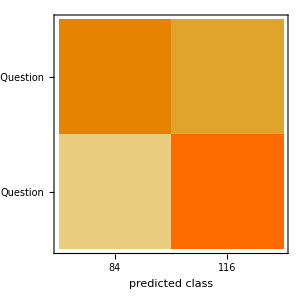

```mathematica
cm["ConfusionMatrixPlot"]
```

### With Vector Numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]/.rules}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]/.rules}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]/.rules}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]/.rules}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]/.rules}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]/.rules}] |>]
```

ClassifierMeasurementsObject[…]

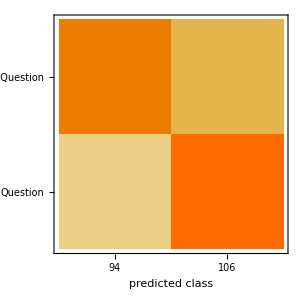

```mathematica
cm["ConfusionMatrixPlot"]
```

### Classify with 1000 sentences per class

```mathematica
partsOfSpeechNumbers [ questions[[1;;100]] ]
```

```mathematica
cl1000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;2000]]],

"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;2000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;200]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;200]]] |>,

PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cl1000
```

```mathematica
cm =ClassifierMeasurements[cl1000,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;500]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

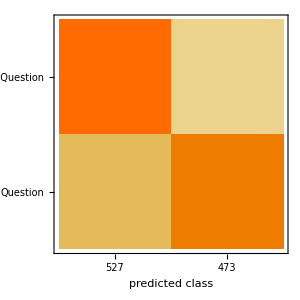

```mathematica
cm["ConfusionMatrixPlot"]
```

### 5000

```mathematica
cl5000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;5000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;500]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;500]]] |>,

PerformanceGoal->"Speed"]
```

### 200

```mathematica
cl200=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;1000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;1000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;100]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;100]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;50]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;50]]]|>]
```

ClassifierMeasurementsObject[…]

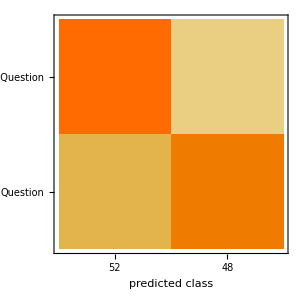

```mathematica
cm["ConfusionMatrixPlot"]
```

### 1000

```mathematica
cl1000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;1000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;1000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;100]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;100]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl1000,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;500]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

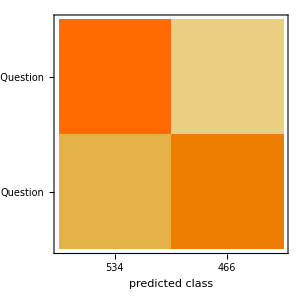

```mathematica
cm["ConfusionMatrixPlot"]
```

### Wh - question s

```mathematica
whQuestions = {"which"," what", "whose" , "who", "whom", "whose", "what", "which", "where","whither" ,"whence","when","how" ,"why" ,"whether","whatsoever"};
```

```mathematica
StringContainsQ["which", whQuestions]
```

True

```mathematica
vectorNumbers [ lines_ ] := Map[
 (((( TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]] ) 
     /. Missing[] -> {"","Missing"}))[[All,2]]) & ,
 lines
 ]
 
whQuestionsChecker [ lines_ ] := StringContainsQ[lines, whQuestions, IgnoreCase->True]
```

```mathematica
whQuestionsChecker [ testq1[[1;;100]] ]/.{True->1,False ->0}
```

{0,0,0,1,0,1,1,1,0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,1,1,0,0,0,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,0,0,0}

### 1000

```mathematica
cl1000=Classify[

<|
"Question"-> 
createClasses[ questions[[1;;5000]]], 

"Not Question"-> createClasses[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> createClasses[ validationq1[[1;;300]]],

 "Not Question"->createClasses[ validationnonq1[[1;;300]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> createClasses [ testq1[[1;;200]]], "Not Question"->  createClasses[testnonq1[[1;;200]]]|>]
```

ClassifierMeasurementsObject[…]

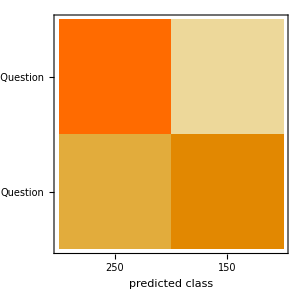

```mathematica
cm["ConfusionMatrixPlot"]
```

### 5000

```mathematica
cl1000=Classify[

<|
"Question"-> 
createClasses[ questions[[1;;5000]]], 

"Not Question"-> createClasses[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> createClasses[ validationq1[[1;;300]]],

 "Not Question"->createClasses[ validationnonq1[[1;;300]]] |>]
```

Java::excptn: A Java exception occurred: java.lang.OutOfMemoryError: Java heap space
	at edu.stanford.nlp.trees.LabeledScoredTreeFactory.newTreeNode(LabeledScoredTreeFactory.java:56)
	at edu.stanford.nlp.parser.common.ParserUtils.xTree(ParserUtils.java:41)
	at edu.stanford.nlp.parser.lexparser.LexicalizedParser.parse(LexicalizedParser.java:313)
	at edu.stanford.nlp.parser.common.ParserGrammar.parse(ParserGrammar.java:84)
	at sun.reflect.GeneratedMethodAccessor8.invoke(Unknown Source).

Table::iterb: Iterator {MachineLearning`Models`GrammaticalParser`Private`i,$Failed[MachineLearning`Models`GrammaticalParser`Private`numChildren[]]} does not have appropriate bounds.

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> createClasses [ testq1[[1;;500]]], "Not Question"->  createClasses[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

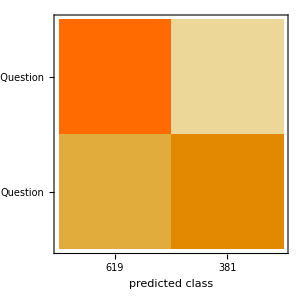

```mathematica
cm["ConfusionMatrixPlot"]
```

### 4000 + 5W1H parameter

```mathematica
cl40003D=Classify[train3D,ValidationSet->validationset]
```

ClassifierFunction[…]

```mathematica
cm40003D =ClassifierMeasurements[cl40003D,testset]
```

ClassifierMeasurementsObject[…]